## Initial Definitions

```mathematica
lie[σ_,lr_,rBar_]=σ*(σ*Cos[ξ/2]+1-σ)/(2*rBar^2)*Sin[ξ/2]*Sin[ξ-β]+σ/(2*rBar*lr)*Sin[ξ/2]*Sin[β]+(σ*Cos[ξ/2]+1-σ)^2/rBar^2*Cos[ξ-β]
```

(Cos[β-ξ] (1-σ+σ Cos[ξ/2])^2)/rBar^2+(σ Sin[β] Sin[ξ/2])/(2 lr rBar)-(σ (1-σ+σ Cos[ξ/2]) Sin[β-ξ] Sin[ξ/2])/(2 rBar^2)

```mathematica
SetDirectory["/Volumes/Scratch/OneDrive/Documents/bicycle safety NN data"];
```

## Symbolic Derivative Calculations

```mathematica
dxi[σ_,lr_,rBar_]=D[lie[σ,lr,rBar],ξ];
dbeta[σ_,lr_,rBar_]=D[lie[σ,lr,rBar],β];
```

```mathematica
dxi[ξ_,β_,σ_,lr_,rBar_]=D[lie[σ,lr,rBar],ξ];
dbeta[ξ_,β_,σ_,lr_,rBar_]=D[lie[σ,lr,rBar],β];
```

```mathematica
deriv[ξ_,β_,σ_,lr_,rBar_]=Simplify[-dxi[σ,lr,rBar]/dbeta[σ,lr,rBar]]
```

-((2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2])/(4 (-2 lr (1-σ+σ Cos[ξ/2])^2 Sin[β-ξ]+rBar σ Cos[β] Sin[ξ/2]-lr σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])))

```mathematica
secDeriv[ξ_,β_,σ_,lr_,rBar_]=Simplify[D[deriv[ξ,β[ξ],σ,lr,rBar],ξ]/.{β[ξ]->β,β'[ξ]->deriv[ξ,β,σ,lr,rBar]}]
```

(σ (8 rBar (rBar-5 lr (-1+σ)) σ Sin[2 β]+(8 (2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (32 lr-8 rBar-96 lr σ+16 rBar σ+142 lr σ^2-13 rBar σ^2-78 lr σ^3+(-42 lr (-1+σ) σ^2+rBar (-24+48 σ-38 σ^2)) Cos[ξ]+6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]-5 rBar σ^2 Cos[2 ξ])) (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]) Sin[ξ/2])/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])-lr (-3 lr (-1+σ) σ^2 Sin[2 β-(7 ξ)/2]+8 lr σ (2-4 σ+3 σ^2) Sin[2 β-3 ξ]+24 lr Sin[2 β-(5 ξ)/2]-72 lr σ Sin[2 β-(5 ξ)/2]+129 lr σ^2 Sin[2 β-(5 ξ)/2]+9 rBar σ^2 Sin[2 β-(5 ξ)/2]-81 lr σ^3 Sin[2 β-(5 ξ)/2]+40 lr Sin[2 β-(3 ξ)/2]+8 rBar Sin[2 β-(3 ξ)/2]-120 lr σ Sin[2 β-(3 ξ)/2]-16 rBar σ Sin[2 β-(3 ξ)/2]+221 lr σ^2 Sin[2 β-(3 ξ)/2]-13 rBar σ^2 Sin[2 β-(3 ξ)/2]-141 lr σ^3 Sin[2 β-(3 ξ)/2]+120 lr σ Sin[2 (β-ξ)]+24 rBar σ Sin[2 (β-ξ)]-240 lr σ^2 Sin[2 (β-ξ)]-24 rBar σ^2 Sin[2 (β-ξ)]+144 lr σ^3 Sin[2 (β-ξ)]+48 lr σ Sin[2 β-ξ]-96 rBar σ Sin[2 β-ξ]-96 lr σ^2 Sin[2 β-ξ]+96 rBar σ^2 Sin[2 β-ξ]+72 lr σ^3 Sin[2 β-ξ]-72 rBar Sin[2 β-ξ/2]+144 rBar σ Sin[2 β-ξ/2]+15 lr σ^2 Sin[2 β-ξ/2]-105 rBar σ^2 Sin[2 β-ξ/2]-15 lr σ^3 Sin[2 β-ξ/2]+240 lr Sin[ξ/2]+24 rBar Sin[ξ/2]-720 lr σ Sin[ξ/2]-48 rBar σ Sin[ξ/2]+876 lr σ^2 Sin[ξ/2]+42 rBar σ^2 Sin[ξ/2]-396 lr σ^3 Sin[ξ/2]+336 lr σ Sin[ξ]+48 rBar σ Sin[ξ]-672 lr σ^2 Sin[ξ]-48 rBar σ^2 Sin[ξ]+384 lr σ^3 Sin[ξ]-24 rBar Sin[(3 ξ)/2]+48 rBar σ Sin[(3 ξ)/2]+156 lr σ^2 Sin[(3 ξ)/2]-21 rBar σ^2 Sin[(3 ξ)/2]-156 lr σ^3 Sin[(3 ξ)/2]-48 rBar σ Sin[2 ξ]+48 rBar σ^2 Sin[2 ξ]+24 lr σ^3 Sin[2 ξ]-15 rBar σ^2 Sin[(5 ξ)/2]-3 rBar σ^2 Sin[1/2 (4 β+ξ)])))/(64 (2 lr (1-σ+σ Cos[ξ/2])^2 Sin[β-ξ]-rBar σ Cos[β] Sin[ξ/2]+lr σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])^2)

```mathematica
(* This commond takes a long time, and uses a lot of memory, so the following cell contains the output *)
triDeriv[ξ_,β_,σ_,lr_,rBar_]=Simplify[D[secDeriv[ξ,β[ξ],σ,lr,rBar],ξ]/.{β[ξ]->β,β'[ξ]->deriv[ξ,β,σ,lr,rBar]}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
(* The previous command takes a long time, and uses a lot of memory, so let's store the result: *)
triDeriv[ξ_,β_,σ_,lr_,rBar_]=(σ*(-((σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))*Sin[ξ/2]*(8*rBar*(rBar-5*lr*(-1+σ))*σ*Sin[2*β]+(8*(2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(32*lr-8*rBar-96*lr*σ+16*rBar*σ+142*lr*σ^2-13*rBar*σ^2-78*lr*σ^3+(-42*lr*(-1+σ)*σ^2+rBar*(-24+48*σ-38*σ^2))*Cos[ξ]+6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]-5*rBar*σ^2*Cos[2*ξ]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2])/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])-lr*(-3*lr*(-1+σ)*σ^2*Sin[2*β-(7*ξ)/2]+8*lr*σ*(2-4*σ+3*σ^2)*Sin[2*β-3*ξ]+24*lr*Sin[2*β-(5*ξ)/2]-72*lr*σ*Sin[2*β-(5*ξ)/2]+129*lr*σ^2*Sin[2*β-(5*ξ)/2]+9*rBar*σ^2*Sin[2*β-(5*ξ)/2]-81*lr*σ^3*Sin[2*β-(5*ξ)/2]+40*lr*Sin[2*β-(3*ξ)/2]+8*rBar*Sin[2*β-(3*ξ)/2]-120*lr*σ*Sin[2*β-(3*ξ)/2]-16*rBar*σ*Sin[2*β-(3*ξ)/2]+221*lr*σ^2*Sin[2*β-(3*ξ)/2]-13*rBar*σ^2*Sin[2*β-(3*ξ)/2]-141*lr*σ^3*Sin[2*β-(3*ξ)/2]+120*lr*σ*Sin[2*(β-ξ)]+24*rBar*σ*Sin[2*(β-ξ)]-240*lr*σ^2*Sin[2*(β-ξ)]-24*rBar*σ^2*Sin[2*(β-ξ)]+144*lr*σ^3*Sin[2*(β-ξ)]+48*lr*σ*Sin[2*β-ξ]-96*rBar*σ*Sin[2*β-ξ]-96*lr*σ^2*Sin[2*β-ξ]+96*rBar*σ^2*Sin[2*β-ξ]+72*lr*σ^3*Sin[2*β-ξ]-72*rBar*Sin[2*β-ξ/2]+144*rBar*σ*Sin[2*β-ξ/2]+15*lr*σ^2*Sin[2*β-ξ/2]-105*rBar*σ^2*Sin[2*β-ξ/2]-15*lr*σ^3*Sin[2*β-ξ/2]+240*lr*Sin[ξ/2]+24*rBar*Sin[ξ/2]-720*lr*σ*Sin[ξ/2]-48*rBar*σ*Sin[ξ/2]+876*lr*σ^2*Sin[ξ/2]+42*rBar*σ^2*Sin[ξ/2]-396*lr*σ^3*Sin[ξ/2]+336*lr*σ*Sin[ξ]+48*rBar*σ*Sin[ξ]-672*lr*σ^2*Sin[ξ]-48*rBar*σ^2*Sin[ξ]+384*lr*σ^3*Sin[ξ]-24*rBar*Sin[(3*ξ)/2]+48*rBar*σ*Sin[(3*ξ)/2]+156*lr*σ^2*Sin[(3*ξ)/2]-21*rBar*σ^2*Sin[(3*ξ)/2]-156*lr*σ^3*Sin[(3*ξ)/2]-48*rBar*σ*Sin[2*ξ]+48*rBar*σ^2*Sin[2*ξ]+24*lr*σ^3*Sin[2*ξ]-15*rBar*σ^2*Sin[(5*ξ)/2]-3*rBar*σ^2*Sin[(4*β+ξ)/2])))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2]))+(2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]-rBar*σ*Cos[β]*Sin[ξ/2]+lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])*((4*Cos[ξ/2]*(2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(32*lr-8*rBar-96*lr*σ+16*rBar*σ+142*lr*σ^2-13*rBar*σ^2-78*lr*σ^3+(-42*lr*(-1+σ)*σ^2+rBar*(-24+48*σ-38*σ^2))*Cos[ξ]+6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]-5*rBar*σ^2*Cos[2*ξ]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2]))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])+(16*σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))^2*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2]^2)/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])^3+(16*(6*lr*(7*lr*(-1+σ)*σ^2+rBar*(4-8*σ+8*σ^2))*Cos[ξ/2]+σ*(-23*lr^2+26*lr*rBar+rBar^2+46*lr^2*σ-26*lr*rBar*σ-33*lr^2*σ^2-9*lr*(4*rBar*(-1+σ)+lr*σ^2)*Cos[ξ]+10*lr*rBar*σ*Cos[(3*ξ)/2]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2]^2)/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])-(4*rBar*(rBar-5*lr*(-1+σ))*σ*Cos[2*β]*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2]))/(-2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]+rBar*σ*Cos[β]*Sin[ξ/2]-lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])+(2*σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))*Sin[ξ/2]*(-8*rBar*(rBar-5*lr*(-1+σ))*σ*Sin[2*β]+lr*(-3*lr*(-1+σ)*σ^2*Sin[2*β-(7*ξ)/2]+8*lr*σ*(2-4*σ+3*σ^2)*Sin[2*β-3*ξ]+24*lr*Sin[2*β-(5*ξ)/2]-72*lr*σ*Sin[2*β-(5*ξ)/2]+129*lr*σ^2*Sin[2*β-(5*ξ)/2]+9*rBar*σ^2*Sin[2*β-(5*ξ)/2]-81*lr*σ^3*Sin[2*β-(5*ξ)/2]+40*lr*Sin[2*β-(3*ξ)/2]+8*rBar*Sin[2*β-(3*ξ)/2]-120*lr*σ*Sin[2*β-(3*ξ)/2]-16*rBar*σ*Sin[2*β-(3*ξ)/2]+221*lr*σ^2*Sin[2*β-(3*ξ)/2]-13*rBar*σ^2*Sin[2*β-(3*ξ)/2]-141*lr*σ^3*Sin[2*β-(3*ξ)/2]+120*lr*σ*Sin[2*(β-ξ)]+24*rBar*σ*Sin[2*(β-ξ)]-240*lr*σ^2*Sin[2*(β-ξ)]-24*rBar*σ^2*Sin[2*(β-ξ)]+144*lr*σ^3*Sin[2*(β-ξ)]+48*lr*σ*Sin[2*β-ξ]-96*rBar*σ*Sin[2*β-ξ]-96*lr*σ^2*Sin[2*β-ξ]+96*rBar*σ^2*Sin[2*β-ξ]+72*lr*σ^3*Sin[2*β-ξ]-72*rBar*Sin[2*β-ξ/2]+144*rBar*σ*Sin[2*β-ξ/2]+15*lr*σ^2*Sin[2*β-ξ/2]-105*rBar*σ^2*Sin[2*β-ξ/2]-15*lr*σ^3*Sin[2*β-ξ/2]+240*lr*Sin[ξ/2]+24*rBar*Sin[ξ/2]-720*lr*σ*Sin[ξ/2]-48*rBar*σ*Sin[ξ/2]+876*lr*σ^2*Sin[ξ/2]+42*rBar*σ^2*Sin[ξ/2]-396*lr*σ^3*Sin[ξ/2]+336*lr*σ*Sin[ξ]+48*rBar*σ*Sin[ξ]-672*lr*σ^2*Sin[ξ]-48*rBar*σ^2*Sin[ξ]+384*lr*σ^3*Sin[ξ]-24*rBar*Sin[(3*ξ)/2]+48*rBar*σ*Sin[(3*ξ)/2]+156*lr*σ^2*Sin[(3*ξ)/2]-21*rBar*σ^2*Sin[(3*ξ)/2]-156*lr*σ^3*Sin[(3*ξ)/2]-48*rBar*σ*Sin[2*ξ]+48*rBar*σ^2*Sin[2*ξ]+24*lr*σ^3*Sin[2*ξ]-15*rBar*σ^2*Sin[(5*ξ)/2]-3*rBar*σ^2*Sin[(4*β+ξ)/2])))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])^2+(lr*(-24*σ*(3*rBar^2*(2-4*σ+3*σ^2)-2*lr*rBar*(-56+168*σ-205*σ^2+93*σ^3)+2*lr^2*(131-524*σ+882*σ^2-716*σ^3+231*σ^4))*Sin[β]+216*rBar^2*σ*(2-4*σ+3*σ^2)*Sin[3*β]-3*lr^2*σ^4*Sin[3*β-(11*ξ)/2]+3*lr^2*σ^5*Sin[3*β-(11*ξ)/2]-14*lr^2*σ^3*Sin[3*β-5*ξ]+28*lr^2*σ^4*Sin[3*β-5*ξ]-30*lr^2*σ^5*Sin[3*β-5*ξ]+75*lr*rBar*σ^4*Sin[β-(9*ξ)/2]-135*lr^2*σ^4*Sin[3*β-(9*ξ)/2]-27*lr*rBar*σ^4*Sin[3*β-(9*ξ)/2]+135*lr^2*σ^5*Sin[3*β-(9*ξ)/2]+696*lr*rBar*σ^3*Sin[β-4*ξ]-696*lr*rBar*σ^4*Sin[β-4*ξ]-96*lr^2*σ^5*Sin[β-4*ξ]+112*lr^2*σ*Sin[3*β-4*ξ]-448*lr^2*σ^2*Sin[3*β-4*ξ]+256*lr^2*σ^3*Sin[3*β-4*ξ]-120*lr*rBar*σ^3*Sin[3*β-4*ξ]+384*lr^2*σ^4*Sin[3*β-4*ξ]+120*lr*rBar*σ^4*Sin[3*β-4*ξ]-336*lr^2*σ^5*Sin[3*β-4*ξ]+2080*lr*rBar*σ^2*Sin[β-(7*ξ)/2]-4160*lr*rBar*σ^3*Sin[β-(7*ξ)/2]-1107*lr^2*σ^4*Sin[β-(7*ξ)/2]+2499*lr*rBar*σ^4*Sin[β-(7*ξ)/2]+1107*lr^2*σ^5*Sin[β-(7*ξ)/2]+192*lr^2*Sin[3*β-(7*ξ)/2]-960*lr^2*σ*Sin[3*β-(7*ξ)/2]+1472*lr^2*σ^2*Sin[3*β-(7*ξ)/2]-128*lr*rBar*σ^2*Sin[3*β-(7*ξ)/2]-576*lr^2*σ^3*Sin[3*β-(7*ξ)/2]+256*lr*rBar*σ^3*Sin[3*β-(7*ξ)/2]-566*lr^2*σ^4*Sin[3*β-(7*ξ)/2]+77*lr*rBar*σ^4*Sin[3*β-(7*ξ)/2]+438*lr^2*σ^5*Sin[3*β-(7*ξ)/2]+2304*lr*rBar*σ*Sin[β-3*ξ]-6912*lr*rBar*σ^2*Sin[β-3*ξ]-4686*lr^2*σ^3*Sin[β-3*ξ]+9048*lr*rBar*σ^3*Sin[β-3*ξ]+276*rBar^2*σ^3*Sin[β-3*ξ]+9372*lr^2*σ^4*Sin[β-3*ξ]-4440*lr*rBar*σ^4*Sin[β-3*ξ]-5310*lr^2*σ^5*Sin[β-3*ξ]+576*lr*rBar*Sin[β-(5*ξ)/2]-2304*lr*rBar*σ*Sin[β-(5*ξ)/2]-9088*lr^2*σ^2*Sin[β-(5*ξ)/2]+6304*lr*rBar*σ^2*Sin[β-(5*ξ)/2]+672*rBar^2*σ^2*Sin[β-(5*ξ)/2]+27264*lr^2*σ^3*Sin[β-(5*ξ)/2]-8000*lr*rBar*σ^3*Sin[β-(5*ξ)/2]-672*rBar^2*σ^3*Sin[β-(5*ξ)/2]-32039*lr^2*σ^4*Sin[β-(5*ξ)/2]+3492*lr*rBar*σ^4*Sin[β-(5*ξ)/2]+13863*lr^2*σ^5*Sin[β-(5*ξ)/2]-320*lr^2*Sin[3*β-(5*ξ)/2]-64*lr*rBar*Sin[3*β-(5*ξ)/2]+1600*lr^2*σ*Sin[3*β-(5*ξ)/2]+256*lr*rBar*σ*Sin[3*β-(5*ξ)/2]-2560*lr^2*σ^2*Sin[3*β-(5*ξ)/2]+3264*lr*rBar*σ^2*Sin[3*β-(5*ξ)/2]+96*rBar^2*σ^2*Sin[3*β-(5*ξ)/2]+1280*lr^2*σ^3*Sin[3*β-(5*ξ)/2]-7040*lr*rBar*σ^3*Sin[3*β-(5*ξ)/2]-96*rBar^2*σ^3*Sin[3*β-(5*ξ)/2]+570*lr^2*σ^4*Sin[3*β-(5*ξ)/2]+4002*lr*rBar*σ^4*Sin[3*β-(5*ξ)/2]-570*lr^2*σ^5*Sin[3*β-(5*ξ)/2]-7792*lr^2*σ*Sin[β-2*ξ]+64*lr*rBar*σ*Sin[β-2*ξ]+224*rBar^2*σ*Sin[β-2*ξ]+31168*lr^2*σ^2*Sin[β-2*ξ]-192*lr*rBar*σ^2*Sin[β-2*ξ]-448*rBar^2*σ^2*Sin[β-2*ξ]-59248*lr^2*σ^3*Sin[β-2*ξ]-640*lr*rBar*σ^3*Sin[β-2*ξ]-208*rBar^2*σ^3*Sin[β-2*ξ]+56160*lr^2*σ^4*Sin[β-2*ξ]+768*lr*rBar*σ^4*Sin[β-2*ξ]-21312*lr^2*σ^5*Sin[β-2*ξ]-368*lr^2*σ*Sin[3*β-2*ξ]+3520*lr*rBar*σ*Sin[3*β-2*ξ]+16*rBar^2*σ*Sin[3*β-2*ξ]+1472*lr^2*σ^2*Sin[3*β-2*ξ]-10560*lr*rBar*σ^2*Sin[3*β-2*ξ]-32*rBar^2*σ^2*Sin[3*β-2*ξ]-976*lr^2*σ^3*Sin[3*β-2*ξ]+11800*lr*rBar*σ^3*Sin[3*β-2*ξ]-152*rBar^2*σ^3*Sin[3*β-2*ξ]-992*lr^2*σ^4*Sin[3*β-2*ξ]-4760*lr*rBar*σ^4*Sin[3*β-2*ξ]+960*lr^2*σ^5*Sin[3*β-2*ξ]-2112*lr^2*Sin[β-(3*ξ)/2]-192*lr*rBar*Sin[β-(3*ξ)/2]+10560*lr^2*σ*Sin[β-(3*ξ)/2]+768*lr*rBar*σ*Sin[β-(3*ξ)/2]-33600*lr^2*σ^2*Sin[β-(3*ξ)/2]-4224*lr*rBar*σ^2*Sin[β-(3*ξ)/2]-1440*rBar^2*σ^2*Sin[β-(3*ξ)/2]+58560*lr^2*σ^3*Sin[β-(3*ξ)/2]+6912*lr*rBar*σ^3*Sin[β-(3*ξ)/2]+1440*rBar^2*σ^3*Sin[β-(3*ξ)/2]-52758*lr^2*σ^4*Sin[β-(3*ξ)/2]-3132*lr*rBar*σ^4*Sin[β-(3*ξ)/2]+19350*lr^2*σ^5*Sin[β-(3*ξ)/2]+1728*lr*rBar*Sin[3*β-(3*ξ)/2]-6912*lr*rBar*σ*Sin[3*β-(3*ξ)/2]+10656*lr*rBar*σ^2*Sin[3*β-(3*ξ)/2]-288*rBar^2*σ^2*Sin[3*β-(3*ξ)/2]-7488*lr*rBar*σ^3*Sin[3*β-(3*ξ)/2]+288*rBar^2*σ^3*Sin[3*β-(3*ξ)/2]+729*lr^2*σ^4*Sin[3*β-(3*ξ)/2]+1962*lr*rBar*σ^4*Sin[3*β-(3*ξ)/2]-729*lr^2*σ^5*Sin[3*β-(3*ξ)/2]-4096*lr^2*σ*Sin[β-ξ]-1024*lr*rBar*σ*Sin[β-ξ]-640*rBar^2*σ*Sin[β-ξ]+16384*lr^2*σ^2*Sin[β-ξ]+3072*lr*rBar*σ^2*Sin[β-ξ]+1280*rBar^2*σ^2*Sin[β-ξ]-30684*lr^2*σ^3*Sin[β-ξ]-2392*lr*rBar*σ^3*Sin[β-ξ]-814*rBar^2*σ^3*Sin[β-ξ]+28600*lr^2*σ^4*Sin[β-ξ]+344*lr*rBar*σ^4*Sin[β-ξ]-10716*lr^2*σ^5*Sin[β-ξ]-108*lr^2*σ^3*Sin[3*(β-ξ)]+1512*lr*rBar*σ^3*Sin[3*(β-ξ)]+54*rBar^2*σ^3*Sin[3*(β-ξ)]+216*lr^2*σ^4*Sin[3*(β-ξ)]-1512*lr*rBar*σ^4*Sin[3*(β-ξ)]-108*lr^2*σ^5*Sin[3*(β-ξ)]+320*lr*rBar*σ*Sin[3*β-ξ]+64*rBar^2*σ*Sin[3*β-ξ]-960*lr*rBar*σ^2*Sin[3*β-ξ]-128*rBar^2*σ^2*Sin[3*β-ξ]+138*lr^2*σ^3*Sin[3*β-ξ]-200*lr*rBar*σ^3*Sin[3*β-ξ]+340*rBar^2*σ^3*Sin[3*β-ξ]-276*lr^2*σ^4*Sin[3*β-ξ]+840*lr*rBar*σ^4*Sin[3*β-ξ]+282*lr^2*σ^5*Sin[3*β-ξ]-1600*lr^2*Sin[β-ξ/2]-128*lr*rBar*Sin[β-ξ/2]+8000*lr^2*σ*Sin[β-ξ/2]+512*lr*rBar*σ*Sin[β-ξ/2]-20480*lr^2*σ^2*Sin[β-ξ/2]+128*lr*rBar*σ^2*Sin[β-ξ/2]+192*rBar^2*σ^2*Sin[β-ξ/2]+29440*lr^2*σ^3*Sin[β-ξ/2]-1280*lr*rBar*σ^3*Sin[β-ξ/2]-192*rBar^2*σ^3*Sin[β-ξ/2]-22758*lr^2*σ^4*Sin[β-ξ/2]+867*lr*rBar*σ^4*Sin[β-ξ/2]+7398*lr^2*σ^5*Sin[β-ξ/2]-480*lr*rBar*σ^2*Sin[3*β-ξ/2]+768*rBar^2*σ^2*Sin[3*β-ξ/2]+960*lr*rBar*σ^3*Sin[3*β-ξ/2]-768*rBar^2*σ^3*Sin[3*β-ξ/2]+45*lr^2*σ^4*Sin[3*β-ξ/2]-711*lr*rBar*σ^4*Sin[3*β-ξ/2]-45*lr^2*σ^5*Sin[3*β-ξ/2]-1152*lr*rBar*Sin[β+ξ/2]+4608*lr*rBar*σ*Sin[β+ξ/2]-9472*lr^2*σ^2*Sin[β+ξ/2]-11840*lr*rBar*σ^2*Sin[β+ξ/2]-192*rBar^2*σ^2*Sin[β+ξ/2]+28416*lr^2*σ^3*Sin[β+ξ/2]+14464*lr*rBar*σ^3*Sin[β+ξ/2]+192*rBar^2*σ^3*Sin[β+ξ/2]-31031*lr^2*σ^4*Sin[β+ξ/2]-6797*lr*rBar*σ^4*Sin[β+ξ/2]+12087*lr^2*σ^5*Sin[β+ξ/2]+576*lr*rBar*σ*Sin[β+ξ]+192*rBar^2*σ*Sin[β+ξ]-1728*lr*rBar*σ^2*Sin[β+ξ]-384*rBar^2*σ^2*Sin[β+ξ]-6726*lr^2*σ^3*Sin[β+ξ]+288*lr*rBar*σ^3*Sin[β+ξ]+192*rBar^2*σ^3*Sin[β+ξ]+13452*lr^2*σ^4*Sin[β+ξ]+864*lr*rBar*σ^4*Sin[β+ξ]-7254*lr^2*σ^5*Sin[β+ξ]+6*rBar^2*σ^3*Sin[3*β+ξ]+9*lr*rBar*σ^4*Sin[(6*β+ξ)/2]+3456*lr*rBar*σ^2*Sin[β+(3*ξ)/2]+576*rBar^2*σ^2*Sin[β+(3*ξ)/2]-6912*lr*rBar*σ^3*Sin[β+(3*ξ)/2]-576*rBar^2*σ^3*Sin[β+(3*ξ)/2]-2259*lr^2*σ^4*Sin[β+(3*ξ)/2]+3438*lr*rBar*σ^4*Sin[β+(3*ξ)/2]+2259*lr^2*σ^5*Sin[β+(3*ξ)/2]-144*rBar^2*σ*Sin[β+2*ξ]+288*rBar^2*σ^2*Sin[β+2*ξ]+2136*lr*rBar*σ^3*Sin[β+2*ξ]+24*rBar^2*σ^3*Sin[β+2*ξ]-2136*lr*rBar*σ^4*Sin[β+2*ξ]-288*lr^2*σ^5*Sin[β+2*ξ]-384*rBar^2*σ^2*Sin[β+(5*ξ)/2]+384*rBar^2*σ^3*Sin[β+(5*ξ)/2]+390*lr*rBar*σ^4*Sin[β+(5*ξ)/2]-150*rBar^2*σ^3*Sin[β+3*ξ]))/(4*(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])))))/(64*(2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]-rBar*σ*Cos[β]*Sin[ξ/2]+lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])^3)
```

(σ (-((σ (-2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (-32 lr+8 rBar+96 lr σ-16 rBar σ-142 lr σ^2+13 rBar σ^2+78 lr σ^3+(42 lr (-1+σ) σ^2+rBar (24-48 σ+38 σ^2)) Cos[ξ]-6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]+5 rBar σ^2 Cos[2 ξ])) Sin[ξ/2] (8 rBar (rBar-5 lr (-1+σ)) σ Sin[2 β]+(8 (2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (32 lr-8 rBar-96 lr σ+16 rBar σ+142 lr σ^2-13 rBar σ^2-78 lr σ^3+(-42 lr (-1+σ) σ^2+rBar (-24+48 σ-38 σ^2)) Cos[ξ]+6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]-5 rBar σ^2 Cos[2 ξ])) (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]) Sin[ξ/2])/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])-lr (-3 lr (-1+σ) σ^2 Sin[2 β-(7 ξ)/2]+8 lr σ (2-4 σ+3 σ^2) Sin[2 β-3 ξ]+24 lr Sin[2 β-(5 ξ)/2]-72 lr σ Sin[2 β-(5 ξ)/2]+129 lr σ^2 Sin[2 β-(5 ξ)/2]+9 rBar σ^2 Sin[2 β-(5 ξ)/2]-81 lr σ^3 Sin[2 β-(5 ξ)/2]+40 lr Sin[2 β-(3 ξ)/2]+8 rBar Sin[2 β-(3 ξ)/2]-120 lr σ Sin[2 β-(3 ξ)/2]-16 rBar σ Sin[2 β-(3 ξ)/2]+221 lr σ^2 Sin[2 β-(3 ξ)/2]-13 rBar σ^2 Sin[2 β-(3 ξ)/2]-141 lr σ^3 Sin[2 β-(3 ξ)/2]+120 lr σ Sin[2 (β-ξ)]+24 rBar σ Sin[2 (β-ξ)]-240 lr σ^2 Sin[2 (β-ξ)]-24 rBar σ^2 Sin[2 (β-ξ)]+144 lr σ^3 Sin[2 (β-ξ)]+48 lr σ Sin[2 β-ξ]-96 rBar σ Sin[2 β-ξ]-96 lr σ^2 Sin[2 β-ξ]+96 rBar σ^2 Sin[2 β-ξ]+72 lr σ^3 Sin[2 β-ξ]-72 rBar Sin[2 β-ξ/2]+144 rBar σ Sin[2 β-ξ/2]+15 lr σ^2 Sin[2 β-ξ/2]-105 rBar σ^2 Sin[2 β-ξ/2]-15 lr σ^3 Sin[2 β-ξ/2]+240 lr Sin[ξ/2]+24 rBar Sin[ξ/2]-720 lr σ Sin[ξ/2]-48 rBar σ Sin[ξ/2]+876 lr σ^2 Sin[ξ/2]+42 rBar σ^2 Sin[ξ/2]-396 lr σ^3 Sin[ξ/2]+336 lr σ Sin[ξ]+48 rBar σ Sin[ξ]-672 lr σ^2 Sin[ξ]-48 rBar σ^2 Sin[ξ]+384 lr σ^3 Sin[ξ]-24 rBar Sin[(3 ξ)/2]+48 rBar σ Sin[(3 ξ)/2]+156 lr σ^2 Sin[(3 ξ)/2]-21 rBar σ^2 Sin[(3 ξ)/2]-156 lr σ^3 Sin[(3 ξ)/2]-48 rBar σ Sin[2 ξ]+48 rBar σ^2 Sin[2 ξ]+24 lr σ^3 Sin[2 ξ]-15 rBar σ^2 Sin[(5 ξ)/2]-3 rBar σ^2 Sin[1/2 (4 β+ξ)])))/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2]))+(2 lr (1-σ+σ Cos[ξ/2])^2 Sin[β-ξ]-rBar σ Cos[β] Sin[ξ/2]+lr σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2]) ((4 Cos[ξ/2] (2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (32 lr-8 rBar-96 lr σ+16 rBar σ+142 lr σ^2-13 rBar σ^2-78 lr σ^3+(-42 lr (-1+σ) σ^2+rBar (-24+48 σ-38 σ^2)) Cos[ξ]+6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]-5 rBar σ^2 Cos[2 ξ])) (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]))/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])+(16 σ (-2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (-32 lr+8 rBar+96 lr σ-16 rBar σ-142 lr σ^2+13 rBar σ^2+78 lr σ^3+(42 lr (-1+σ) σ^2+rBar (24-48 σ+38 σ^2)) Cos[ξ]-6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]+5 rBar σ^2 Cos[2 ξ]))^2 (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]) Sin[ξ/2]^2)/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])^3+(16 (6 lr (7 lr (-1+σ) σ^2+rBar (4-8 σ+8 σ^2)) Cos[ξ/2]+σ (-23 lr^2+26 lr rBar+rBar^2+46 lr^2 σ-26 lr rBar σ-33 lr^2 σ^2-9 lr (4 rBar (-1+σ)+lr σ^2) Cos[ξ]+10 lr rBar σ Cos[(3 ξ)/2])) (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]) Sin[ξ/2]^2)/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])-(4 rBar (rBar-5 lr (-1+σ)) σ Cos[2 β] (2 lr σ^2 Sin[β-2 ξ]-9 lr (-1+σ) σ Sin[β-(3 ξ)/2]+8 lr Sin[β-ξ]-16 lr σ Sin[β-ξ]+12 lr σ^2 Sin[β-ξ]+5 lr σ Sin[β-ξ/2]+rBar σ Sin[β-ξ/2]-5 lr σ^2 Sin[β-ξ/2]+rBar σ Sin[β+ξ/2]))/(-2 lr (1-σ+σ Cos[ξ/2])^2 Sin[β-ξ]+rBar σ Cos[β] Sin[ξ/2]-lr σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])+(2 σ (-2 σ (-2 rBar^2+16 lr rBar (-1+σ)+lr^2 (46-92 σ+57 σ^2)) Cos[ξ/2]+lr (-32 lr+8 rBar+96 lr σ-16 rBar σ-142 lr σ^2+13 rBar σ^2+78 lr σ^3+(42 lr (-1+σ) σ^2+rBar (24-48 σ+38 σ^2)) Cos[ξ]-6 σ (4 rBar (-1+σ)+lr σ^2) Cos[(3 ξ)/2]+5 rBar σ^2 Cos[2 ξ])) Sin[ξ/2] (-8 rBar (rBar-5 lr (-1+σ)) σ Sin[2 β]+lr (-3 lr (-1+σ) σ^2 Sin[2 β-(7 ξ)/2]+8 lr σ (2-4 σ+3 σ^2) Sin[2 β-3 ξ]+24 lr Sin[2 β-(5 ξ)/2]-72 lr σ Sin[2 β-(5 ξ)/2]+129 lr σ^2 Sin[2 β-(5 ξ)/2]+9 rBar σ^2 Sin[2 β-(5 ξ)/2]-81 lr σ^3 Sin[2 β-(5 ξ)/2]+40 lr Sin[2 β-(3 ξ)/2]+8 rBar Sin[2 β-(3 ξ)/2]-120 lr σ Sin[2 β-(3 ξ)/2]-16 rBar σ Sin[2 β-(3 ξ)/2]+221 lr σ^2 Sin[2 β-(3 ξ)/2]-13 rBar σ^2 Sin[2 β-(3 ξ)/2]-141 lr σ^3 Sin[2 β-(3 ξ)/2]+120 lr σ Sin[2 (β-ξ)]+24 rBar σ Sin[2 (β-ξ)]-240 lr σ^2 Sin[2 (β-ξ)]-24 rBar σ^2 Sin[2 (β-ξ)]+144 lr σ^3 Sin[2 (β-ξ)]+48 lr σ Sin[2 β-ξ]-96 rBar σ Sin[2 β-ξ]-96 lr σ^2 Sin[2 β-ξ]+96 rBar σ^2 Sin[2 β-ξ]+72 lr σ^3 Sin[2 β-ξ]-72 rBar Sin[2 β-ξ/2]+144 rBar σ Sin[2 β-ξ/2]+15 lr σ^2 Sin[2 β-ξ/2]-105 rBar σ^2 Sin[2 β-ξ/2]-15 lr σ^3 Sin[2 β-ξ/2]+240 lr Sin[ξ/2]+24 rBar Sin[ξ/2]-720 lr σ Sin[ξ/2]-48 rBar σ Sin[ξ/2]+876 lr σ^2 Sin[ξ/2]+42 rBar σ^2 Sin[ξ/2]-396 lr σ^3 Sin[ξ/2]+336 lr σ Sin[ξ]+48 rBar σ Sin[ξ]-672 lr σ^2 Sin[ξ]-48 rBar σ^2 Sin[ξ]+384 lr σ^3 Sin[ξ]-24 rBar Sin[(3 ξ)/2]+48 rBar σ Sin[(3 ξ)/2]+156 lr σ^2 Sin[(3 ξ)/2]-21 rBar σ^2 Sin[(3 ξ)/2]-156 lr σ^3 Sin[(3 ξ)/2]-48 rBar σ Sin[2 ξ]+48 rBar σ^2 Sin[2 ξ]+24 lr σ^3 Sin[2 ξ]-15 rBar σ^2 Sin[(5 ξ)/2]-3 rBar σ^2 Sin[1/2 (4 β+ξ)])))/(3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])^2+(lr (-24 σ (3 rBar^2 (2-4 σ+3 σ^2)-2 lr rBar (-56+168 σ-205 σ^2+93 σ^3)+2 lr^2 (131-524 σ+882 σ^2-716 σ^3+231 σ^4)) Sin[β]+216 rBar^2 σ (2-4 σ+3 σ^2) Sin[3 β]-3 lr^2 σ^4 Sin[3 β-(11 ξ)/2]+3 lr^2 σ^5 Sin[3 β-(11 ξ)/2]-14 lr^2 σ^3 Sin[3 β-5 ξ]+28 lr^2 σ^4 Sin[3 β-5 ξ]-30 lr^2 σ^5 Sin[3 β-5 ξ]+75 lr rBar σ^4 Sin[β-(9 ξ)/2]-135 lr^2 σ^4 Sin[3 β-(9 ξ)/2]-27 lr rBar σ^4 Sin[3 β-(9 ξ)/2]+135 lr^2 σ^5 Sin[3 β-(9 ξ)/2]+696 lr rBar σ^3 Sin[β-4 ξ]-696 lr rBar σ^4 Sin[β-4 ξ]-96 lr^2 σ^5 Sin[β-4 ξ]+112 lr^2 σ Sin[3 β-4 ξ]-448 lr^2 σ^2 Sin[3 β-4 ξ]+256 lr^2 σ^3 Sin[3 β-4 ξ]-120 lr rBar σ^3 Sin[3 β-4 ξ]+384 lr^2 σ^4 Sin[3 β-4 ξ]+120 lr rBar σ^4 Sin[3 β-4 ξ]-336 lr^2 σ^5 Sin[3 β-4 ξ]+2080 lr rBar σ^2 Sin[β-(7 ξ)/2]-4160 lr rBar σ^3 Sin[β-(7 ξ)/2]-1107 lr^2 σ^4 Sin[β-(7 ξ)/2]+2499 lr rBar σ^4 Sin[β-(7 ξ)/2]+1107 lr^2 σ^5 Sin[β-(7 ξ)/2]+192 lr^2 Sin[3 β-(7 ξ)/2]-960 lr^2 σ Sin[3 β-(7 ξ)/2]+1472 lr^2 σ^2 Sin[3 β-(7 ξ)/2]-128 lr rBar σ^2 Sin[3 β-(7 ξ)/2]-576 lr^2 σ^3 Sin[3 β-(7 ξ)/2]+256 lr rBar σ^3 Sin[3 β-(7 ξ)/2]-566 lr^2 σ^4 Sin[3 β-(7 ξ)/2]+77 lr rBar σ^4 Sin[3 β-(7 ξ)/2]+438 lr^2 σ^5 Sin[3 β-(7 ξ)/2]+2304 lr rBar σ Sin[β-3 ξ]-6912 lr rBar σ^2 Sin[β-3 ξ]-4686 lr^2 σ^3 Sin[β-3 ξ]+9048 lr rBar σ^3 Sin[β-3 ξ]+276 rBar^2 σ^3 Sin[β-3 ξ]+9372 lr^2 σ^4 Sin[β-3 ξ]-4440 lr rBar σ^4 Sin[β-3 ξ]-5310 lr^2 σ^5 Sin[β-3 ξ]+576 lr rBar Sin[β-(5 ξ)/2]-2304 lr rBar σ Sin[β-(5 ξ)/2]-9088 lr^2 σ^2 Sin[β-(5 ξ)/2]+6304 lr rBar σ^2 Sin[β-(5 ξ)/2]+672 rBar^2 σ^2 Sin[β-(5 ξ)/2]+27264 lr^2 σ^3 Sin[β-(5 ξ)/2]-8000 lr rBar σ^3 Sin[β-(5 ξ)/2]-672 rBar^2 σ^3 Sin[β-(5 ξ)/2]-32039 lr^2 σ^4 Sin[β-(5 ξ)/2]+3492 lr rBar σ^4 Sin[β-(5 ξ)/2]+13863 lr^2 σ^5 Sin[β-(5 ξ)/2]-320 lr^2 Sin[3 β-(5 ξ)/2]-64 lr rBar Sin[3 β-(5 ξ)/2]+1600 lr^2 σ Sin[3 β-(5 ξ)/2]+256 lr rBar σ Sin[3 β-(5 ξ)/2]-2560 lr^2 σ^2 Sin[3 β-(5 ξ)/2]+3264 lr rBar σ^2 Sin[3 β-(5 ξ)/2]+96 rBar^2 σ^2 Sin[3 β-(5 ξ)/2]+1280 lr^2 σ^3 Sin[3 β-(5 ξ)/2]-7040 lr rBar σ^3 Sin[3 β-(5 ξ)/2]-96 rBar^2 σ^3 Sin[3 β-(5 ξ)/2]+570 lr^2 σ^4 Sin[3 β-(5 ξ)/2]+4002 lr rBar σ^4 Sin[3 β-(5 ξ)/2]-570 lr^2 σ^5 Sin[3 β-(5 ξ)/2]-7792 lr^2 σ Sin[β-2 ξ]+64 lr rBar σ Sin[β-2 ξ]+224 rBar^2 σ Sin[β-2 ξ]+31168 lr^2 σ^2 Sin[β-2 ξ]-192 lr rBar σ^2 Sin[β-2 ξ]-448 rBar^2 σ^2 Sin[β-2 ξ]-59248 lr^2 σ^3 Sin[β-2 ξ]-640 lr rBar σ^3 Sin[β-2 ξ]-208 rBar^2 σ^3 Sin[β-2 ξ]+56160 lr^2 σ^4 Sin[β-2 ξ]+768 lr rBar σ^4 Sin[β-2 ξ]-21312 lr^2 σ^5 Sin[β-2 ξ]-368 lr^2 σ Sin[3 β-2 ξ]+3520 lr rBar σ Sin[3 β-2 ξ]+16 rBar^2 σ Sin[3 β-2 ξ]+1472 lr^2 σ^2 Sin[3 β-2 ξ]-10560 lr rBar σ^2 Sin[3 β-2 ξ]-32 rBar^2 σ^2 Sin[3 β-2 ξ]-976 lr^2 σ^3 Sin[3 β-2 ξ]+11800 lr rBar σ^3 Sin[3 β-2 ξ]-152 rBar^2 σ^3 Sin[3 β-2 ξ]-992 lr^2 σ^4 Sin[3 β-2 ξ]-4760 lr rBar σ^4 Sin[3 β-2 ξ]+960 lr^2 σ^5 Sin[3 β-2 ξ]-2112 lr^2 Sin[β-(3 ξ)/2]-192 lr rBar Sin[β-(3 ξ)/2]+10560 lr^2 σ Sin[β-(3 ξ)/2]+768 lr rBar σ Sin[β-(3 ξ)/2]-33600 lr^2 σ^2 Sin[β-(3 ξ)/2]-4224 lr rBar σ^2 Sin[β-(3 ξ)/2]-1440 rBar^2 σ^2 Sin[β-(3 ξ)/2]+58560 lr^2 σ^3 Sin[β-(3 ξ)/2]+6912 lr rBar σ^3 Sin[β-(3 ξ)/2]+1440 rBar^2 σ^3 Sin[β-(3 ξ)/2]-52758 lr^2 σ^4 Sin[β-(3 ξ)/2]-3132 lr rBar σ^4 Sin[β-(3 ξ)/2]+19350 lr^2 σ^5 Sin[β-(3 ξ)/2]+1728 lr rBar Sin[3 β-(3 ξ)/2]-6912 lr rBar σ Sin[3 β-(3 ξ)/2]+10656 lr rBar σ^2 Sin[3 β-(3 ξ)/2]-288 rBar^2 σ^2 Sin[3 β-(3 ξ)/2]-7488 lr rBar σ^3 Sin[3 β-(3 ξ)/2]+288 rBar^2 σ^3 Sin[3 β-(3 ξ)/2]+729 lr^2 σ^4 Sin[3 β-(3 ξ)/2]+1962 lr rBar σ^4 Sin[3 β-(3 ξ)/2]-729 lr^2 σ^5 Sin[3 β-(3 ξ)/2]-4096 lr^2 σ Sin[β-ξ]-1024 lr rBar σ Sin[β-ξ]-640 rBar^2 σ Sin[β-ξ]+16384 lr^2 σ^2 Sin[β-ξ]+3072 lr rBar σ^2 Sin[β-ξ]+1280 rBar^2 σ^2 Sin[β-ξ]-30684 lr^2 σ^3 Sin[β-ξ]-2392 lr rBar σ^3 Sin[β-ξ]-814 rBar^2 σ^3 Sin[β-ξ]+28600 lr^2 σ^4 Sin[β-ξ]+344 lr rBar σ^4 Sin[β-ξ]-10716 lr^2 σ^5 Sin[β-ξ]-108 lr^2 σ^3 Sin[3 (β-ξ)]+1512 lr rBar σ^3 Sin[3 (β-ξ)]+54 rBar^2 σ^3 Sin[3 (β-ξ)]+216 lr^2 σ^4 Sin[3 (β-ξ)]-1512 lr rBar σ^4 Sin[3 (β-ξ)]-108 lr^2 σ^5 Sin[3 (β-ξ)]+320 lr rBar σ Sin[3 β-ξ]+64 rBar^2 σ Sin[3 β-ξ]-960 lr rBar σ^2 Sin[3 β-ξ]-128 rBar^2 σ^2 Sin[3 β-ξ]+138 lr^2 σ^3 Sin[3 β-ξ]-200 lr rBar σ^3 Sin[3 β-ξ]+340 rBar^2 σ^3 Sin[3 β-ξ]-276 lr^2 σ^4 Sin[3 β-ξ]+840 lr rBar σ^4 Sin[3 β-ξ]+282 lr^2 σ^5 Sin[3 β-ξ]-1600 lr^2 Sin[β-ξ/2]-128 lr rBar Sin[β-ξ/2]+8000 lr^2 σ Sin[β-ξ/2]+512 lr rBar σ Sin[β-ξ/2]-20480 lr^2 σ^2 Sin[β-ξ/2]+128 lr rBar σ^2 Sin[β-ξ/2]+192 rBar^2 σ^2 Sin[β-ξ/2]+29440 lr^2 σ^3 Sin[β-ξ/2]-1280 lr rBar σ^3 Sin[β-ξ/2]-192 rBar^2 σ^3 Sin[β-ξ/2]-22758 lr^2 σ^4 Sin[β-ξ/2]+867 lr rBar σ^4 Sin[β-ξ/2]+7398 lr^2 σ^5 Sin[β-ξ/2]-480 lr rBar σ^2 Sin[3 β-ξ/2]+768 rBar^2 σ^2 Sin[3 β-ξ/2]+960 lr rBar σ^3 Sin[3 β-ξ/2]-768 rBar^2 σ^3 Sin[3 β-ξ/2]+45 lr^2 σ^4 Sin[3 β-ξ/2]-711 lr rBar σ^4 Sin[3 β-ξ/2]-45 lr^2 σ^5 Sin[3 β-ξ/2]-1152 lr rBar Sin[β+ξ/2]+4608 lr rBar σ Sin[β+ξ/2]-9472 lr^2 σ^2 Sin[β+ξ/2]-11840 lr rBar σ^2 Sin[β+ξ/2]-192 rBar^2 σ^2 Sin[β+ξ/2]+28416 lr^2 σ^3 Sin[β+ξ/2]+14464 lr rBar σ^3 Sin[β+ξ/2]+192 rBar^2 σ^3 Sin[β+ξ/2]-31031 lr^2 σ^4 Sin[β+ξ/2]-6797 lr rBar σ^4 Sin[β+ξ/2]+12087 lr^2 σ^5 Sin[β+ξ/2]+576 lr rBar σ Sin[β+ξ]+192 rBar^2 σ Sin[β+ξ]-1728 lr rBar σ^2 Sin[β+ξ]-384 rBar^2 σ^2 Sin[β+ξ]-6726 lr^2 σ^3 Sin[β+ξ]+288 lr rBar σ^3 Sin[β+ξ]+192 rBar^2 σ^3 Sin[β+ξ]+13452 lr^2 σ^4 Sin[β+ξ]+864 lr rBar σ^4 Sin[β+ξ]-7254 lr^2 σ^5 Sin[β+ξ]+6 rBar^2 σ^3 Sin[3 β+ξ]+9 lr rBar σ^4 Sin[1/2 (6 β+ξ)]+3456 lr rBar σ^2 Sin[β+(3 ξ)/2]+576 rBar^2 σ^2 Sin[β+(3 ξ)/2]-6912 lr rBar σ^3 Sin[β+(3 ξ)/2]-576 rBar^2 σ^3 Sin[β+(3 ξ)/2]-2259 lr^2 σ^4 Sin[β+(3 ξ)/2]+3438 lr rBar σ^4 Sin[β+(3 ξ)/2]+2259 lr^2 σ^5 Sin[β+(3 ξ)/2]-144 rBar^2 σ Sin[β+2 ξ]+288 rBar^2 σ^2 Sin[β+2 ξ]+2136 lr rBar σ^3 Sin[β+2 ξ]+24 rBar^2 σ^3 Sin[β+2 ξ]-2136 lr rBar σ^4 Sin[β+2 ξ]-288 lr^2 σ^5 Sin[β+2 ξ]-384 rBar^2 σ^2 Sin[β+(5 ξ)/2]+384 rBar^2 σ^3 Sin[β+(5 ξ)/2]+390 lr rBar σ^4 Sin[β+(5 ξ)/2]-150 rBar^2 σ^3 Sin[β+3 ξ]))/(4 (3 lr σ^2 Sin[β]+lr σ^2 Sin[β-2 ξ]-6 lr (-1+σ) σ Sin[β-(3 ξ)/2]+4 lr (2-4 σ+3 σ^2) Sin[β-ξ]+2 (rBar-5 lr (-1+σ)) σ Sin[β-ξ/2]-2 rBar σ Sin[β+ξ/2])))))/(64 (2 lr (1-σ+σ Cos[ξ/2])^2 Sin[β-ξ]-rBar σ Cos[β] Sin[ξ/2]+lr σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])^3)

## Break Down of the Third Derivative for Bounding Purposes

### Split the third derivative into numerators and denominators of individual terms

The Mathematica function Expand returns an expression with head Plus, so the List apply results in a list of terms. Then the numerator/denominator decomposition lambda function is threaded over this list. Note: per the documentation, x=Numerator[x]/Denominator[x] for any expression x.

```mathematica
lr=.;rBar=.;
deriv3NumsDens=({Numerator[#],Denominator[#]})&/@(List@@Expand[(σ*(-((σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))*Sin[ξ/2]*(8*rBar*(rBar-5*lr*(-1+σ))*σ*Sin[2*β]+(8*(2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(32*lr-8*rBar-96*lr*σ+16*rBar*σ+142*lr*σ^2-13*rBar*σ^2-78*lr*σ^3+(-42*lr*(-1+σ)*σ^2+rBar*(-24+48*σ-38*σ^2))*Cos[ξ]+6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]-5*rBar*σ^2*Cos[2*ξ]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2])/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])-lr*(-3*lr*(-1+σ)*σ^2*Sin[2*β-(7*ξ)/2]+8*lr*σ*(2-4*σ+3*σ^2)*Sin[2*β-3*ξ]+24*lr*Sin[2*β-(5*ξ)/2]-72*lr*σ*Sin[2*β-(5*ξ)/2]+129*lr*σ^2*Sin[2*β-(5*ξ)/2]+9*rBar*σ^2*Sin[2*β-(5*ξ)/2]-81*lr*σ^3*Sin[2*β-(5*ξ)/2]+40*lr*Sin[2*β-(3*ξ)/2]+8*rBar*Sin[2*β-(3*ξ)/2]-120*lr*σ*Sin[2*β-(3*ξ)/2]-16*rBar*σ*Sin[2*β-(3*ξ)/2]+221*lr*σ^2*Sin[2*β-(3*ξ)/2]-13*rBar*σ^2*Sin[2*β-(3*ξ)/2]-141*lr*σ^3*Sin[2*β-(3*ξ)/2]+120*lr*σ*Sin[2*(β-ξ)]+24*rBar*σ*Sin[2*(β-ξ)]-240*lr*σ^2*Sin[2*(β-ξ)]-24*rBar*σ^2*Sin[2*(β-ξ)]+144*lr*σ^3*Sin[2*(β-ξ)]+48*lr*σ*Sin[2*β-ξ]-96*rBar*σ*Sin[2*β-ξ]-96*lr*σ^2*Sin[2*β-ξ]+96*rBar*σ^2*Sin[2*β-ξ]+72*lr*σ^3*Sin[2*β-ξ]-72*rBar*Sin[2*β-ξ/2]+144*rBar*σ*Sin[2*β-ξ/2]+15*lr*σ^2*Sin[2*β-ξ/2]-105*rBar*σ^2*Sin[2*β-ξ/2]-15*lr*σ^3*Sin[2*β-ξ/2]+240*lr*Sin[ξ/2]+24*rBar*Sin[ξ/2]-720*lr*σ*Sin[ξ/2]-48*rBar*σ*Sin[ξ/2]+876*lr*σ^2*Sin[ξ/2]+42*rBar*σ^2*Sin[ξ/2]-396*lr*σ^3*Sin[ξ/2]+336*lr*σ*Sin[ξ]+48*rBar*σ*Sin[ξ]-672*lr*σ^2*Sin[ξ]-48*rBar*σ^2*Sin[ξ]+384*lr*σ^3*Sin[ξ]-24*rBar*Sin[(3*ξ)/2]+48*rBar*σ*Sin[(3*ξ)/2]+156*lr*σ^2*Sin[(3*ξ)/2]-21*rBar*σ^2*Sin[(3*ξ)/2]-156*lr*σ^3*Sin[(3*ξ)/2]-48*rBar*σ*Sin[2*ξ]+48*rBar*σ^2*Sin[2*ξ]+24*lr*σ^3*Sin[2*ξ]-15*rBar*σ^2*Sin[(5*ξ)/2]-3*rBar*σ^2*Sin[(4*β+ξ)/2])))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2]))+(2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]-rBar*σ*Cos[β]*Sin[ξ/2]+lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])*((4*Cos[ξ/2]*(2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(32*lr-8*rBar-96*lr*σ+16*rBar*σ+142*lr*σ^2-13*rBar*σ^2-78*lr*σ^3+(-42*lr*(-1+σ)*σ^2+rBar*(-24+48*σ-38*σ^2))*Cos[ξ]+6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]-5*rBar*σ^2*Cos[2*ξ]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2]))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])+(16*σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))^2*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2]^2)/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])^3+(16*(6*lr*(7*lr*(-1+σ)*σ^2+rBar*(4-8*σ+8*σ^2))*Cos[ξ/2]+σ*(-23*lr^2+26*lr*rBar+rBar^2+46*lr^2*σ-26*lr*rBar*σ-33*lr^2*σ^2-9*lr*(4*rBar*(-1+σ)+lr*σ^2)*Cos[ξ]+10*lr*rBar*σ*Cos[(3*ξ)/2]))*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2])*Sin[ξ/2]^2)/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])-(4*rBar*(rBar-5*lr*(-1+σ))*σ*Cos[2*β]*(2*lr*σ^2*Sin[β-2*ξ]-9*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+8*lr*Sin[β-ξ]-16*lr*σ*Sin[β-ξ]+12*lr*σ^2*Sin[β-ξ]+5*lr*σ*Sin[β-ξ/2]+rBar*σ*Sin[β-ξ/2]-5*lr*σ^2*Sin[β-ξ/2]+rBar*σ*Sin[β+ξ/2]))/(-2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]+rBar*σ*Cos[β]*Sin[ξ/2]-lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])+(2*σ*(-2*σ*(-2*rBar^2+16*lr*rBar*(-1+σ)+lr^2*(46-92*σ+57*σ^2))*Cos[ξ/2]+lr*(-32*lr+8*rBar+96*lr*σ-16*rBar*σ-142*lr*σ^2+13*rBar*σ^2+78*lr*σ^3+(42*lr*(-1+σ)*σ^2+rBar*(24-48*σ+38*σ^2))*Cos[ξ]-6*σ*(4*rBar*(-1+σ)+lr*σ^2)*Cos[(3*ξ)/2]+5*rBar*σ^2*Cos[2*ξ]))*Sin[ξ/2]*(-8*rBar*(rBar-5*lr*(-1+σ))*σ*Sin[2*β]+lr*(-3*lr*(-1+σ)*σ^2*Sin[2*β-(7*ξ)/2]+8*lr*σ*(2-4*σ+3*σ^2)*Sin[2*β-3*ξ]+24*lr*Sin[2*β-(5*ξ)/2]-72*lr*σ*Sin[2*β-(5*ξ)/2]+129*lr*σ^2*Sin[2*β-(5*ξ)/2]+9*rBar*σ^2*Sin[2*β-(5*ξ)/2]-81*lr*σ^3*Sin[2*β-(5*ξ)/2]+40*lr*Sin[2*β-(3*ξ)/2]+8*rBar*Sin[2*β-(3*ξ)/2]-120*lr*σ*Sin[2*β-(3*ξ)/2]-16*rBar*σ*Sin[2*β-(3*ξ)/2]+221*lr*σ^2*Sin[2*β-(3*ξ)/2]-13*rBar*σ^2*Sin[2*β-(3*ξ)/2]-141*lr*σ^3*Sin[2*β-(3*ξ)/2]+120*lr*σ*Sin[2*(β-ξ)]+24*rBar*σ*Sin[2*(β-ξ)]-240*lr*σ^2*Sin[2*(β-ξ)]-24*rBar*σ^2*Sin[2*(β-ξ)]+144*lr*σ^3*Sin[2*(β-ξ)]+48*lr*σ*Sin[2*β-ξ]-96*rBar*σ*Sin[2*β-ξ]-96*lr*σ^2*Sin[2*β-ξ]+96*rBar*σ^2*Sin[2*β-ξ]+72*lr*σ^3*Sin[2*β-ξ]-72*rBar*Sin[2*β-ξ/2]+144*rBar*σ*Sin[2*β-ξ/2]+15*lr*σ^2*Sin[2*β-ξ/2]-105*rBar*σ^2*Sin[2*β-ξ/2]-15*lr*σ^3*Sin[2*β-ξ/2]+240*lr*Sin[ξ/2]+24*rBar*Sin[ξ/2]-720*lr*σ*Sin[ξ/2]-48*rBar*σ*Sin[ξ/2]+876*lr*σ^2*Sin[ξ/2]+42*rBar*σ^2*Sin[ξ/2]-396*lr*σ^3*Sin[ξ/2]+336*lr*σ*Sin[ξ]+48*rBar*σ*Sin[ξ]-672*lr*σ^2*Sin[ξ]-48*rBar*σ^2*Sin[ξ]+384*lr*σ^3*Sin[ξ]-24*rBar*Sin[(3*ξ)/2]+48*rBar*σ*Sin[(3*ξ)/2]+156*lr*σ^2*Sin[(3*ξ)/2]-21*rBar*σ^2*Sin[(3*ξ)/2]-156*lr*σ^3*Sin[(3*ξ)/2]-48*rBar*σ*Sin[2*ξ]+48*rBar*σ^2*Sin[2*ξ]+24*lr*σ^3*Sin[2*ξ]-15*rBar*σ^2*Sin[(5*ξ)/2]-3*rBar*σ^2*Sin[(4*β+ξ)/2])))/(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])^2+(lr*(-24*σ*(3*rBar^2*(2-4*σ+3*σ^2)-2*lr*rBar*(-56+168*σ-205*σ^2+93*σ^3)+2*lr^2*(131-524*σ+882*σ^2-716*σ^3+231*σ^4))*Sin[β]+216*rBar^2*σ*(2-4*σ+3*σ^2)*Sin[3*β]-3*lr^2*σ^4*Sin[3*β-(11*ξ)/2]+3*lr^2*σ^5*Sin[3*β-(11*ξ)/2]-14*lr^2*σ^3*Sin[3*β-5*ξ]+28*lr^2*σ^4*Sin[3*β-5*ξ]-30*lr^2*σ^5*Sin[3*β-5*ξ]+75*lr*rBar*σ^4*Sin[β-(9*ξ)/2]-135*lr^2*σ^4*Sin[3*β-(9*ξ)/2]-27*lr*rBar*σ^4*Sin[3*β-(9*ξ)/2]+135*lr^2*σ^5*Sin[3*β-(9*ξ)/2]+696*lr*rBar*σ^3*Sin[β-4*ξ]-696*lr*rBar*σ^4*Sin[β-4*ξ]-96*lr^2*σ^5*Sin[β-4*ξ]+112*lr^2*σ*Sin[3*β-4*ξ]-448*lr^2*σ^2*Sin[3*β-4*ξ]+256*lr^2*σ^3*Sin[3*β-4*ξ]-120*lr*rBar*σ^3*Sin[3*β-4*ξ]+384*lr^2*σ^4*Sin[3*β-4*ξ]+120*lr*rBar*σ^4*Sin[3*β-4*ξ]-336*lr^2*σ^5*Sin[3*β-4*ξ]+2080*lr*rBar*σ^2*Sin[β-(7*ξ)/2]-4160*lr*rBar*σ^3*Sin[β-(7*ξ)/2]-1107*lr^2*σ^4*Sin[β-(7*ξ)/2]+2499*lr*rBar*σ^4*Sin[β-(7*ξ)/2]+1107*lr^2*σ^5*Sin[β-(7*ξ)/2]+192*lr^2*Sin[3*β-(7*ξ)/2]-960*lr^2*σ*Sin[3*β-(7*ξ)/2]+1472*lr^2*σ^2*Sin[3*β-(7*ξ)/2]-128*lr*rBar*σ^2*Sin[3*β-(7*ξ)/2]-576*lr^2*σ^3*Sin[3*β-(7*ξ)/2]+256*lr*rBar*σ^3*Sin[3*β-(7*ξ)/2]-566*lr^2*σ^4*Sin[3*β-(7*ξ)/2]+77*lr*rBar*σ^4*Sin[3*β-(7*ξ)/2]+438*lr^2*σ^5*Sin[3*β-(7*ξ)/2]+2304*lr*rBar*σ*Sin[β-3*ξ]-6912*lr*rBar*σ^2*Sin[β-3*ξ]-4686*lr^2*σ^3*Sin[β-3*ξ]+9048*lr*rBar*σ^3*Sin[β-3*ξ]+276*rBar^2*σ^3*Sin[β-3*ξ]+9372*lr^2*σ^4*Sin[β-3*ξ]-4440*lr*rBar*σ^4*Sin[β-3*ξ]-5310*lr^2*σ^5*Sin[β-3*ξ]+576*lr*rBar*Sin[β-(5*ξ)/2]-2304*lr*rBar*σ*Sin[β-(5*ξ)/2]-9088*lr^2*σ^2*Sin[β-(5*ξ)/2]+6304*lr*rBar*σ^2*Sin[β-(5*ξ)/2]+672*rBar^2*σ^2*Sin[β-(5*ξ)/2]+27264*lr^2*σ^3*Sin[β-(5*ξ)/2]-8000*lr*rBar*σ^3*Sin[β-(5*ξ)/2]-672*rBar^2*σ^3*Sin[β-(5*ξ)/2]-32039*lr^2*σ^4*Sin[β-(5*ξ)/2]+3492*lr*rBar*σ^4*Sin[β-(5*ξ)/2]+13863*lr^2*σ^5*Sin[β-(5*ξ)/2]-320*lr^2*Sin[3*β-(5*ξ)/2]-64*lr*rBar*Sin[3*β-(5*ξ)/2]+1600*lr^2*σ*Sin[3*β-(5*ξ)/2]+256*lr*rBar*σ*Sin[3*β-(5*ξ)/2]-2560*lr^2*σ^2*Sin[3*β-(5*ξ)/2]+3264*lr*rBar*σ^2*Sin[3*β-(5*ξ)/2]+96*rBar^2*σ^2*Sin[3*β-(5*ξ)/2]+1280*lr^2*σ^3*Sin[3*β-(5*ξ)/2]-7040*lr*rBar*σ^3*Sin[3*β-(5*ξ)/2]-96*rBar^2*σ^3*Sin[3*β-(5*ξ)/2]+570*lr^2*σ^4*Sin[3*β-(5*ξ)/2]+4002*lr*rBar*σ^4*Sin[3*β-(5*ξ)/2]-570*lr^2*σ^5*Sin[3*β-(5*ξ)/2]-7792*lr^2*σ*Sin[β-2*ξ]+64*lr*rBar*σ*Sin[β-2*ξ]+224*rBar^2*σ*Sin[β-2*ξ]+31168*lr^2*σ^2*Sin[β-2*ξ]-192*lr*rBar*σ^2*Sin[β-2*ξ]-448*rBar^2*σ^2*Sin[β-2*ξ]-59248*lr^2*σ^3*Sin[β-2*ξ]-640*lr*rBar*σ^3*Sin[β-2*ξ]-208*rBar^2*σ^3*Sin[β-2*ξ]+56160*lr^2*σ^4*Sin[β-2*ξ]+768*lr*rBar*σ^4*Sin[β-2*ξ]-21312*lr^2*σ^5*Sin[β-2*ξ]-368*lr^2*σ*Sin[3*β-2*ξ]+3520*lr*rBar*σ*Sin[3*β-2*ξ]+16*rBar^2*σ*Sin[3*β-2*ξ]+1472*lr^2*σ^2*Sin[3*β-2*ξ]-10560*lr*rBar*σ^2*Sin[3*β-2*ξ]-32*rBar^2*σ^2*Sin[3*β-2*ξ]-976*lr^2*σ^3*Sin[3*β-2*ξ]+11800*lr*rBar*σ^3*Sin[3*β-2*ξ]-152*rBar^2*σ^3*Sin[3*β-2*ξ]-992*lr^2*σ^4*Sin[3*β-2*ξ]-4760*lr*rBar*σ^4*Sin[3*β-2*ξ]+960*lr^2*σ^5*Sin[3*β-2*ξ]-2112*lr^2*Sin[β-(3*ξ)/2]-192*lr*rBar*Sin[β-(3*ξ)/2]+10560*lr^2*σ*Sin[β-(3*ξ)/2]+768*lr*rBar*σ*Sin[β-(3*ξ)/2]-33600*lr^2*σ^2*Sin[β-(3*ξ)/2]-4224*lr*rBar*σ^2*Sin[β-(3*ξ)/2]-1440*rBar^2*σ^2*Sin[β-(3*ξ)/2]+58560*lr^2*σ^3*Sin[β-(3*ξ)/2]+6912*lr*rBar*σ^3*Sin[β-(3*ξ)/2]+1440*rBar^2*σ^3*Sin[β-(3*ξ)/2]-52758*lr^2*σ^4*Sin[β-(3*ξ)/2]-3132*lr*rBar*σ^4*Sin[β-(3*ξ)/2]+19350*lr^2*σ^5*Sin[β-(3*ξ)/2]+1728*lr*rBar*Sin[3*β-(3*ξ)/2]-6912*lr*rBar*σ*Sin[3*β-(3*ξ)/2]+10656*lr*rBar*σ^2*Sin[3*β-(3*ξ)/2]-288*rBar^2*σ^2*Sin[3*β-(3*ξ)/2]-7488*lr*rBar*σ^3*Sin[3*β-(3*ξ)/2]+288*rBar^2*σ^3*Sin[3*β-(3*ξ)/2]+729*lr^2*σ^4*Sin[3*β-(3*ξ)/2]+1962*lr*rBar*σ^4*Sin[3*β-(3*ξ)/2]-729*lr^2*σ^5*Sin[3*β-(3*ξ)/2]-4096*lr^2*σ*Sin[β-ξ]-1024*lr*rBar*σ*Sin[β-ξ]-640*rBar^2*σ*Sin[β-ξ]+16384*lr^2*σ^2*Sin[β-ξ]+3072*lr*rBar*σ^2*Sin[β-ξ]+1280*rBar^2*σ^2*Sin[β-ξ]-30684*lr^2*σ^3*Sin[β-ξ]-2392*lr*rBar*σ^3*Sin[β-ξ]-814*rBar^2*σ^3*Sin[β-ξ]+28600*lr^2*σ^4*Sin[β-ξ]+344*lr*rBar*σ^4*Sin[β-ξ]-10716*lr^2*σ^5*Sin[β-ξ]-108*lr^2*σ^3*Sin[3*(β-ξ)]+1512*lr*rBar*σ^3*Sin[3*(β-ξ)]+54*rBar^2*σ^3*Sin[3*(β-ξ)]+216*lr^2*σ^4*Sin[3*(β-ξ)]-1512*lr*rBar*σ^4*Sin[3*(β-ξ)]-108*lr^2*σ^5*Sin[3*(β-ξ)]+320*lr*rBar*σ*Sin[3*β-ξ]+64*rBar^2*σ*Sin[3*β-ξ]-960*lr*rBar*σ^2*Sin[3*β-ξ]-128*rBar^2*σ^2*Sin[3*β-ξ]+138*lr^2*σ^3*Sin[3*β-ξ]-200*lr*rBar*σ^3*Sin[3*β-ξ]+340*rBar^2*σ^3*Sin[3*β-ξ]-276*lr^2*σ^4*Sin[3*β-ξ]+840*lr*rBar*σ^4*Sin[3*β-ξ]+282*lr^2*σ^5*Sin[3*β-ξ]-1600*lr^2*Sin[β-ξ/2]-128*lr*rBar*Sin[β-ξ/2]+8000*lr^2*σ*Sin[β-ξ/2]+512*lr*rBar*σ*Sin[β-ξ/2]-20480*lr^2*σ^2*Sin[β-ξ/2]+128*lr*rBar*σ^2*Sin[β-ξ/2]+192*rBar^2*σ^2*Sin[β-ξ/2]+29440*lr^2*σ^3*Sin[β-ξ/2]-1280*lr*rBar*σ^3*Sin[β-ξ/2]-192*rBar^2*σ^3*Sin[β-ξ/2]-22758*lr^2*σ^4*Sin[β-ξ/2]+867*lr*rBar*σ^4*Sin[β-ξ/2]+7398*lr^2*σ^5*Sin[β-ξ/2]-480*lr*rBar*σ^2*Sin[3*β-ξ/2]+768*rBar^2*σ^2*Sin[3*β-ξ/2]+960*lr*rBar*σ^3*Sin[3*β-ξ/2]-768*rBar^2*σ^3*Sin[3*β-ξ/2]+45*lr^2*σ^4*Sin[3*β-ξ/2]-711*lr*rBar*σ^4*Sin[3*β-ξ/2]-45*lr^2*σ^5*Sin[3*β-ξ/2]-1152*lr*rBar*Sin[β+ξ/2]+4608*lr*rBar*σ*Sin[β+ξ/2]-9472*lr^2*σ^2*Sin[β+ξ/2]-11840*lr*rBar*σ^2*Sin[β+ξ/2]-192*rBar^2*σ^2*Sin[β+ξ/2]+28416*lr^2*σ^3*Sin[β+ξ/2]+14464*lr*rBar*σ^3*Sin[β+ξ/2]+192*rBar^2*σ^3*Sin[β+ξ/2]-31031*lr^2*σ^4*Sin[β+ξ/2]-6797*lr*rBar*σ^4*Sin[β+ξ/2]+12087*lr^2*σ^5*Sin[β+ξ/2]+576*lr*rBar*σ*Sin[β+ξ]+192*rBar^2*σ*Sin[β+ξ]-1728*lr*rBar*σ^2*Sin[β+ξ]-384*rBar^2*σ^2*Sin[β+ξ]-6726*lr^2*σ^3*Sin[β+ξ]+288*lr*rBar*σ^3*Sin[β+ξ]+192*rBar^2*σ^3*Sin[β+ξ]+13452*lr^2*σ^4*Sin[β+ξ]+864*lr*rBar*σ^4*Sin[β+ξ]-7254*lr^2*σ^5*Sin[β+ξ]+6*rBar^2*σ^3*Sin[3*β+ξ]+9*lr*rBar*σ^4*Sin[(6*β+ξ)/2]+3456*lr*rBar*σ^2*Sin[β+(3*ξ)/2]+576*rBar^2*σ^2*Sin[β+(3*ξ)/2]-6912*lr*rBar*σ^3*Sin[β+(3*ξ)/2]-576*rBar^2*σ^3*Sin[β+(3*ξ)/2]-2259*lr^2*σ^4*Sin[β+(3*ξ)/2]+3438*lr*rBar*σ^4*Sin[β+(3*ξ)/2]+2259*lr^2*σ^5*Sin[β+(3*ξ)/2]-144*rBar^2*σ*Sin[β+2*ξ]+288*rBar^2*σ^2*Sin[β+2*ξ]+2136*lr*rBar*σ^3*Sin[β+2*ξ]+24*rBar^2*σ^3*Sin[β+2*ξ]-2136*lr*rBar*σ^4*Sin[β+2*ξ]-288*lr^2*σ^5*Sin[β+2*ξ]-384*rBar^2*σ^2*Sin[β+(5*ξ)/2]+384*rBar^2*σ^3*Sin[β+(5*ξ)/2]+390*lr*rBar*σ^4*Sin[β+(5*ξ)/2]-150*rBar^2*σ^3*Sin[β+3*ξ]))/(4*(3*lr*σ^2*Sin[β]+lr*σ^2*Sin[β-2*ξ]-6*lr*(-1+σ)*σ*Sin[β-(3*ξ)/2]+4*lr*(2-4*σ+3*σ^2)*Sin[β-ξ]+2*(rBar-5*lr*(-1+σ))*σ*Sin[β-ξ/2]-2*rBar*σ*Sin[β+ξ/2])))))/(64*(2*lr*(1-σ+σ*Cos[ξ/2])^2*Sin[β-ξ]-rBar*σ*Cos[β]*Sin[ξ/2]+lr*σ*Cos[β-ξ]*(1-σ+σ*Cos[ξ/2])*Sin[ξ/2])^3)
]
);
uniqueDenoms3=(deriv3NumsDens⟦;;,2⟧//Union);
```

Save the output of the above command for future consistency purposes

```mathematica
Save["third derivative numerators and denominators.m",{deriv3NumsDens,uniqueDenoms3}];
DumpSave["third derivative numerators and denominators.mx",{deriv3NumsDens,uniqueDenoms3}];
```

```mathematica
Get["third derivative numerators and denominators.mx"];
```

```mathematica
Length[uniqueDenoms3]
```

23

Create python functions to compute the denominators of the terms in the third derivative:

```mathematica
Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda xi,beta,sigma,lr,rBar : ("<>rest<>")"
]
]&/@(
uniqueDenoms3
)
```

### Now work on upper bounds for the (norm of the) derivative of the denominators

Since we are trying to bound the third derivative (to use in a Mean-Value Theorem (MVT) application on the second derivative), we need to ensure that the denominators are uniformly bounded away from zero. The simplest way to do this is to compute the norm of the derivative of each denominator (w.r.t. to the vector (ξ,β)), and upper bound that; then, by sampling the denominators, we can use the MVT to prove that they can be bounded away from zero. This information can then be combined with a trivial upper-bound on the numerators to create an upper bound on the third derivative as a whole.

Older code. The aforementioned derivatives are computed for each denominator, and the Mathematica function Compress is used to ensure the results fit into memory; this code seems to peak at about 22Gb of memory for element #16 from uniqueDenoms3. However, this code is unusable on my 16gb machine because Uncompress uses so much memory that these results are effectively worthless.

```mathematica
Cs=.;Si=.;σ=.;
denomDerivUpperBounds=Map[(
Compress[(Plus@@(Abs/@List@@(Expand[#])))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms3)
];
```

Save the results of the previous command for future use (disk space required: ~1.5 gb per save command)

```mathematica
Save["denomDerivUpperBounds.m",denomDerivUpperBounds];
DumpSave["denomDerivUpperBounds.mx",denomDerivUpperBounds];
```

```mathematica
Get["/Volumes/Scratch/OneDrive/Documents/bicycle safety NN data/denomDerivUpperBounds.mx"]
```

The length of the compressed strings:

```mathematica
TableForm[StringLength/@denomDerivUpperBounds]
```

3397154
3400178
3439974
3515846
3617066
3737710
3868582
3993450
4108842
49831442
51186066
52754654
54377978
55970642
57453730
359977534
367711250
375194298
117514
118426
120194
122702
125614

Since we can’t evaluate the desired quantity directly, the solution is to find out the size of each expression (which is the result of an Expand function, hence has head Plus), so that we can split things into smaller chunks. After all, we’re reall just adding things and simlifying, so it shouldn’t matter how we divide things up, just so long as no terms are omitted.

Code to compute the lengths of each expression (number of terms):

```mathematica
Cs=.;Si=.;σ=.;
denomDerivUpperBoundsLengths=Map[(
Length[((Plus@@(Abs/@List@@(Expand[#])))(*/.Abs[x_]:>x*))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms3)
];
```

```mathematica
denomDerivUpperBoundsLengths//TableForm
```

241094
241094
241094
241094
241094
241094
241094
241094
241094
3061043
3061043
3061043
3061043
3061043
3061043
18846220
18846220
18846220
9672
9672
9672
9672
9672

Save the result for future use (it takes a long time to compute):

```mathematica
Save["denomDerivUpperBoundLengths.m",denomDerivUpperBoundsLengths];
```

```mathematica
Get["denomDerivUpperBoundLengths.m"]
```

{241094,241094,241094,241094,241094,241094,241094,241094,241094,3061043,3061043,3061043,3061043,3061043,3061043,18846220,18846220,18846220,9672,9672,9672,9672,9672}

Now using the lengths computed above, break each norm-derivative into three groups of terms, just so that everything will fit into memory when calling Uncompress.

```mathematica
Cs=.;Si=.;σ=.;
expUniqueDenoms3=Expand/@uniqueDenoms3;
denomDerivUpperBoundsSeg1=MapIndexed[(
segLen=Floor[denomDerivUpperBoundsLengths⟦#2⟦1⟧⟧/3];
Print[Row[{"List Item: ",#2,"; Length/3 ~= ",segLen,"; Range: ",{1,segLen}}]];
Compress[(Plus@@(Abs/@List@@(Expand[#])))⟦1;;segLen⟧]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(expUniqueDenoms3)
];
DumpSave["denomDerivUpperBoundsSeg1.mx",denomDerivUpperBoundsSeg1];
denomDerivUpperBoundsSeg2=MapIndexed[(
segLen=Floor[denomDerivUpperBoundsLengths⟦#2⟦1⟧⟧/3];
Print[Row[{"List Item: ",#2,"; Length/3 ~= ",segLen,"; Range: ",{segLen+1,2*segLen}}]];
Compress[(Plus@@(Abs/@List@@(Expand[#])))⟦segLen+1;;2*segLen⟧]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(expUniqueDenoms3)
];
DumpSave["denomDerivUpperBoundsSeg2.mx",denomDerivUpperBoundsSeg2];
denomDerivUpperBoundsSeg3=MapIndexed[(
segLen=Floor[denomDerivUpperBoundsLengths⟦#2⟦1⟧⟧/3];
Print[Row[{"List Item: ",#2,"; Length/3 ~= ",segLen,"; Range: ",{2*segLen+1,"End"}}]];
Compress[(Plus@@(Abs/@List@@(Expand[#])))⟦2*segLen+1;;⟧]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(expUniqueDenoms3)
];
DumpSave["denomDerivUpperBoundsSeg3.mx",denomDerivUpperBoundsSeg3];
```

List Item: {1}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {2}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {3}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {4}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {5}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {6}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {7}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {8}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {9}; Length/3 ~= 80364; Range: {80365,160728}

List Item: {10}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {11}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {12}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {13}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {14}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {15}; Length/3 ~= 1020347; Range: {1020348,2040694}

List Item: {16}; Length/3 ~= 6282073; Range: {6282074,12564146}

List Item: {17}; Length/3 ~= 6282073; Range: {6282074,12564146}

List Item: {18}; Length/3 ~= 6282073; Range: {6282074,12564146}

List Item: {19}; Length/3 ~= 3224; Range: {3225,6448}

List Item: {20}; Length/3 ~= 3224; Range: {3225,6448}

List Item: {21}; Length/3 ~= 3224; Range: {3225,6448}

List Item: {22}; Length/3 ~= 3224; Range: {3225,6448}

List Item: {23}; Length/3 ~= 3224; Range: {3225,6448}

List Item: {1}; Length/3 ~= 80364; Range: {160729,End}

List Item: {2}; Length/3 ~= 80364; Range: {160729,End}

List Item: {3}; Length/3 ~= 80364; Range: {160729,End}

List Item: {4}; Length/3 ~= 80364; Range: {160729,End}

List Item: {5}; Length/3 ~= 80364; Range: {160729,End}

List Item: {6}; Length/3 ~= 80364; Range: {160729,End}

List Item: {7}; Length/3 ~= 80364; Range: {160729,End}

List Item: {8}; Length/3 ~= 80364; Range: {160729,End}

List Item: {9}; Length/3 ~= 80364; Range: {160729,End}

List Item: {10}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {11}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {12}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {13}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {14}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {15}; Length/3 ~= 1020347; Range: {2040695,End}

List Item: {16}; Length/3 ~= 6282073; Range: {12564147,End}

List Item: {17}; Length/3 ~= 6282073; Range: {12564147,End}

List Item: {18}; Length/3 ~= 6282073; Range: {12564147,End}

List Item: {19}; Length/3 ~= 3224; Range: {6449,End}

List Item: {20}; Length/3 ~= 3224; Range: {6449,End}

List Item: {21}; Length/3 ~= 3224; Range: {6449,End}

List Item: {22}; Length/3 ~= 3224; Range: {6449,End}

List Item: {23}; Length/3 ~= 3224; Range: {6449,End}

Save the output (and a lot of other relevant variables) to disk, so we never have to recompute them again:

```mathematica
Save["numDenomDecompositionResults.m",{deriv3NumsDens,denomDerivUpperBoundsLengths,uniqueDenoms3,expUniqueDenoms3,denomDerivUpperBoundsSeg1,denomDerivUpperBoundsSeg2,denomDerivUpperBoundsSeg3}];
DumpSave["numDenomDecompositionResults.mx",{deriv3NumsDens,denomDerivUpperBoundsLengths,uniqueDenoms3,expUniqueDenoms3,denomDerivUpperBoundsSeg1,denomDerivUpperBoundsSeg2,denomDerivUpperBoundsSeg3}];
```

```mathematica
Get["/Volumes/Scratch/OneDrive/Documents/bicycle safety NN data/numDenomDecompositionResults.mx"]
```

Combine the segmented results into one list, so we can work with it:

```mathematica
denomDerivUpperBoundsSegmented={denomDerivUpperBoundsSeg1,denomDerivUpperBoundsSeg2,denomDerivUpperBoundsSeg3}ᵀ;
```

This code computes one form of bound on the norm-derivative by replacing all Cosines and Sines with 1, as well as replacing σ by its upper bound of 1. This proves to create expressions that have very large coefficients, though, so we will subsequently repeat the computations leaving σ in place.

```mathematica
Cs[_]=1;
Si[_]=1;
σ=1;
denomDerivSimplifiedBounds=MapIndexed[
(
Print[Row[{"Item: ",#2//First}]];
Compress[Plus@@(Uncompress/@#)]
)&,
denomDerivUpperBoundsSegmented
];
Cs=.;Si=.;σ=.;
```

Item: 1

Item: 2

Item: 3

Item: 4

Item: 5

Item: 6

Item: 7

Item: 8

Item: 9

Item: 10

Item: 11

Item: 12

Item: 13

Item: 14

Item: 15

Item: 16

Item: 17

Item: 18

Item: 19

Item: 20

Item: 21

Item: 22

Item: 23

Save the results

```mathematica
DumpSave["denomDerivSimplifiedBounds.mx",denomDerivSimplifiedBounds];
Save["denomDerivSimplifiedBounds.m",denomDerivSimplifiedBounds];
```

This gives an idea of how large the coefficients are:

```mathematica
Uncompress[denomDerivSimplifiedBounds⟦16⟧]
```

703741957163805523968 Abs[lr]^12+175104 Abs[rBar]^12+403985321720124272496 Abs[lr^11 rBar]+107119323550786713174 Abs[lr^10 rBar^2]+17369235425391186438 Abs[lr^9 rBar^3]+1919726966969737326 Abs[lr^8 rBar^4]+152413412457787992 Abs[lr^7 rBar^5]+8911591618002336 Abs[lr^6 rBar^6]+386386820329392 Abs[lr^5 rBar^7]+12314468436192 Abs[lr^4 rBar^8]+280857029760 Abs[lr^3 rBar^9]+4341283200 Abs[lr^2 rBar^10]+40734720 Abs[lr rBar^11]

```mathematica
Sqrt[17369235425391186438.]
```

4.167641470351208898×10^9

```mathematica
Sqrt[703741957163805523968.]
```

2.65281351995161077882×10^10

Verify that the segmented calculation gives the same answer as the unsegmented one. (We can’t check the really complicated denominators because of memory constraints, obviously: that’s why we segmented the calculation in the first place!)

```mathematica
Cs[_]=1;
Si[_]=1;
σ=1;
Plus@@(Uncompress@denomDerivUpperBounds⟦11⟧)
```

367882201983504384 Abs[lr]^10+30976 Abs[rBar]^10+172304808481269408 Abs[lr^9 rBar]+36719228520774960 Abs[lr^8 rBar^2]+4697467870901592 Abs[lr^7 rBar^3]+399895376207832 Abs[lr^6 rBar^4]+23667388795200 Abs[lr^5 rBar^5]+984911783808 Abs[lr^4 rBar^6]+28384900224 Abs[lr^3 rBar^7]+540211968 Abs[lr^2 rBar^8]+6104064 Abs[lr rBar^9]

```mathematica
Uncompress[denomDerivSimplifiedBounds⟦11⟧]
```

367882201983504384 Abs[lr]^10+30976 Abs[rBar]^10+172304808481269408 Abs[lr^9 rBar]+36719228520774960 Abs[lr^8 rBar^2]+4697467870901592 Abs[lr^7 rBar^3]+399895376207832 Abs[lr^6 rBar^4]+23667388795200 Abs[lr^5 rBar^5]+984911783808 Abs[lr^4 rBar^6]+28384900224 Abs[lr^3 rBar^7]+540211968 Abs[lr^2 rBar^8]+6104064 Abs[lr rBar^9]

```mathematica
Cs=.;Si=.;σ=.;
```

The numbers output by the previous code are a little too big: they will cause more calls to the numerical optimization routine than we would like. Hence recompute leaving the sigmas in place: since sigma is less than one, this will have the effect of reducing the magnitude. It will increase the size of the expressions, but probably not by enough to matter.

```mathematica
Cs[_]=1;
Si[_]=1;
σ=.;(* Leave σ unevaluated, so it appears in the expressions generated *)
denomDerivSimplifiedBoundsWithSigma=MapIndexed[
(
Print[Row[{"Item: ",#2//First}]];
Compress[Plus@@(Uncompress/@#)]
)&,
denomDerivUpperBoundsSegmented
];
Cs=.;Si=.;σ=.;
```

Item: 1

Item: 2

Item: 3

Item: 4

Item: 5

Item: 6

Item: 7

Item: 8

Item: 9

Item: 10

Item: 11

Item: 12

Item: 13

Item: 14

Item: 15

Item: 16

Item: 17

Item: 18

Item: 19

Item: 20

Item: 21

Item: 22

Item: 23

Save the results to disk:

```mathematica
DumpSave["denomDerivSimplifiedBoundsWithSigma.mx",denomDerivSimplifiedBoundsWithSigma];
Save["denomDerivSimplifiedBoundsWithSigma.m",denomDerivSimplifiedBoundsWithSigma];
```

```mathematica
Get["denomDerivSimplifiedBoundsWithSigma.m"];
```

Again, verify the calculations against the non-segmented version:

```mathematica
Uncompress[denomDerivSimplifiedBoundsWithSigma⟦11⟧]
```

52428800 Abs[lr]^10+2209873920 Abs[lr^10 σ]+243793920 Abs[lr^9 rBar σ]+44243419136 Abs[lr^10 σ^2]+9218424832 Abs[lr^9 rBar σ^2]+511246336 Abs[lr^8 rBar^2 σ^2]+559426174976 Abs[lr^10 σ^3]+164647927808 Abs[lr^9 rBar σ^3]+17135960064 Abs[lr^8 rBar^2 σ^3]+637272064 Abs[lr^7 rBar^3 σ^3]+5010206195712 Abs[lr^10 σ^4]+1845582888960 Abs[lr^9 rBar σ^4]+269387923456 Abs[lr^8 rBar^2 σ^4]+18650562560 Abs[lr^7 rBar^3 σ^4]+523436032 Abs[lr^6 rBar^4 σ^4]+33783662379008 Abs[lr^10 σ^5]+14548530987008 Abs[lr^9 rBar σ^5]+2636328271872 Abs[lr^8 rBar^2 σ^5]+253646012416 Abs[lr^7 rBar^3 σ^5]+13114114048 Abs[lr^6 rBar^4 σ^5]+296353792 Abs[lr^5 rBar^5 σ^5]+177959763496960 Abs[lr^10 σ^6]+85641671753728 Abs[lr^9 rBar σ^6]+17974542278656 Abs[lr^8 rBar^2 σ^6]+2124310065152 Abs[lr^7 rBar^3 σ^6]+150770008064 Abs[lr^6 rBar^4 σ^6]+6186270720 Abs[lr^5 rBar^5 σ^6]+117268480 Abs[lr^4 rBar^6 σ^6]+749890644246528 Abs[lr^10 σ^7]+390137108072448 Abs[lr^9 rBar σ^7]+90522806507520 Abs[lr^8 rBar^2 σ^7]+12237971564544 Abs[lr^7 rBar^3 σ^7]+1051480037376 Abs[lr^6 rBar^4 σ^7]+58198417408 Abs[lr^5 rBar^5 σ^7]+1960534016 Abs[lr^4 rBar^6 σ^7]+32063488 Abs[lr^3 rBar^7 σ^7]+2567237187125248 Abs[lr^10 σ^8]+1406214995817472 Abs[lr^9 rBar σ^8]+348302073816064 Abs[lr^8 rBar^2 σ^8]+51291757749248 Abs[lr^7 rBar^3 σ^8]+4952913935360 Abs[lr^6 rBar^4 σ^8]+324788828160 Abs[lr^5 rBar^5 σ^8]+14365173760 Abs[lr^4 rBar^6 σ^8]+403075072 Abs[lr^3 rBar^7 σ^8]+5804032 Abs[lr^2 rBar^8 σ^8]+7210841941999616 Abs[lr^10 σ^9]+4065340295860736 Abs[lr^9 rBar σ^9]+1044327926868480 Abs[lr^8 rBar^2 σ^9]+161256192097280 Abs[lr^7 rBar^3 σ^9]+16595954477056 Abs[lr^6 rBar^4 σ^9]+1190202225664 Abs[lr^5 rBar^5 σ^9]+60208126976 Abs[lr^4 rBar^6 σ^9]+2115325952 Abs[lr^3 rBar^7 σ^9]+48844800 Abs[lr^2 rBar^8 σ^9]+628736 Abs[lr rBar^9 σ^9]+16708015726854144 Abs[lr^10 σ^10]+9496616397593856 Abs[lr^9 rBar σ^10]+2465735322979072 Abs[lr^8 rBar^2 σ^10]+386257369242368 Abs[lr^7 rBar^3 σ^10]+40549860348160 Abs[lr^6 rBar^4 σ^10]+2991259278336 Abs[lr^5 rBar^5 σ^10]+157775219712 Abs[lr^4 rBar^6 σ^10]+5924687616 Abs[lr^3 rBar^7 σ^10]+154412800 Abs[lr^2 rBar^8 σ^10]+2660864 Abs[lr rBar^9 σ^10]+30976 Abs[rBar^10 σ^10]+31992062848532480 Abs[lr^10 σ^11]+17967165843202304 Abs[lr^9 rBar σ^11]+4599249008039808 Abs[lr^8 rBar^2 σ^11]+708220241480960 Abs[lr^7 rBar^3 σ^11]+72774514006400 Abs[lr^6 rBar^4 σ^11]+5219277722240 Abs[lr^5 rBar^5 σ^11]+264538924160 Abs[lr^4 rBar^6 σ^11]+9332544128 Abs[lr^3 rBar^7 σ^11]+216831360 Abs[lr^2 rBar^8 σ^11]+2814464 Abs[lr rBar^9 σ^11]+50533191787479040 Abs[lr^10 σ^12]+27465117744118720 Abs[lr^9 rBar σ^12]+6754202563820416 Abs[lr^8 rBar^2 σ^12]+989017386096448 Abs[lr^7 rBar^3 σ^12]+95186910802048 Abs[lr^6 rBar^4 σ^12]+6240649941696 Abs[lr^5 rBar^5 σ^12]+277016067072 Abs[lr^4 rBar^6 σ^12]+7834833856 Abs[lr^3 rBar^7 σ^12]+114318976 Abs[lr^2 rBar^8 σ^12]+65487671257989120 Abs[lr^10 σ^13]+33668475632714880 Abs[lr^9 rBar σ^13]+7726469564802912 Abs[lr^8 rBar^2 σ^13]+1035329179572096 Abs[lr^7 rBar^3 σ^13]+88469567838720 Abs[lr^6 rBar^4 σ^13]+4892320958144 Abs[lr^5 rBar^5 σ^13]+165617268928 Abs[lr^4 rBar^6 σ^13]+2742370112 Abs[lr^3 rBar^7 σ^13]+68949155664363520 Abs[lr^10 σ^14]+32648486036075008 Abs[lr^9 rBar σ^14]+6749065890789712 Abs[lr^8 rBar^2 σ^14]+787709324009968 Abs[lr^7 rBar^3 σ^14]+55450353114640 Abs[lr^6 rBar^4 σ^14]+2270363850336 Abs[lr^5 rBar^5 σ^14]+43313200704 Abs[lr^4 rBar^6 σ^14]+58070062044545024 Abs[lr^10 σ^15]+24492383719106048 Abs[lr^9 rBar σ^15]+4351395556573824 Abs[lr^8 rBar^2 σ^15]+411709304595096 Abs[lr^7 rBar^3 σ^15]+21042288205388 Abs[lr^6 rBar^4 σ^15]+473844948704 Abs[lr^5 rBar^5 σ^15]+38205932578013184 Abs[lr^10 σ^16]+13715451098368704 Abs[lr^9 rBar σ^16]+1952806110786496 Abs[lr^8 rBar^2 σ^16]+132313037538512 Abs[lr^7 rBar^3 σ^16]+3657125884540 Abs[lr^6 rBar^4 σ^16]+18925057162084352 Abs[lr^10 σ^17]+5398805612994656 Abs[lr^9 rBar σ^17]+544994078271264 Abs[lr^8 rBar^2 σ^17]+19728863042880 Abs[lr^7 rBar^3 σ^17]+6639728034185216 Abs[lr^10 σ^18]+1333021906703872 Abs[lr^9 rBar σ^18]+71259711839008 Abs[lr^8 rBar^2 σ^18]+1471169598799872 Abs[lr^10 σ^19]+155382194864448 Abs[lr^9 rBar σ^19]+154825943318528 Abs[lr^10 σ^20]

```mathematica
Cs[_]=1;
Si[_]=1;
Plus@@(Uncompress@denomDerivUpperBounds⟦11⟧)
```

52428800 Abs[lr]^10+2209873920 Abs[lr^10 σ]+243793920 Abs[lr^9 rBar σ]+44243419136 Abs[lr^10 σ^2]+9218424832 Abs[lr^9 rBar σ^2]+511246336 Abs[lr^8 rBar^2 σ^2]+559426174976 Abs[lr^10 σ^3]+164647927808 Abs[lr^9 rBar σ^3]+17135960064 Abs[lr^8 rBar^2 σ^3]+637272064 Abs[lr^7 rBar^3 σ^3]+5010206195712 Abs[lr^10 σ^4]+1845582888960 Abs[lr^9 rBar σ^4]+269387923456 Abs[lr^8 rBar^2 σ^4]+18650562560 Abs[lr^7 rBar^3 σ^4]+523436032 Abs[lr^6 rBar^4 σ^4]+33783662379008 Abs[lr^10 σ^5]+14548530987008 Abs[lr^9 rBar σ^5]+2636328271872 Abs[lr^8 rBar^2 σ^5]+253646012416 Abs[lr^7 rBar^3 σ^5]+13114114048 Abs[lr^6 rBar^4 σ^5]+296353792 Abs[lr^5 rBar^5 σ^5]+177959763496960 Abs[lr^10 σ^6]+85641671753728 Abs[lr^9 rBar σ^6]+17974542278656 Abs[lr^8 rBar^2 σ^6]+2124310065152 Abs[lr^7 rBar^3 σ^6]+150770008064 Abs[lr^6 rBar^4 σ^6]+6186270720 Abs[lr^5 rBar^5 σ^6]+117268480 Abs[lr^4 rBar^6 σ^6]+749890644246528 Abs[lr^10 σ^7]+390137108072448 Abs[lr^9 rBar σ^7]+90522806507520 Abs[lr^8 rBar^2 σ^7]+12237971564544 Abs[lr^7 rBar^3 σ^7]+1051480037376 Abs[lr^6 rBar^4 σ^7]+58198417408 Abs[lr^5 rBar^5 σ^7]+1960534016 Abs[lr^4 rBar^6 σ^7]+32063488 Abs[lr^3 rBar^7 σ^7]+2567237187125248 Abs[lr^10 σ^8]+1406214995817472 Abs[lr^9 rBar σ^8]+348302073816064 Abs[lr^8 rBar^2 σ^8]+51291757749248 Abs[lr^7 rBar^3 σ^8]+4952913935360 Abs[lr^6 rBar^4 σ^8]+324788828160 Abs[lr^5 rBar^5 σ^8]+14365173760 Abs[lr^4 rBar^6 σ^8]+403075072 Abs[lr^3 rBar^7 σ^8]+5804032 Abs[lr^2 rBar^8 σ^8]+7210841941999616 Abs[lr^10 σ^9]+4065340295860736 Abs[lr^9 rBar σ^9]+1044327926868480 Abs[lr^8 rBar^2 σ^9]+161256192097280 Abs[lr^7 rBar^3 σ^9]+16595954477056 Abs[lr^6 rBar^4 σ^9]+1190202225664 Abs[lr^5 rBar^5 σ^9]+60208126976 Abs[lr^4 rBar^6 σ^9]+2115325952 Abs[lr^3 rBar^7 σ^9]+48844800 Abs[lr^2 rBar^8 σ^9]+628736 Abs[lr rBar^9 σ^9]+16708015726854144 Abs[lr^10 σ^10]+9496616397593856 Abs[lr^9 rBar σ^10]+2465735322979072 Abs[lr^8 rBar^2 σ^10]+386257369242368 Abs[lr^7 rBar^3 σ^10]+40549860348160 Abs[lr^6 rBar^4 σ^10]+2991259278336 Abs[lr^5 rBar^5 σ^10]+157775219712 Abs[lr^4 rBar^6 σ^10]+5924687616 Abs[lr^3 rBar^7 σ^10]+154412800 Abs[lr^2 rBar^8 σ^10]+2660864 Abs[lr rBar^9 σ^10]+30976 Abs[rBar^10 σ^10]+31992062848532480 Abs[lr^10 σ^11]+17967165843202304 Abs[lr^9 rBar σ^11]+4599249008039808 Abs[lr^8 rBar^2 σ^11]+708220241480960 Abs[lr^7 rBar^3 σ^11]+72774514006400 Abs[lr^6 rBar^4 σ^11]+5219277722240 Abs[lr^5 rBar^5 σ^11]+264538924160 Abs[lr^4 rBar^6 σ^11]+9332544128 Abs[lr^3 rBar^7 σ^11]+216831360 Abs[lr^2 rBar^8 σ^11]+2814464 Abs[lr rBar^9 σ^11]+50533191787479040 Abs[lr^10 σ^12]+27465117744118720 Abs[lr^9 rBar σ^12]+6754202563820416 Abs[lr^8 rBar^2 σ^12]+989017386096448 Abs[lr^7 rBar^3 σ^12]+95186910802048 Abs[lr^6 rBar^4 σ^12]+6240649941696 Abs[lr^5 rBar^5 σ^12]+277016067072 Abs[lr^4 rBar^6 σ^12]+7834833856 Abs[lr^3 rBar^7 σ^12]+114318976 Abs[lr^2 rBar^8 σ^12]+65487671257989120 Abs[lr^10 σ^13]+33668475632714880 Abs[lr^9 rBar σ^13]+7726469564802912 Abs[lr^8 rBar^2 σ^13]+1035329179572096 Abs[lr^7 rBar^3 σ^13]+88469567838720 Abs[lr^6 rBar^4 σ^13]+4892320958144 Abs[lr^5 rBar^5 σ^13]+165617268928 Abs[lr^4 rBar^6 σ^13]+2742370112 Abs[lr^3 rBar^7 σ^13]+68949155664363520 Abs[lr^10 σ^14]+32648486036075008 Abs[lr^9 rBar σ^14]+6749065890789712 Abs[lr^8 rBar^2 σ^14]+787709324009968 Abs[lr^7 rBar^3 σ^14]+55450353114640 Abs[lr^6 rBar^4 σ^14]+2270363850336 Abs[lr^5 rBar^5 σ^14]+43313200704 Abs[lr^4 rBar^6 σ^14]+58070062044545024 Abs[lr^10 σ^15]+24492383719106048 Abs[lr^9 rBar σ^15]+4351395556573824 Abs[lr^8 rBar^2 σ^15]+411709304595096 Abs[lr^7 rBar^3 σ^15]+21042288205388 Abs[lr^6 rBar^4 σ^15]+473844948704 Abs[lr^5 rBar^5 σ^15]+38205932578013184 Abs[lr^10 σ^16]+13715451098368704 Abs[lr^9 rBar σ^16]+1952806110786496 Abs[lr^8 rBar^2 σ^16]+132313037538512 Abs[lr^7 rBar^3 σ^16]+3657125884540 Abs[lr^6 rBar^4 σ^16]+18925057162084352 Abs[lr^10 σ^17]+5398805612994656 Abs[lr^9 rBar σ^17]+544994078271264 Abs[lr^8 rBar^2 σ^17]+19728863042880 Abs[lr^7 rBar^3 σ^17]+6639728034185216 Abs[lr^10 σ^18]+1333021906703872 Abs[lr^9 rBar σ^18]+71259711839008 Abs[lr^8 rBar^2 σ^18]+1471169598799872 Abs[lr^10 σ^19]+155382194864448 Abs[lr^9 rBar σ^19]+154825943318528 Abs[lr^10 σ^20]

### Compute upper bounds on the numerators

All of the numerators are unique:

```mathematica
Length[deriv3NumsDens⟦;;,1⟧]==Length[deriv3NumsDens⟦;;,1⟧//Union]
```

True

Compute the upper bound for each term in the numerator by replacing cosines and sines with 1, and choosing all of the coefficients to be positive (by applying Abs as above):

```mathematica
numUpperBounds=(Abs[#/.{Sin[_]->1,Cos[_]->1}])&/@(deriv3NumsDens⟦;;,1⟧);
```

## Create Python code to evaluate various components of the third derivative bounds

```mathematica
denomDerivBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : np.sqrt("<>rest<>")"
]
])&/@(
(Uncompress/@denomDerivSimplifiedBoundsWithSigma)
);
```

```mathematica
denomDerivBoundsLambdaFunctions//InputForm
```

```mathematica
numBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : "<>rest
]
])&/@(
({Plus@@numUpperBounds})
);
```

```mathematica
numBoundsLambdaFunctions⟦1⟧//InputForm
```

"lambda sigma,lr,rBar : 98*(lr**4*sigma) + 178*(lr**3*rBar*sigma) + 2126*(lr**4*sigma**2) + 672*(lr**5*sigma**2) + \
4096*(lr**6*sigma**2) + 2286*(lr**3*rBar*sigma**2) + 1920*(lr**4*rBar*sigma**2) + 8192*(lr**5*rBar*sigma**2) + \
281*(lr**2*rBar**2*sigma**2) + 1280*(lr**3*rBar**2*sigma**2) + 4096*(lr**4*rBar**2*sigma**2) + 11636*(lr**4*sigma**3) + \
12684*(lr**5*sigma**3) + 81920*(lr**6*sigma**3) + 15219*(lr**3*rBar*sigma**3) + 28204*(lr**4*rBar*sigma**3) + \
148480*(lr**5*rBar*sigma**3) + 1959*(lr**2*rBar**2*sigma**3) + 14876*(lr**3*rBar**2*sigma**3) + 67776*(lr**4*rBar**2*sigma**3) + \
113*(lr*rBar**3*sigma**3) + 688*(lr**2*rBar**3*sigma**3) + 4096*(lr**3*rBar**3*sigma**3) + 75916*(lr**4*sigma**4) + \
98916*(lr**5*sigma**4) + 736576*(lr**6*sigma**4) + 61982*(lr**3*rBar*sigma**4) + 179928*(lr**4*rBar*sigma**4) + \
1193472*(lr**5*rBar*sigma**4) + 12704*(lr**2*rBar**2*sigma**4) + 75693*(lr**3*rBar**2*sigma**4) + 488032*(lr**4*rBar**2*sigma**4) + \
395*(lr*rBar**3*sigma**4) + 5202*(lr**2*rBar**3*sigma**4) + 46944*(lr**3*rBar**3*sigma**4) + 7*(rBar**4*sigma**4) + \
106*(lr*rBar**4*sigma**4) + 1344*(lr**2*rBar**4*sigma**4) + 521387*(lr**4*sigma**5) + 474907*(lr**5*sigma**5) + \
3921040*(lr**6*sigma**5) + 277825*(lr**3*rBar*sigma**5) + 717807*(lr**4*rBar*sigma**5) + 5584480*(lr**5*rBar*sigma**5) + \
22868*(lr**2*rBar**2*sigma**5) + 204343*(lr**3*rBar**2*sigma**5) + 1997904*(lr**4*rBar**2*sigma**5) + 1436*(lr*rBar**3*sigma**5) + \
17568*(lr**2*rBar**3*sigma**5) + 224416*(lr**3*rBar**3*sigma**5) + 403*(lr*rBar**4*sigma**5) + 10192*(lr**2*rBar**4*sigma**5) + \
5*(rBar**5*sigma**5) + 176*(lr*rBar**5*sigma**5) + 1226130*(lr**4*sigma**6) + 1555082*(lr**5*sigma**6) + 13685720*(lr**6*sigma**6) + \
424720*(lr**3*rBar*sigma**6) + 1738987*(lr**4*rBar*sigma**6) + 16766040*(lr**5*rBar*sigma**6) + 38320*(lr**2*rBar**2*sigma**6) + \
424426*(lr**3*rBar**2*sigma**6) + 5086496*(lr**4*rBar**2*sigma**6) + 22700*(lr**2*rBar**3*sigma**6) + 571992*(lr**3*rBar**3*sigma**6) \
+ 560*(lr*rBar**4*sigma**6) + 28936*(lr**2*rBar**4*sigma**6) + 672*(lr*rBar**5*sigma**6) + 8*(rBar**6*sigma**6) + \
836338*(lr**4*sigma**7) + 2776004*(lr**5*sigma**7) + 32726752*(lr**6*sigma**7) + 225243*(lr**3*rBar*sigma**7) + \
2927964*(lr**4*rBar*sigma**7) + 33496304*(lr**5*rBar*sigma**7) + 404970*(lr**3*rBar**2*sigma**7) + 8270658*(lr**4*rBar**2*sigma**7) + \
18571*(lr**2*rBar**3*sigma**7) + 820534*(lr**3*rBar**3*sigma**7) + 36448*(lr**2*rBar**4*sigma**7) + 640*(lr*rBar**5*sigma**7) + \
331641*(lr**4*sigma**8) + 3230633*(lr**5*sigma**8) + 54301600*(lr**6*sigma**8) + 1935097*(lr**4*rBar*sigma**8) + \
44537280*(lr**5*rBar*sigma**8) + 192936*(lr**3*rBar**2*sigma**8) + 8365734*(lr**4*rBar**2*sigma**8) + 634394*(lr**3*rBar**3*sigma**8) \
+ 17540*(lr**2*rBar**4*sigma**8) + 1784952*(lr**5*sigma**9) + 61732352*(lr**6*sigma**9) + 698034*(lr**4*rBar*sigma**9) + \
38006144*(lr**5*rBar*sigma**9) + 4901151*(lr**4*rBar**2*sigma**9) + 205969*(lr**3*rBar**3*sigma**9) + 511650*(lr**5*sigma**10) + \
46019200*(lr**6*sigma**10) + 18889600*(lr**5*rBar*sigma**10) + 1238904*(lr**4*rBar**2*sigma**10) + 20313600*(lr**6*sigma**11) + \
4166400*(lr**5*rBar*sigma**11) + 4032000*(lr**6*sigma**12)"

```mathematica
deriv3DenomsLambda=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : "<>rest
]
])&/@(
(uniqueDenoms3)
);
```

```mathematica
deriv3DenomsLambda//InputForm
```

{"lambda sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - \
(3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - \
2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 8*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - \
xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 16*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 32*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 64*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - \
xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 128*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 256*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta \
- xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 8*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta \
- xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 16*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 32*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))**3*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta \
- xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**3*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**3*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : (-2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) + rBar*sigma*np.cos(beta)*np.sin(xi/2) - \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) \
- rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 2*(-2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) + rBar*sigma*np.cos(beta)*np.sin(xi/2) - \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) \
- rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 4*(-2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) + rBar*sigma*np.cos(beta)*np.sin(xi/2) - \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) \
- rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 8*(-2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) + rBar*sigma*np.cos(beta)*np.sin(xi/2) - \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) \
- rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 16*(-2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) + rBar*sigma*np.cos(beta)*np.sin(xi/2) - \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) \
- rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3"}

Generate C code:

```mathematica
(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"cos","Sin"->"sin","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"#define denom(xi,beta,sigma,lr,rBar) ("<>rest<>")"
]
])&/@(
(uniqueDenoms3/.Power->pow)
)//InputForm
```

{"#define denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (8*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (16*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (32*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (64*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (128*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (256*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) \
+ lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - \
2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (pow(3*lr*pow(sigma, \
2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, \
2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (4*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (8*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (16*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (32*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta \
- (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - \
2*rBar*sigma*sin(beta + xi/2), 3)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(3*lr*pow(sigma, \
2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, \
2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2), 3)*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3))", "#define denom(xi,beta,sigma,lr,rBar) (4*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 3)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(-2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) + \
rBar*sigma*cos(beta)*sin(xi/2) - lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2)))", "#define \
denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(-2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) + \
rBar*sigma*cos(beta)*sin(xi/2) - lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2)))", "#define \
denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(-2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) + \
rBar*sigma*cos(beta)*sin(xi/2) - lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2)))", "#define \
denom(xi,beta,sigma,lr,rBar) (8*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(-2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) + \
rBar*sigma*cos(beta)*sin(xi/2) - lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2)))", "#define \
denom(xi,beta,sigma,lr,rBar) (16*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(-2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) + \
rBar*sigma*cos(beta)*sin(xi/2) - lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2)))"}

### Check for redundancy in uinqueDenoms3:

```mathematica
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),0,#/#2])&,uniqueDenoms3,uniqueDenoms3]//TableForm
```

1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 1/64 | 1/128 | 1/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 1/64 | 1/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 1/64 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 4 | 2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 8 | 4 | 2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32 | 16 | 8 | 4 | 2 | 1 | 1/2 | 1/4 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
64 | 32 | 16 | 8 | 4 | 2 | 1 | 1/2 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
128 | 64 | 32 | 16 | 8 | 4 | 2 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
256 | 128 | 64 | 32 | 16 | 8 | 4 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 1 | 1/2 | 1/4 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 4 | 2 | 1 | 1/2 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 8 | 4 | 2 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 16 | 8 | 4 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 1/4 | 1/8 | 1/16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1/2 | 1/4 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 1 | 1/2 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 4 | 2 | 1 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 8 | 4 | 2 | 1

This outputs a (zero-indexed) list of the minimal elements of uniqueDenoms3 among its subsets that are integer ratios of each other.

```mathematica
DeleteCases[
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),0,#/#2])&,uniqueDenoms3,uniqueDenoms3]/.x:{_?IntegerQ..}:>Sort[MapIndexed[({#2⟦1⟧,#})&,x],(#⟦2⟧>#2⟦2⟧)&]⟦1,1⟧-1,
_List
]
```

{0,9,15,18}

## Second Derivative Calculations

```mathematica
lr=.;rBar=.;
deriv2NumsDens=({Numerator[#],Denominator[#]})&/@(List@@Expand[D[secDeriv[ξ,β,σ,lr,rBar],β]]);
```

```mathematica
deriv2NumsDens//Length
```

2910

```mathematica
uniqueDenoms2=Union[deriv2NumsDens⟦;;,2⟧];
```

```mathematica
Cs=.;Si=.;σ=.;
secndDerivDenomUpperBoundsLengths=Map[(
Length[((Plus@@(Abs/@List@@(Expand[#])))(*/.Abs[x_]:>x*))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms2)
];
```

At least this is good news: note how much smaller the expressions are that are generated from this derivative! The difference is two orders of magnitude in fact!

```mathematica
Max[secndDerivDenomUpperBoundsLengths]
```

886034

```mathematica
Max[denomDerivUpperBoundsLengths]
```

18846220

```mathematica
Cs=.;Si=.;σ=.;
progress=Row[{0,"% complete"}];
Monitor[
secndDerivDenomUpperBounds=MapIndexed[(
progress=Row[{100*Round[First[#2]/Length[secndDerivDenomUpperBoundsLengths],0.01]}];
Compress[(Plus@@(Abs/@List@@(Expand[#])))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms2)
];,
progress
];
```

```mathematica
Cs[_]=1;
Si[_]=1;
σ=.;(* Leave σ unevaluated, so it appears in the expressions generated *)
secndDerivDenomSimplifiedBoundsWithSigma=MapIndexed[
(
Print[Row[{"Item: ",#2//First}]];
Compress[Plus@@(Uncompress[#])]
)&,
secndDerivDenomUpperBounds
];
Cs=.;Si=.;σ=.;
```

Item: 1

Item: 2

Item: 3

Item: 4

Item: 5

Item: 6

Item: 7

Item: 8

Item: 9

Item: 10

Item: 11

Item: 12

Item: 13

Item: 14

Item: 15

Item: 16

Item: 17

Item: 18

Item: 19

Item: 20

Item: 21

```mathematica
Uncompress[secndDerivDenomSimplifiedBoundsWithSigma⟦1⟧]
```

128 Abs[lr]^4+2144 Abs[lr^4 σ]+224 Abs[lr^3 rBar σ]+15764 Abs[lr^4 σ^2]+2792 Abs[lr^3 rBar σ^2]+148 Abs[lr^2 rBar^2 σ^2]+66468 Abs[lr^4 σ^3]+14620 Abs[lr^3 rBar σ^3]+1244 Abs[lr^2 rBar^2 σ^3]+44 Abs[lr rBar^3 σ^3]+175825 Abs[lr^4 σ^4]+41152 Abs[lr^3 rBar σ^4]+3974 Abs[lr^2 rBar^2 σ^4]+192 Abs[lr rBar^3 σ^4]+5 Abs[rBar^4 σ^4]+298862 Abs[lr^4 σ^5]+65638 Abs[lr^3 rBar σ^5]+5702 Abs[lr^2 rBar^2 σ^5]+210 Abs[lr rBar^3 σ^5]+318845 Abs[lr^4 σ^6]+56218 Abs[lr^3 rBar σ^6]+3093 Abs[lr^2 rBar^2 σ^6]+195244 Abs[lr^4 σ^7]+20188 Abs[lr^3 rBar σ^7]+52548 Abs[lr^4 σ^8]

```mathematica
secndDerivNumBound=Plus@@((Abs[#/.{Sin[_]->1,Cos[_]->1}])&/@(deriv2NumsDens⟦;;,1⟧));
```

```mathematica
secndDerivNumBound
```

8 Abs[lr^2 σ]+55 Abs[lr^3 σ]+384 Abs[lr^4 σ]+10 Abs[lr rBar σ]+48 Abs[lr^2 rBar σ]+384 Abs[lr^3 rBar σ]+43 Abs[lr^2 σ^2]+524 Abs[lr^3 σ^2]+5296 Abs[lr^4 σ^2]+21 Abs[lr rBar σ^2]+347 Abs[lr^2 rBar σ^2]+4544 Abs[lr^3 rBar σ^2]+Abs[rBar^2 σ^2]+29 Abs[lr rBar^2 σ^2]+336 Abs[lr^2 rBar^2 σ^2]+387 Abs[lr^2 σ^3]+3311 Abs[lr^3 σ^3]+31284 Abs[lr^4 σ^3]+141 Abs[lr rBar σ^3]+1781 Abs[lr^2 rBar σ^3]+22428 Abs[lr^3 rBar σ^3]+92 Abs[lr rBar^2 σ^3]+2564 Abs[lr^2 rBar^2 σ^3]+3 Abs[rBar^3 σ^3]+84 Abs[lr rBar^3 σ^3]+261 Abs[lr^2 σ^4]+9039 Abs[lr^3 σ^4]+102602 Abs[lr^4 σ^4]+3492 Abs[lr^2 rBar σ^4]+59377 Abs[lr^3 rBar σ^4]+322 Abs[lr rBar^2 σ^4]+7386 Abs[lr^2 rBar^2 σ^4]+320 Abs[lr rBar^3 σ^4]+6 Abs[rBar^4 σ^4]+8538 Abs[lr^3 σ^5]+215272 Abs[lr^4 σ^5]+2372 Abs[lr^2 rBar σ^5]+95489 Abs[lr^3 rBar σ^5]+11357 Abs[lr^2 rBar^2 σ^5]+446 Abs[lr rBar^3 σ^5]+4299 Abs[lr^3 σ^6]+280552 Abs[lr^4 σ^6]+80775 Abs[lr^3 rBar σ^6]+6392 Abs[lr^2 rBar^2 σ^6]+178892 Abs[lr^4 σ^7]+30703 Abs[lr^3 rBar σ^7]+56688 Abs[lr^4 σ^8]

```mathematica
DumpSave["secondDerivDenomBounds.mx",{secndDerivDenomUpperBounds,secndDerivDenomUpperBoundsLengths,secndDerivDenomSimplifiedBoundsWithSigma,secndDerivNumBound}];
```

```mathematica
Get["secondDerivDenomBounds.mx"]
```

```mathematica
secndDerivDenomBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : np.sqrt("<>rest<>")"
]
])&/@(
(Uncompress/@secndDerivDenomSimplifiedBoundsWithSigma)
);
```

```mathematica
secndDerivDenomBoundsLambdaFunctions//InputForm
```

{"lambda sigma,lr,rBar : np.sqrt(128*(lr)**4 + 2144*(lr**4*sigma) + 224*(lr**3*rBar*sigma) + 15764*(lr**4*sigma**2) + \
2792*(lr**3*rBar*sigma**2) + 148*(lr**2*rBar**2*sigma**2) + 66468*(lr**4*sigma**3) + 14620*(lr**3*rBar*sigma**3) + \
1244*(lr**2*rBar**2*sigma**3) + 44*(lr*rBar**3*sigma**3) + 175825*(lr**4*sigma**4) + 41152*(lr**3*rBar*sigma**4) + \
3974*(lr**2*rBar**2*sigma**4) + 192*(lr*rBar**3*sigma**4) + 5*(rBar**4*sigma**4) + 298862*(lr**4*sigma**5) + \
65638*(lr**3*rBar*sigma**5) + 5702*(lr**2*rBar**2*sigma**5) + 210*(lr*rBar**3*sigma**5) + 318845*(lr**4*sigma**6) + \
56218*(lr**3*rBar*sigma**6) + 3093*(lr**2*rBar**2*sigma**6) + 195244*(lr**4*sigma**7) + 20188*(lr**3*rBar*sigma**7) + \
52548*(lr**4*sigma**8))", "lambda sigma,lr,rBar : np.sqrt(512*(lr)**4 + 8576*(lr**4*sigma) + 896*(lr**3*rBar*sigma) + \
63056*(lr**4*sigma**2) + 11168*(lr**3*rBar*sigma**2) + 592*(lr**2*rBar**2*sigma**2) + 265872*(lr**4*sigma**3) + \
58480*(lr**3*rBar*sigma**3) + 4976*(lr**2*rBar**2*sigma**3) + 176*(lr*rBar**3*sigma**3) + 703300*(lr**4*sigma**4) + \
164608*(lr**3*rBar*sigma**4) + 15896*(lr**2*rBar**2*sigma**4) + 768*(lr*rBar**3*sigma**4) + 20*(rBar**4*sigma**4) + \
1195448*(lr**4*sigma**5) + 262552*(lr**3*rBar*sigma**5) + 22808*(lr**2*rBar**2*sigma**5) + 840*(lr*rBar**3*sigma**5) + \
1275380*(lr**4*sigma**6) + 224872*(lr**3*rBar*sigma**6) + 12372*(lr**2*rBar**2*sigma**6) + 780976*(lr**4*sigma**7) + \
80752*(lr**3*rBar*sigma**7) + 210192*(lr**4*sigma**8))", "lambda sigma,lr,rBar : np.sqrt(2048*(lr)**4 + 34304*(lr**4*sigma) + \
3584*(lr**3*rBar*sigma) + 252224*(lr**4*sigma**2) + 44672*(lr**3*rBar*sigma**2) + 2368*(lr**2*rBar**2*sigma**2) + \
1063488*(lr**4*sigma**3) + 233920*(lr**3*rBar*sigma**3) + 19904*(lr**2*rBar**2*sigma**3) + 704*(lr*rBar**3*sigma**3) + \
2813200*(lr**4*sigma**4) + 658432*(lr**3*rBar*sigma**4) + 63584*(lr**2*rBar**2*sigma**4) + 3072*(lr*rBar**3*sigma**4) + \
80*(rBar**4*sigma**4) + 4781792*(lr**4*sigma**5) + 1050208*(lr**3*rBar*sigma**5) + 91232*(lr**2*rBar**2*sigma**5) + \
3360*(lr*rBar**3*sigma**5) + 5101520*(lr**4*sigma**6) + 899488*(lr**3*rBar*sigma**6) + 49488*(lr**2*rBar**2*sigma**6) + \
3123904*(lr**4*sigma**7) + 323008*(lr**3*rBar*sigma**7) + 840768*(lr**4*sigma**8))", "lambda sigma,lr,rBar : np.sqrt(131072*(lr)**4 + \
2195456*(lr**4*sigma) + 229376*(lr**3*rBar*sigma) + 16142336*(lr**4*sigma**2) + 2859008*(lr**3*rBar*sigma**2) + \
151552*(lr**2*rBar**2*sigma**2) + 68063232*(lr**4*sigma**3) + 14970880*(lr**3*rBar*sigma**3) + 1273856*(lr**2*rBar**2*sigma**3) + \
45056*(lr*rBar**3*sigma**3) + 180044800*(lr**4*sigma**4) + 42139648*(lr**3*rBar*sigma**4) + 4069376*(lr**2*rBar**2*sigma**4) + \
196608*(lr*rBar**3*sigma**4) + 5120*(rBar**4*sigma**4) + 306034688*(lr**4*sigma**5) + 67213312*(lr**3*rBar*sigma**5) + \
5838848*(lr**2*rBar**2*sigma**5) + 215040*(lr*rBar**3*sigma**5) + 326497280*(lr**4*sigma**6) + 57567232*(lr**3*rBar*sigma**6) + \
3167232*(lr**2*rBar**2*sigma**6) + 199929856*(lr**4*sigma**7) + 20672512*(lr**3*rBar*sigma**7) + 53809152*(lr**4*sigma**8))", "lambda \
sigma,lr,rBar : np.sqrt(18432*(lr)**6 + 462336*(lr**6*sigma) + 49152*(lr**5*rBar*sigma) + 5319232*(lr**6*sigma**2) + \
1022720*(lr**5*rBar*sigma**2) + 55040*(lr**4*rBar**2*sigma**2) + 37116672*(lr**6*sigma**3) + 9591552*(lr**5*rBar*sigma**3) + \
914688*(lr**4*rBar**2*sigma**3) + 33280*(lr**3*rBar**3*sigma**3) + 174941664*(lr**6*sigma**4) + 53385472*(lr**5*rBar*sigma**4) + \
6667616*(lr**4*rBar**2*sigma**4) + 415872*(lr**3*rBar**3*sigma**4) + 11520*(lr**2*rBar**4*sigma**4) + 586736544*(lr**6*sigma**5) + \
195256000*(lr**5*rBar*sigma**5) + 27835616*(lr**4*rBar**2*sigma**5) + 2172992*(lr**3*rBar**3*sigma**5) + \
96736*(lr**2*rBar**4*sigma**5) + 2176*(lr*rBar**5*sigma**5) + 1435810212*(lr**6*sigma**6) + 490270400*(lr**5*rBar*sigma**6) + \
72761256*(lr**4*rBar**2*sigma**6) + 6071968*(lr**3*rBar**3*sigma**6) + 305828*(lr**2*rBar**4*sigma**6) + 9264*(lr*rBar**5*sigma**6) + \
176*(rBar**6*sigma**6) + 2583006000*(lr**6*sigma**7) + 855736728*(lr**5*rBar*sigma**7) + 121893152*(lr**4*rBar**2*sigma**7) + \
9560656*(lr**3*rBar**3*sigma**7) + 430600*(lr**2*rBar**4*sigma**7) + 9872*(lr*rBar**5*sigma**7) + 3390328944*(lr**6*sigma**8) + \
1025068608*(lr**5*rBar*sigma**8) + 127747032*(lr**4*rBar**2*sigma**8) + 8035408*(lr**3*rBar**3*sigma**8) + \
227928*(lr**2*rBar**4*sigma**8) + 3166305408*(lr**6*sigma**9) + 806362888*(lr**5*rBar*sigma**9) + 76545028*(lr**4*rBar**2*sigma**9) + \
2818032*(lr**3*rBar**3*sigma**9) + 1997208000*(lr**6*sigma**10) + 376091624*(lr**5*rBar*sigma**10) + \
20078736*(lr**4*rBar**2*sigma**10) + 763953920*(lr**6*sigma**11) + 78973056*(lr**5*rBar*sigma**11) + 134015232*(lr**6*sigma**12))", "l\
ambda sigma,lr,rBar : np.sqrt(73728*(lr)**6 + 1849344*(lr**6*sigma) + 196608*(lr**5*rBar*sigma) + 21276928*(lr**6*sigma**2) + \
4090880*(lr**5*rBar*sigma**2) + 220160*(lr**4*rBar**2*sigma**2) + 148466688*(lr**6*sigma**3) + 38366208*(lr**5*rBar*sigma**3) + \
3658752*(lr**4*rBar**2*sigma**3) + 133120*(lr**3*rBar**3*sigma**3) + 699766656*(lr**6*sigma**4) + 213541888*(lr**5*rBar*sigma**4) + \
26670464*(lr**4*rBar**2*sigma**4) + 1663488*(lr**3*rBar**3*sigma**4) + 46080*(lr**2*rBar**4*sigma**4) + 2346946176*(lr**6*sigma**5) + \
781024000*(lr**5*rBar*sigma**5) + 111342464*(lr**4*rBar**2*sigma**5) + 8691968*(lr**3*rBar**3*sigma**5) + \
386944*(lr**2*rBar**4*sigma**5) + 8704*(lr*rBar**5*sigma**5) + 5743240848*(lr**6*sigma**6) + 1961081600*(lr**5*rBar*sigma**6) + \
291045024*(lr**4*rBar**2*sigma**6) + 24287872*(lr**3*rBar**3*sigma**6) + 1223312*(lr**2*rBar**4*sigma**6) + \
37056*(lr*rBar**5*sigma**6) + 704*(rBar**6*sigma**6) + 10332024000*(lr**6*sigma**7) + 3422946912*(lr**5*rBar*sigma**7) + \
487572608*(lr**4*rBar**2*sigma**7) + 38242624*(lr**3*rBar**3*sigma**7) + 1722400*(lr**2*rBar**4*sigma**7) + \
39488*(lr*rBar**5*sigma**7) + 13561315776*(lr**6*sigma**8) + 4100274432*(lr**5*rBar*sigma**8) + 510988128*(lr**4*rBar**2*sigma**8) + \
32141632*(lr**3*rBar**3*sigma**8) + 911712*(lr**2*rBar**4*sigma**8) + 12665221632*(lr**6*sigma**9) + 3225451552*(lr**5*rBar*sigma**9) \
+ 306180112*(lr**4*rBar**2*sigma**9) + 11272128*(lr**3*rBar**3*sigma**9) + 7988832000*(lr**6*sigma**10) + \
1504366496*(lr**5*rBar*sigma**10) + 80314944*(lr**4*rBar**2*sigma**10) + 3055815680*(lr**6*sigma**11) + \
315892224*(lr**5*rBar*sigma**11) + 536060928*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(294912*(lr)**6 + \
7397376*(lr**6*sigma) + 786432*(lr**5*rBar*sigma) + 85107712*(lr**6*sigma**2) + 16363520*(lr**5*rBar*sigma**2) + \
880640*(lr**4*rBar**2*sigma**2) + 593866752*(lr**6*sigma**3) + 153464832*(lr**5*rBar*sigma**3) + 14635008*(lr**4*rBar**2*sigma**3) + \
532480*(lr**3*rBar**3*sigma**3) + 2799066624*(lr**6*sigma**4) + 854167552*(lr**5*rBar*sigma**4) + 106681856*(lr**4*rBar**2*sigma**4) + \
6653952*(lr**3*rBar**3*sigma**4) + 184320*(lr**2*rBar**4*sigma**4) + 9387784704*(lr**6*sigma**5) + 3124096000*(lr**5*rBar*sigma**5) + \
445369856*(lr**4*rBar**2*sigma**5) + 34767872*(lr**3*rBar**3*sigma**5) + 1547776*(lr**2*rBar**4*sigma**5) + \
34816*(lr*rBar**5*sigma**5) + 22972963392*(lr**6*sigma**6) + 7844326400*(lr**5*rBar*sigma**6) + 1164180096*(lr**4*rBar**2*sigma**6) + \
97151488*(lr**3*rBar**3*sigma**6) + 4893248*(lr**2*rBar**4*sigma**6) + 148224*(lr*rBar**5*sigma**6) + 2816*(rBar**6*sigma**6) + \
41328096000*(lr**6*sigma**7) + 13691787648*(lr**5*rBar*sigma**7) + 1950290432*(lr**4*rBar**2*sigma**7) + \
152970496*(lr**3*rBar**3*sigma**7) + 6889600*(lr**2*rBar**4*sigma**7) + 157952*(lr*rBar**5*sigma**7) + 54245263104*(lr**6*sigma**8) + \
16401097728*(lr**5*rBar*sigma**8) + 2043952512*(lr**4*rBar**2*sigma**8) + 128566528*(lr**3*rBar**3*sigma**8) + \
3646848*(lr**2*rBar**4*sigma**8) + 50660886528*(lr**6*sigma**9) + 12901806208*(lr**5*rBar*sigma**9) + \
1224720448*(lr**4*rBar**2*sigma**9) + 45088512*(lr**3*rBar**3*sigma**9) + 31955328000*(lr**6*sigma**10) + \
6017465984*(lr**5*rBar*sigma**10) + 321259776*(lr**4*rBar**2*sigma**10) + 12223262720*(lr**6*sigma**11) + \
1263568896*(lr**5*rBar*sigma**11) + 2144243712*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(1179648*(lr)**6 + \
29589504*(lr**6*sigma) + 3145728*(lr**5*rBar*sigma) + 340430848*(lr**6*sigma**2) + 65454080*(lr**5*rBar*sigma**2) + \
3522560*(lr**4*rBar**2*sigma**2) + 2375467008*(lr**6*sigma**3) + 613859328*(lr**5*rBar*sigma**3) + 58540032*(lr**4*rBar**2*sigma**3) + \
2129920*(lr**3*rBar**3*sigma**3) + 11196266496*(lr**6*sigma**4) + 3416670208*(lr**5*rBar*sigma**4) + \
426727424*(lr**4*rBar**2*sigma**4) + 26615808*(lr**3*rBar**3*sigma**4) + 737280*(lr**2*rBar**4*sigma**4) + \
37551138816*(lr**6*sigma**5) + 12496384000*(lr**5*rBar*sigma**5) + 1781479424*(lr**4*rBar**2*sigma**5) + \
139071488*(lr**3*rBar**3*sigma**5) + 6191104*(lr**2*rBar**4*sigma**5) + 139264*(lr*rBar**5*sigma**5) + 91891853568*(lr**6*sigma**6) + \
31377305600*(lr**5*rBar*sigma**6) + 4656720384*(lr**4*rBar**2*sigma**6) + 388605952*(lr**3*rBar**3*sigma**6) + \
19572992*(lr**2*rBar**4*sigma**6) + 592896*(lr*rBar**5*sigma**6) + 11264*(rBar**6*sigma**6) + 165312384000*(lr**6*sigma**7) + \
54767150592*(lr**5*rBar*sigma**7) + 7801161728*(lr**4*rBar**2*sigma**7) + 611881984*(lr**3*rBar**3*sigma**7) + \
27558400*(lr**2*rBar**4*sigma**7) + 631808*(lr*rBar**5*sigma**7) + 216981052416*(lr**6*sigma**8) + 65604390912*(lr**5*rBar*sigma**8) + \
8175810048*(lr**4*rBar**2*sigma**8) + 514266112*(lr**3*rBar**3*sigma**8) + 14587392*(lr**2*rBar**4*sigma**8) + \
202643546112*(lr**6*sigma**9) + 51607224832*(lr**5*rBar*sigma**9) + 4898881792*(lr**4*rBar**2*sigma**9) + \
180354048*(lr**3*rBar**3*sigma**9) + 127821312000*(lr**6*sigma**10) + 24069863936*(lr**5*rBar*sigma**10) + \
1285039104*(lr**4*rBar**2*sigma**10) + 48893050880*(lr**6*sigma**11) + 5054275584*(lr**5*rBar*sigma**11) + \
8576974848*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(2097152*(lr)**8 + 69730304*(lr**8*sigma) + 7602176*(lr**7*rBar*sigma) \
+ 1086980096*(lr**8*sigma**2) + 220659712*(lr**7*rBar*sigma**2) + 12107776*(lr**6*rBar**2*sigma**2) + 10544513024*(lr**8*sigma**3) + \
2974990336*(lr**7*rBar*sigma**3) + 300761088*(lr**6*rBar**2*sigma**3) + 11091968*(lr**5*rBar**3*sigma**3) + \
71245877248*(lr**8*sigma**4) + 24691728384*(lr**7*rBar*sigma**4) + 3426775040*(lr**6*rBar**2*sigma**4) + \
229498880*(lr**5*rBar**3*sigma**4) + 6410240*(lr**4*rBar**4*sigma**4) + 355520868352*(lr**8*sigma**5) + \
140931244032*(lr**7*rBar*sigma**5) + 23675760640*(lr**6*rBar**2*sigma**5) + 2139086848*(lr**5*rBar**3*sigma**5) + \
106209280*(lr**4*rBar**4*sigma**5) + 2400256*(lr**3*rBar**5*sigma**5) + 1355307844608*(lr**8*sigma**6) + \
585107764224*(lr**7*rBar*sigma**6) + 110451812864*(lr**6*rBar**2*sigma**6) + 11822731776*(lr**5*rBar**3*sigma**6) + \
770947072*(lr**4*rBar**4*sigma**6) + 29908992*(lr**3*rBar**5*sigma**6) + 570368*(lr**2*rBar**6*sigma**6) + \
4026264326144*(lr**8*sigma**7) + 1822045001472*(lr**7*rBar*sigma**7) + 366463796992*(lr**6*rBar**2*sigma**7) + \
42893090560*(lr**5*rBar**3*sigma**7) + 3199679232*(lr**4*rBar**4*sigma**7) + 155536384*(lr**3*rBar**5*sigma**7) + \
4760576*(lr**2*rBar**6*sigma**7) + 78848*(lr*rBar**7*sigma**7) + 9419818192896*(lr**8*sigma**8) + 4322898363264*(lr**7*rBar*sigma**8) \
+ 886486335616*(lr**6*rBar**2*sigma**8) + 106692795392*(lr**5*rBar**3*sigma**8) + 8299088896*(lr**4*rBar**4*sigma**8) + \
431441792*(lr**3*rBar**5*sigma**8) + 14924544*(lr**2*rBar**6*sigma**8) + 331264*(lr*rBar**7*sigma**8) + 4864*(rBar**8*sigma**8) + \
17413989793792*(lr**8*sigma**9) + 7851614763264*(lr**7*rBar*sigma**9) + 1575000540416*(lr**6*rBar**2*sigma**9) + \
184198062976*(lr**5*rBar**3*sigma**9) + 13766455680*(lr**4*rBar**4*sigma**9) + 672676160*(lr**3*rBar**5*sigma**9) + \
20766016*(lr**2*rBar**6*sigma**9) + 348160*(lr*rBar**7*sigma**9) + 25352530591744*(lr**8*sigma**10) + \
10863185561344*(lr**7*rBar*sigma**10) + 2039326719904*(lr**6*rBar**2*sigma**10) + 217867277696*(lr**5*rBar**3*sigma**10) + \
14255895008*(lr**4*rBar**4*sigma**10) + 558722208*(lr**3*rBar**5*sigma**10) + 10849088*(lr**2*rBar**6*sigma**10) + \
28761971359744*(lr**8*sigma**11) + 11269226364608*(lr**7*rBar*sigma**11) + 1876387699392*(lr**6*rBar**2*sigma**11) + \
168920005440*(lr**5*rBar**3*sigma**11) + 8426364560*(lr**4*rBar**4*sigma**11) + 193456224*(lr**3*rBar**5*sigma**11) + \
24926310498304*(lr**8*sigma**12) + 8499102719576*(lr**7*rBar*sigma**12) + 1164361758560*(lr**6*rBar**2*sigma**12) + \
77520814816*(lr**5*rBar**3*sigma**12) + 2178404016*(lr**4*rBar**4*sigma**12) + 15952768925696*(lr**8*sigma**13) + \
4404981158592*(lr**7*rBar*sigma**13) + 437513156340*(lr**6*rBar**2*sigma**13) + 16000243936*(lr**5*rBar**3*sigma**13) + \
7110523092992*(lr**8*sigma**14) + 1404339724304*(lr**7*rBar*sigma**14) + 75299261304*(lr**6*rBar**2*sigma**14) + \
1972078903296*(lr**8*sigma**15) + 207789364848*(lr**7*rBar*sigma**15) + 256390463488*(lr**8*sigma**16))", "lambda sigma,lr,rBar : \
np.sqrt(8388608*(lr)**8 + 278921216*(lr**8*sigma) + 30408704*(lr**7*rBar*sigma) + 4347920384*(lr**8*sigma**2) + \
882638848*(lr**7*rBar*sigma**2) + 48431104*(lr**6*rBar**2*sigma**2) + 42178052096*(lr**8*sigma**3) + 11899961344*(lr**7*rBar*sigma**3) \
+ 1203044352*(lr**6*rBar**2*sigma**3) + 44367872*(lr**5*rBar**3*sigma**3) + 284983508992*(lr**8*sigma**4) + \
98766913536*(lr**7*rBar*sigma**4) + 13707100160*(lr**6*rBar**2*sigma**4) + 917995520*(lr**5*rBar**3*sigma**4) + \
25640960*(lr**4*rBar**4*sigma**4) + 1422083473408*(lr**8*sigma**5) + 563724976128*(lr**7*rBar*sigma**5) + \
94703042560*(lr**6*rBar**2*sigma**5) + 8556347392*(lr**5*rBar**3*sigma**5) + 424837120*(lr**4*rBar**4*sigma**5) + \
9601024*(lr**3*rBar**5*sigma**5) + 5421231378432*(lr**8*sigma**6) + 2340431056896*(lr**7*rBar*sigma**6) + \
441807251456*(lr**6*rBar**2*sigma**6) + 47290927104*(lr**5*rBar**3*sigma**6) + 3083788288*(lr**4*rBar**4*sigma**6) + \
119635968*(lr**3*rBar**5*sigma**6) + 2281472*(lr**2*rBar**6*sigma**6) + 16105057304576*(lr**8*sigma**7) + \
7288180005888*(lr**7*rBar*sigma**7) + 1465855187968*(lr**6*rBar**2*sigma**7) + 171572362240*(lr**5*rBar**3*sigma**7) + \
12798716928*(lr**4*rBar**4*sigma**7) + 622145536*(lr**3*rBar**5*sigma**7) + 19042304*(lr**2*rBar**6*sigma**7) + \
315392*(lr*rBar**7*sigma**7) + 37679272771584*(lr**8*sigma**8) + 17291593453056*(lr**7*rBar*sigma**8) + \
3545945342464*(lr**6*rBar**2*sigma**8) + 426771181568*(lr**5*rBar**3*sigma**8) + 33196355584*(lr**4*rBar**4*sigma**8) + \
1725767168*(lr**3*rBar**5*sigma**8) + 59698176*(lr**2*rBar**6*sigma**8) + 1325056*(lr*rBar**7*sigma**8) + 19456*(rBar**8*sigma**8) + \
69655959175168*(lr**8*sigma**9) + 31406459053056*(lr**7*rBar*sigma**9) + 6300002161664*(lr**6*rBar**2*sigma**9) + \
736792251904*(lr**5*rBar**3*sigma**9) + 55065822720*(lr**4*rBar**4*sigma**9) + 2690704640*(lr**3*rBar**5*sigma**9) + \
83064064*(lr**2*rBar**6*sigma**9) + 1392640*(lr*rBar**7*sigma**9) + 101410122366976*(lr**8*sigma**10) + \
43452742245376*(lr**7*rBar*sigma**10) + 8157306879616*(lr**6*rBar**2*sigma**10) + 871469110784*(lr**5*rBar**3*sigma**10) + \
57023580032*(lr**4*rBar**4*sigma**10) + 2234888832*(lr**3*rBar**5*sigma**10) + 43396352*(lr**2*rBar**6*sigma**10) + \
115047885438976*(lr**8*sigma**11) + 45076905458432*(lr**7*rBar*sigma**11) + 7505550797568*(lr**6*rBar**2*sigma**11) + \
675680021760*(lr**5*rBar**3*sigma**11) + 33705458240*(lr**4*rBar**4*sigma**11) + 773824896*(lr**3*rBar**5*sigma**11) + \
99705241993216*(lr**8*sigma**12) + 33996410878304*(lr**7*rBar*sigma**12) + 4657447034240*(lr**6*rBar**2*sigma**12) + \
310083259264*(lr**5*rBar**3*sigma**12) + 8713616064*(lr**4*rBar**4*sigma**12) + 63811075702784*(lr**8*sigma**13) + \
17619924634368*(lr**7*rBar*sigma**13) + 1750052625360*(lr**6*rBar**2*sigma**13) + 64000975744*(lr**5*rBar**3*sigma**13) + \
28442092371968*(lr**8*sigma**14) + 5617358897216*(lr**7*rBar*sigma**14) + 301197045216*(lr**6*rBar**2*sigma**14) + \
7888315613184*(lr**8*sigma**15) + 831157459392*(lr**7*rBar*sigma**15) + 1025561853952*(lr**8*sigma**16))", "lambda sigma,lr,rBar : \
np.sqrt(33554432*(lr)**8 + 1115684864*(lr**8*sigma) + 121634816*(lr**7*rBar*sigma) + 17391681536*(lr**8*sigma**2) + \
3530555392*(lr**7*rBar*sigma**2) + 193724416*(lr**6*rBar**2*sigma**2) + 168712208384*(lr**8*sigma**3) + \
47599845376*(lr**7*rBar*sigma**3) + 4812177408*(lr**6*rBar**2*sigma**3) + 177471488*(lr**5*rBar**3*sigma**3) + \
1139934035968*(lr**8*sigma**4) + 395067654144*(lr**7*rBar*sigma**4) + 54828400640*(lr**6*rBar**2*sigma**4) + \
3671982080*(lr**5*rBar**3*sigma**4) + 102563840*(lr**4*rBar**4*sigma**4) + 5688333893632*(lr**8*sigma**5) + \
2254899904512*(lr**7*rBar*sigma**5) + 378812170240*(lr**6*rBar**2*sigma**5) + 34225389568*(lr**5*rBar**3*sigma**5) + \
1699348480*(lr**4*rBar**4*sigma**5) + 38404096*(lr**3*rBar**5*sigma**5) + 21684925513728*(lr**8*sigma**6) + \
9361724227584*(lr**7*rBar*sigma**6) + 1767229005824*(lr**6*rBar**2*sigma**6) + 189163708416*(lr**5*rBar**3*sigma**6) + \
12335153152*(lr**4*rBar**4*sigma**6) + 478543872*(lr**3*rBar**5*sigma**6) + 9125888*(lr**2*rBar**6*sigma**6) + \
64420229218304*(lr**8*sigma**7) + 29152720023552*(lr**7*rBar*sigma**7) + 5863420751872*(lr**6*rBar**2*sigma**7) + \
686289448960*(lr**5*rBar**3*sigma**7) + 51194867712*(lr**4*rBar**4*sigma**7) + 2488582144*(lr**3*rBar**5*sigma**7) + \
76169216*(lr**2*rBar**6*sigma**7) + 1261568*(lr*rBar**7*sigma**7) + 150717091086336*(lr**8*sigma**8) + \
69166373812224*(lr**7*rBar*sigma**8) + 14183781369856*(lr**6*rBar**2*sigma**8) + 1707084726272*(lr**5*rBar**3*sigma**8) + \
132785422336*(lr**4*rBar**4*sigma**8) + 6903068672*(lr**3*rBar**5*sigma**8) + 238792704*(lr**2*rBar**6*sigma**8) + \
5300224*(lr*rBar**7*sigma**8) + 77824*(rBar**8*sigma**8) + 278623836700672*(lr**8*sigma**9) + 125625836212224*(lr**7*rBar*sigma**9) + \
25200008646656*(lr**6*rBar**2*sigma**9) + 2947169007616*(lr**5*rBar**3*sigma**9) + 220263290880*(lr**4*rBar**4*sigma**9) + \
10762818560*(lr**3*rBar**5*sigma**9) + 332256256*(lr**2*rBar**6*sigma**9) + 5570560*(lr*rBar**7*sigma**9) + \
405640489467904*(lr**8*sigma**10) + 173810968981504*(lr**7*rBar*sigma**10) + 32629227518464*(lr**6*rBar**2*sigma**10) + \
3485876443136*(lr**5*rBar**3*sigma**10) + 228094320128*(lr**4*rBar**4*sigma**10) + 8939555328*(lr**3*rBar**5*sigma**10) + \
173585408*(lr**2*rBar**6*sigma**10) + 460191541755904*(lr**8*sigma**11) + 180307621833728*(lr**7*rBar*sigma**11) + \
30022203190272*(lr**6*rBar**2*sigma**11) + 2702720087040*(lr**5*rBar**3*sigma**11) + 134821832960*(lr**4*rBar**4*sigma**11) + \
3095299584*(lr**3*rBar**5*sigma**11) + 398820967972864*(lr**8*sigma**12) + 135985643513216*(lr**7*rBar*sigma**12) + \
18629788136960*(lr**6*rBar**2*sigma**12) + 1240333037056*(lr**5*rBar**3*sigma**12) + 34854464256*(lr**4*rBar**4*sigma**12) + \
255244302811136*(lr**8*sigma**13) + 70479698537472*(lr**7*rBar*sigma**13) + 7000210501440*(lr**6*rBar**2*sigma**13) + \
256003902976*(lr**5*rBar**3*sigma**13) + 113768369487872*(lr**8*sigma**14) + 22469435588864*(lr**7*rBar*sigma**14) + \
1204788180864*(lr**6*rBar**2*sigma**14) + 31553262452736*(lr**8*sigma**15) + 3324629837568*(lr**7*rBar*sigma**15) + \
4102247415808*(lr**8*sigma**16))", "lambda sigma,lr,rBar : np.sqrt(134217728*(lr)**8 + 4462739456*(lr**8*sigma) + \
486539264*(lr**7*rBar*sigma) + 69566726144*(lr**8*sigma**2) + 14122221568*(lr**7*rBar*sigma**2) + 774897664*(lr**6*rBar**2*sigma**2) + \
674848833536*(lr**8*sigma**3) + 190399381504*(lr**7*rBar*sigma**3) + 19248709632*(lr**6*rBar**2*sigma**3) + \
709885952*(lr**5*rBar**3*sigma**3) + 4559736143872*(lr**8*sigma**4) + 1580270616576*(lr**7*rBar*sigma**4) + \
219313602560*(lr**6*rBar**2*sigma**4) + 14687928320*(lr**5*rBar**3*sigma**4) + 410255360*(lr**4*rBar**4*sigma**4) + \
22753335574528*(lr**8*sigma**5) + 9019599618048*(lr**7*rBar*sigma**5) + 1515248680960*(lr**6*rBar**2*sigma**5) + \
136901558272*(lr**5*rBar**3*sigma**5) + 6797393920*(lr**4*rBar**4*sigma**5) + 153616384*(lr**3*rBar**5*sigma**5) + \
86739702054912*(lr**8*sigma**6) + 37446896910336*(lr**7*rBar*sigma**6) + 7068916023296*(lr**6*rBar**2*sigma**6) + \
756654833664*(lr**5*rBar**3*sigma**6) + 49340612608*(lr**4*rBar**4*sigma**6) + 1914175488*(lr**3*rBar**5*sigma**6) + \
36503552*(lr**2*rBar**6*sigma**6) + 257680916873216*(lr**8*sigma**7) + 116610880094208*(lr**7*rBar*sigma**7) + \
23453683007488*(lr**6*rBar**2*sigma**7) + 2745157795840*(lr**5*rBar**3*sigma**7) + 204779470848*(lr**4*rBar**4*sigma**7) + \
9954328576*(lr**3*rBar**5*sigma**7) + 304676864*(lr**2*rBar**6*sigma**7) + 5046272*(lr*rBar**7*sigma**7) + \
602868364345344*(lr**8*sigma**8) + 276665495248896*(lr**7*rBar*sigma**8) + 56735125479424*(lr**6*rBar**2*sigma**8) + \
6828338905088*(lr**5*rBar**3*sigma**8) + 531141689344*(lr**4*rBar**4*sigma**8) + 27612274688*(lr**3*rBar**5*sigma**8) + \
955170816*(lr**2*rBar**6*sigma**8) + 21200896*(lr*rBar**7*sigma**8) + 311296*(rBar**8*sigma**8) + 1114495346802688*(lr**8*sigma**9) + \
502503344848896*(lr**7*rBar*sigma**9) + 100800034586624*(lr**6*rBar**2*sigma**9) + 11788676030464*(lr**5*rBar**3*sigma**9) + \
881053163520*(lr**4*rBar**4*sigma**9) + 43051274240*(lr**3*rBar**5*sigma**9) + 1329025024*(lr**2*rBar**6*sigma**9) + \
22282240*(lr*rBar**7*sigma**9) + 1622561957871616*(lr**8*sigma**10) + 695243875926016*(lr**7*rBar*sigma**10) + \
130516910073856*(lr**6*rBar**2*sigma**10) + 13943505772544*(lr**5*rBar**3*sigma**10) + 912377280512*(lr**4*rBar**4*sigma**10) + \
35758221312*(lr**3*rBar**5*sigma**10) + 694341632*(lr**2*rBar**6*sigma**10) + 1840766167023616*(lr**8*sigma**11) + \
721230487334912*(lr**7*rBar*sigma**11) + 120088812761088*(lr**6*rBar**2*sigma**11) + 10810880348160*(lr**5*rBar**3*sigma**11) + \
539287331840*(lr**4*rBar**4*sigma**11) + 12381198336*(lr**3*rBar**5*sigma**11) + 1595283871891456*(lr**8*sigma**12) + \
543942574052864*(lr**7*rBar*sigma**12) + 74519152547840*(lr**6*rBar**2*sigma**12) + 4961332148224*(lr**5*rBar**3*sigma**12) + \
139417857024*(lr**4*rBar**4*sigma**12) + 1020977211244544*(lr**8*sigma**13) + 281918794149888*(lr**7*rBar*sigma**13) + \
28000842005760*(lr**6*rBar**2*sigma**13) + 1024015611904*(lr**5*rBar**3*sigma**13) + 455073477951488*(lr**8*sigma**14) + \
89877742355456*(lr**7*rBar*sigma**14) + 4819152723456*(lr**6*rBar**2*sigma**14) + 126213049810944*(lr**8*sigma**15) + \
13298519350272*(lr**7*rBar*sigma**15) + 16408989663232*(lr**8*sigma**16))", "lambda sigma,lr,rBar : np.sqrt(1152*(lr)**6 + \
29664*(lr**6*sigma) + 3168*(lr**5*rBar*sigma) + 350388*(lr**6*sigma**2) + 67176*(lr**5*rBar*sigma**2) + 3636*(lr**4*rBar**2*sigma**2) \
+ 2510352*(lr**6*sigma**3) + 642816*(lr**5*rBar*sigma**3) + 61272*(lr**4*rBar**2*sigma**3) + 2232*(lr**3*rBar**3*sigma**3) + \
12149946*(lr**6*sigma**4) + 3654720*(lr**5*rBar*sigma**4) + 454068*(lr**4*rBar**2*sigma**4) + 28224*(lr**3*rBar**3*sigma**4) + \
774*(lr**2*rBar**4*sigma**4) + 41851692*(lr**6*sigma**5) + 13669416*(lr**5*rBar*sigma**5) + 1931868*(lr**4*rBar**2*sigma**5) + \
149868*(lr**3*rBar**3*sigma**5) + 6588*(lr**2*rBar**4*sigma**5) + 144*(lr*rBar**5*sigma**5) + (420842493*(lr**6*sigma**6))/4 + \
(70276653*(lr**5*rBar*sigma**6))/2 + (20634939*(lr**4*rBar**2*sigma**6))/4 + 427275*(lr**3*rBar**3*sigma**6) + \
(84915*(lr**2*rBar**4*sigma**6))/4 + (1251*(lr*rBar**5*sigma**6))/2 + (45*(rBar**6*sigma**6))/4 + (389000763*(lr**6*sigma**7))/2 + \
(125723529*(lr**5*rBar*sigma**7))/2 + 8849493*(lr**4*rBar**2*sigma**7) + 689067*(lr**3*rBar**3*sigma**7) + \
(61227*(lr**2*rBar**4*sigma**7))/2 + (1359*(lr*rBar**5*sigma**7))/2 + (1049804505*(lr**6*sigma**8))/4 + 77274009*(lr**5*rBar*sigma**8) \
+ (19043379*(lr**4*rBar**2*sigma**8))/2 + 595629*(lr**3*rBar**3*sigma**8) + (66573*(lr**2*rBar**4*sigma**8))/4 + \
252110430*(lr**6*sigma**9) + 62469234*(lr**5*rBar*sigma**9) + 5875434*(lr**4*rBar**2*sigma**9) + 215550*(lr**3*rBar**3*sigma**9) + \
163664010*(lr**6*sigma**10) + 29995524*(lr**5*rBar*sigma**10) + 1592154*(lr**4*rBar**2*sigma**10) + 64475280*(lr**6*sigma**11) + \
6498000*(lr**5*rBar*sigma**11) + 11658276*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(4608*(lr)**6 + 118656*(lr**6*sigma) + \
12672*(lr**5*rBar*sigma) + 1401552*(lr**6*sigma**2) + 268704*(lr**5*rBar*sigma**2) + 14544*(lr**4*rBar**2*sigma**2) + \
10041408*(lr**6*sigma**3) + 2571264*(lr**5*rBar*sigma**3) + 245088*(lr**4*rBar**2*sigma**3) + 8928*(lr**3*rBar**3*sigma**3) + \
48599784*(lr**6*sigma**4) + 14618880*(lr**5*rBar*sigma**4) + 1816272*(lr**4*rBar**2*sigma**4) + 112896*(lr**3*rBar**3*sigma**4) + \
3096*(lr**2*rBar**4*sigma**4) + 167406768*(lr**6*sigma**5) + 54677664*(lr**5*rBar*sigma**5) + 7727472*(lr**4*rBar**2*sigma**5) + \
599472*(lr**3*rBar**3*sigma**5) + 26352*(lr**2*rBar**4*sigma**5) + 576*(lr*rBar**5*sigma**5) + 420842493*(lr**6*sigma**6) + \
140553306*(lr**5*rBar*sigma**6) + 20634939*(lr**4*rBar**2*sigma**6) + 1709100*(lr**3*rBar**3*sigma**6) + \
84915*(lr**2*rBar**4*sigma**6) + 2502*(lr*rBar**5*sigma**6) + 45*(rBar**6*sigma**6) + 778001526*(lr**6*sigma**7) + \
251447058*(lr**5*rBar*sigma**7) + 35397972*(lr**4*rBar**2*sigma**7) + 2756268*(lr**3*rBar**3*sigma**7) + \
122454*(lr**2*rBar**4*sigma**7) + 2718*(lr*rBar**5*sigma**7) + 1049804505*(lr**6*sigma**8) + 309096036*(lr**5*rBar*sigma**8) + \
38086758*(lr**4*rBar**2*sigma**8) + 2382516*(lr**3*rBar**3*sigma**8) + 66573*(lr**2*rBar**4*sigma**8) + 1008441720*(lr**6*sigma**9) + \
249876936*(lr**5*rBar*sigma**9) + 23501736*(lr**4*rBar**2*sigma**9) + 862200*(lr**3*rBar**3*sigma**9) + 654656040*(lr**6*sigma**10) + \
119982096*(lr**5*rBar*sigma**10) + 6368616*(lr**4*rBar**2*sigma**10) + 257901120*(lr**6*sigma**11) + 25992000*(lr**5*rBar*sigma**11) + \
46633104*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(18432*(lr)**6 + 474624*(lr**6*sigma) + 50688*(lr**5*rBar*sigma) + \
5606208*(lr**6*sigma**2) + 1074816*(lr**5*rBar*sigma**2) + 58176*(lr**4*rBar**2*sigma**2) + 40165632*(lr**6*sigma**3) + \
10285056*(lr**5*rBar*sigma**3) + 980352*(lr**4*rBar**2*sigma**3) + 35712*(lr**3*rBar**3*sigma**3) + 194399136*(lr**6*sigma**4) + \
58475520*(lr**5*rBar*sigma**4) + 7265088*(lr**4*rBar**2*sigma**4) + 451584*(lr**3*rBar**3*sigma**4) + 12384*(lr**2*rBar**4*sigma**4) + \
669627072*(lr**6*sigma**5) + 218710656*(lr**5*rBar*sigma**5) + 30909888*(lr**4*rBar**2*sigma**5) + 2397888*(lr**3*rBar**3*sigma**5) + \
105408*(lr**2*rBar**4*sigma**5) + 2304*(lr*rBar**5*sigma**5) + 1683369972*(lr**6*sigma**6) + 562213224*(lr**5*rBar*sigma**6) + \
82539756*(lr**4*rBar**2*sigma**6) + 6836400*(lr**3*rBar**3*sigma**6) + 339660*(lr**2*rBar**4*sigma**6) + 10008*(lr*rBar**5*sigma**6) + \
180*(rBar**6*sigma**6) + 3112006104*(lr**6*sigma**7) + 1005788232*(lr**5*rBar*sigma**7) + 141591888*(lr**4*rBar**2*sigma**7) + \
11025072*(lr**3*rBar**3*sigma**7) + 489816*(lr**2*rBar**4*sigma**7) + 10872*(lr*rBar**5*sigma**7) + 4199218020*(lr**6*sigma**8) + \
1236384144*(lr**5*rBar*sigma**8) + 152347032*(lr**4*rBar**2*sigma**8) + 9530064*(lr**3*rBar**3*sigma**8) + \
266292*(lr**2*rBar**4*sigma**8) + 4033766880*(lr**6*sigma**9) + 999507744*(lr**5*rBar*sigma**9) + 94006944*(lr**4*rBar**2*sigma**9) + \
3448800*(lr**3*rBar**3*sigma**9) + 2618624160*(lr**6*sigma**10) + 479928384*(lr**5*rBar*sigma**10) + \
25474464*(lr**4*rBar**2*sigma**10) + 1031604480*(lr**6*sigma**11) + 103968000*(lr**5*rBar*sigma**11) + 186532416*(lr**6*sigma**12))", 
 "lambda sigma,lr,rBar : np.sqrt(73728*(lr)**6 + 1898496*(lr**6*sigma) + 202752*(lr**5*rBar*sigma) + 22424832*(lr**6*sigma**2) + \
4299264*(lr**5*rBar*sigma**2) + 232704*(lr**4*rBar**2*sigma**2) + 160662528*(lr**6*sigma**3) + 41140224*(lr**5*rBar*sigma**3) + \
3921408*(lr**4*rBar**2*sigma**3) + 142848*(lr**3*rBar**3*sigma**3) + 777596544*(lr**6*sigma**4) + 233902080*(lr**5*rBar*sigma**4) + \
29060352*(lr**4*rBar**2*sigma**4) + 1806336*(lr**3*rBar**3*sigma**4) + 49536*(lr**2*rBar**4*sigma**4) + 2678508288*(lr**6*sigma**5) + \
874842624*(lr**5*rBar*sigma**5) + 123639552*(lr**4*rBar**2*sigma**5) + 9591552*(lr**3*rBar**3*sigma**5) + \
421632*(lr**2*rBar**4*sigma**5) + 9216*(lr*rBar**5*sigma**5) + 6733479888*(lr**6*sigma**6) + 2248852896*(lr**5*rBar*sigma**6) + \
330159024*(lr**4*rBar**2*sigma**6) + 27345600*(lr**3*rBar**3*sigma**6) + 1358640*(lr**2*rBar**4*sigma**6) + \
40032*(lr*rBar**5*sigma**6) + 720*(rBar**6*sigma**6) + 12448024416*(lr**6*sigma**7) + 4023152928*(lr**5*rBar*sigma**7) + \
566367552*(lr**4*rBar**2*sigma**7) + 44100288*(lr**3*rBar**3*sigma**7) + 1959264*(lr**2*rBar**4*sigma**7) + \
43488*(lr*rBar**5*sigma**7) + 16796872080*(lr**6*sigma**8) + 4945536576*(lr**5*rBar*sigma**8) + 609388128*(lr**4*rBar**2*sigma**8) + \
38120256*(lr**3*rBar**3*sigma**8) + 1065168*(lr**2*rBar**4*sigma**8) + 16135067520*(lr**6*sigma**9) + 3998030976*(lr**5*rBar*sigma**9) \
+ 376027776*(lr**4*rBar**2*sigma**9) + 13795200*(lr**3*rBar**3*sigma**9) + 10474496640*(lr**6*sigma**10) + \
1919713536*(lr**5*rBar*sigma**10) + 101897856*(lr**4*rBar**2*sigma**10) + 4126417920*(lr**6*sigma**11) + \
415872000*(lr**5*rBar*sigma**11) + 746129664*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(294912*(lr)**6 + \
7593984*(lr**6*sigma) + 811008*(lr**5*rBar*sigma) + 89699328*(lr**6*sigma**2) + 17197056*(lr**5*rBar*sigma**2) + \
930816*(lr**4*rBar**2*sigma**2) + 642650112*(lr**6*sigma**3) + 164560896*(lr**5*rBar*sigma**3) + 15685632*(lr**4*rBar**2*sigma**3) + \
571392*(lr**3*rBar**3*sigma**3) + 3110386176*(lr**6*sigma**4) + 935608320*(lr**5*rBar*sigma**4) + 116241408*(lr**4*rBar**2*sigma**4) + \
7225344*(lr**3*rBar**3*sigma**4) + 198144*(lr**2*rBar**4*sigma**4) + 10714033152*(lr**6*sigma**5) + 3499370496*(lr**5*rBar*sigma**5) + \
494558208*(lr**4*rBar**2*sigma**5) + 38366208*(lr**3*rBar**3*sigma**5) + 1686528*(lr**2*rBar**4*sigma**5) + \
36864*(lr*rBar**5*sigma**5) + 26933919552*(lr**6*sigma**6) + 8995411584*(lr**5*rBar*sigma**6) + 1320636096*(lr**4*rBar**2*sigma**6) + \
109382400*(lr**3*rBar**3*sigma**6) + 5434560*(lr**2*rBar**4*sigma**6) + 160128*(lr*rBar**5*sigma**6) + 2880*(rBar**6*sigma**6) + \
49792097664*(lr**6*sigma**7) + 16092611712*(lr**5*rBar*sigma**7) + 2265470208*(lr**4*rBar**2*sigma**7) + \
176401152*(lr**3*rBar**3*sigma**7) + 7837056*(lr**2*rBar**4*sigma**7) + 173952*(lr*rBar**5*sigma**7) + 67187488320*(lr**6*sigma**8) + \
19782146304*(lr**5*rBar*sigma**8) + 2437552512*(lr**4*rBar**2*sigma**8) + 152481024*(lr**3*rBar**3*sigma**8) + \
4260672*(lr**2*rBar**4*sigma**8) + 64540270080*(lr**6*sigma**9) + 15992123904*(lr**5*rBar*sigma**9) + \
1504111104*(lr**4*rBar**2*sigma**9) + 55180800*(lr**3*rBar**3*sigma**9) + 41897986560*(lr**6*sigma**10) + \
7678854144*(lr**5*rBar*sigma**10) + 407591424*(lr**4*rBar**2*sigma**10) + 16505671680*(lr**6*sigma**11) + \
1663488000*(lr**5*rBar*sigma**11) + 2984518656*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(1179648*(lr)**6 + \
30375936*(lr**6*sigma) + 3244032*(lr**5*rBar*sigma) + 358797312*(lr**6*sigma**2) + 68788224*(lr**5*rBar*sigma**2) + \
3723264*(lr**4*rBar**2*sigma**2) + 2570600448*(lr**6*sigma**3) + 658243584*(lr**5*rBar*sigma**3) + 62742528*(lr**4*rBar**2*sigma**3) + \
2285568*(lr**3*rBar**3*sigma**3) + 12441544704*(lr**6*sigma**4) + 3742433280*(lr**5*rBar*sigma**4) + \
464965632*(lr**4*rBar**2*sigma**4) + 28901376*(lr**3*rBar**3*sigma**4) + 792576*(lr**2*rBar**4*sigma**4) + \
42856132608*(lr**6*sigma**5) + 13997481984*(lr**5*rBar*sigma**5) + 1978232832*(lr**4*rBar**2*sigma**5) + \
153464832*(lr**3*rBar**3*sigma**5) + 6746112*(lr**2*rBar**4*sigma**5) + 147456*(lr*rBar**5*sigma**5) + 107735678208*(lr**6*sigma**6) + \
35981646336*(lr**5*rBar*sigma**6) + 5282544384*(lr**4*rBar**2*sigma**6) + 437529600*(lr**3*rBar**3*sigma**6) + \
21738240*(lr**2*rBar**4*sigma**6) + 640512*(lr*rBar**5*sigma**6) + 11520*(rBar**6*sigma**6) + 199168390656*(lr**6*sigma**7) + \
64370446848*(lr**5*rBar*sigma**7) + 9061880832*(lr**4*rBar**2*sigma**7) + 705604608*(lr**3*rBar**3*sigma**7) + \
31348224*(lr**2*rBar**4*sigma**7) + 695808*(lr*rBar**5*sigma**7) + 268749953280*(lr**6*sigma**8) + 79128585216*(lr**5*rBar*sigma**8) + \
9750210048*(lr**4*rBar**2*sigma**8) + 609924096*(lr**3*rBar**3*sigma**8) + 17042688*(lr**2*rBar**4*sigma**8) + \
258161080320*(lr**6*sigma**9) + 63968495616*(lr**5*rBar*sigma**9) + 6016444416*(lr**4*rBar**2*sigma**9) + \
220723200*(lr**3*rBar**3*sigma**9) + 167591946240*(lr**6*sigma**10) + 30715416576*(lr**5*rBar*sigma**10) + \
1630365696*(lr**4*rBar**2*sigma**10) + 66022686720*(lr**6*sigma**11) + 6653952000*(lr**5*rBar*sigma**11) + \
11938074624*(lr**6*sigma**12))", "lambda sigma,lr,rBar : np.sqrt(131072*(lr)**8 + 4456448*(lr**8*sigma) + 483328*(lr**7*rBar*sigma) + \
71037952*(lr**8*sigma**2) + 14295040*(lr**7*rBar*sigma**2) + 782080*(lr**6*rBar**2*sigma**2) + 704709632*(lr**8*sigma**3) + \
196466944*(lr**7*rBar*sigma**3) + 19737600*(lr**6*rBar**2*sigma**3) + 726272*(lr**5*rBar**3*sigma**3) + 4869364544*(lr**8*sigma**4) + \
1662951552*(lr**7*rBar*sigma**4) + 228665088*(lr**6*rBar**2*sigma**4) + 15234560*(lr**5*rBar**3*sigma**4) + \
424000*(lr**4*rBar**4*sigma**4) + 24849784704*(lr**8*sigma**5) + 9683804928*(lr**7*rBar*sigma**5) + \
1607803200*(lr**6*rBar**2*sigma**5) + 144137728*(lr**5*rBar**3*sigma**5) + 7114240*(lr**4*rBar**4*sigma**5) + \
159616*(lr**3*rBar**5*sigma**5) + 96885695072*(lr**8*sigma**6) + 41037340128*(lr**7*rBar*sigma**6) + \
7640245968*(lr**6*rBar**2*sigma**6) + 809777024*(lr**5*rBar**3*sigma**6) + 52384576*(lr**4*rBar**4*sigma**6) + \
2014464*(lr**3*rBar**5*sigma**6) + 37904*(lr**2*rBar**6*sigma**6) + 294381962528*(lr**8*sigma**7) + 130500123280*(lr**7*rBar*sigma**7) \
+ 25845371808*(lr**6*rBar**2*sigma**7) + 2990706704*(lr**5*rBar**3*sigma**7) + 220985856*(lr**4*rBar**4*sigma**7) + \
10632528*(lr**3*rBar**5*sigma**7) + 320960*(lr**2*rBar**6*sigma**7) + 5200*(lr*rBar**7*sigma**7) + 704475796036*(lr**8*sigma**8) + \
316337408848*(lr**7*rBar*sigma**8) + 63808283968*(lr**6*rBar**2*sigma**8) + 7584777168*(lr**5*rBar**3*sigma**8) + \
583848552*(lr**4*rBar**4*sigma**8) + 30015384*(lr**3*rBar**5*sigma**8) + 1022944*(lr**2*rBar**6*sigma**8) + \
22240*(lr*rBar**7*sigma**8) + 316*(rBar**8*sigma**8) + 1332197931584*(lr**8*sigma**9) + 587334747088*(lr**7*rBar*sigma**9) + \
115825266624*(lr**6*rBar**2*sigma**9) + 13373306008*(lr**5*rBar**3*sigma**9) + 988741776*(lr**4*rBar**4*sigma**9) + \
47754264*(lr**3*rBar**5*sigma**9) + 1451996*(lr**2*rBar**6*sigma**9) + 23776*(lr*rBar**7*sigma**9) + 1984157440448*(lr**8*sigma**10) + \
831144788448*(lr**7*rBar*sigma**10) + 153399703812*(lr**6*rBar**2*sigma**10) + 16183024348*(lr**5*rBar**3*sigma**10) + \
1047678620*(lr**4*rBar**4*sigma**10) + 40569804*(lr**3*rBar**5*sigma**10) + 774584*(lr**2*rBar**6*sigma**10) + \
2303035589376*(lr**8*sigma**11) + 882400410816*(lr**7*rBar*sigma**11) + 144546255456*(lr**6*rBar**2*sigma**11) + \
12860211530*(lr**5*rBar**3*sigma**11) + 634851899*(lr**4*rBar**4*sigma**11) + 14385956*(lr**3*rBar**5*sigma**11) + \
2042281601408*(lr**8*sigma**12) + 681517613136*(lr**7*rBar*sigma**12) + 91977843504*(lr**6*rBar**2*sigma**12) + \
6059286268*(lr**5*rBar**3*sigma**12) + 168462959*(lr**4*rBar**4*sigma**12) + 1337591708672*(lr**8*sigma**13) + \
361976983840*(lr**7*rBar*sigma**13) + 35484422136*(lr**6*rBar**2*sigma**13) + 1285399660*(lr**5*rBar**3*sigma**13) + \
610210004992*(lr**8*sigma**14) + 118344729280*(lr**7*rBar*sigma**14) + 6276608548*(lr**6*rBar**2*sigma**14) + \
173244531968*(lr**8*sigma**15) + 17968872520*(lr**7*rBar*sigma**15) + 23060538368*(lr**8*sigma**16))", "lambda sigma,lr,rBar : \
np.sqrt(524288*(lr)**8 + 17825792*(lr**8*sigma) + 1933312*(lr**7*rBar*sigma) + 284151808*(lr**8*sigma**2) + \
57180160*(lr**7*rBar*sigma**2) + 3128320*(lr**6*rBar**2*sigma**2) + 2818838528*(lr**8*sigma**3) + 785867776*(lr**7*rBar*sigma**3) + \
78950400*(lr**6*rBar**2*sigma**3) + 2905088*(lr**5*rBar**3*sigma**3) + 19477458176*(lr**8*sigma**4) + 6651806208*(lr**7*rBar*sigma**4) \
+ 914660352*(lr**6*rBar**2*sigma**4) + 60938240*(lr**5*rBar**3*sigma**4) + 1696000*(lr**4*rBar**4*sigma**4) + \
99399138816*(lr**8*sigma**5) + 38735219712*(lr**7*rBar*sigma**5) + 6431212800*(lr**6*rBar**2*sigma**5) + \
576550912*(lr**5*rBar**3*sigma**5) + 28456960*(lr**4*rBar**4*sigma**5) + 638464*(lr**3*rBar**5*sigma**5) + \
387542780288*(lr**8*sigma**6) + 164149360512*(lr**7*rBar*sigma**6) + 30560983872*(lr**6*rBar**2*sigma**6) + \
3239108096*(lr**5*rBar**3*sigma**6) + 209538304*(lr**4*rBar**4*sigma**6) + 8057856*(lr**3*rBar**5*sigma**6) + \
151616*(lr**2*rBar**6*sigma**6) + 1177527850112*(lr**8*sigma**7) + 522000493120*(lr**7*rBar*sigma**7) + \
103381487232*(lr**6*rBar**2*sigma**7) + 11962826816*(lr**5*rBar**3*sigma**7) + 883943424*(lr**4*rBar**4*sigma**7) + \
42530112*(lr**3*rBar**5*sigma**7) + 1283840*(lr**2*rBar**6*sigma**7) + 20800*(lr*rBar**7*sigma**7) + 2817903184144*(lr**8*sigma**8) + \
1265349635392*(lr**7*rBar*sigma**8) + 255233135872*(lr**6*rBar**2*sigma**8) + 30339108672*(lr**5*rBar**3*sigma**8) + \
2335394208*(lr**4*rBar**4*sigma**8) + 120061536*(lr**3*rBar**5*sigma**8) + 4091776*(lr**2*rBar**6*sigma**8) + \
88960*(lr*rBar**7*sigma**8) + 1264*(rBar**8*sigma**8) + 5328791726336*(lr**8*sigma**9) + 2349338988352*(lr**7*rBar*sigma**9) + \
463301066496*(lr**6*rBar**2*sigma**9) + 53493224032*(lr**5*rBar**3*sigma**9) + 3954967104*(lr**4*rBar**4*sigma**9) + \
191017056*(lr**3*rBar**5*sigma**9) + 5807984*(lr**2*rBar**6*sigma**9) + 95104*(lr*rBar**7*sigma**9) + 7936629761792*(lr**8*sigma**10) \
+ 3324579153792*(lr**7*rBar*sigma**10) + 613598815248*(lr**6*rBar**2*sigma**10) + 64732097392*(lr**5*rBar**3*sigma**10) + \
4190714480*(lr**4*rBar**4*sigma**10) + 162279216*(lr**3*rBar**5*sigma**10) + 3098336*(lr**2*rBar**6*sigma**10) + \
9212142357504*(lr**8*sigma**11) + 3529601643264*(lr**7*rBar*sigma**11) + 578185021824*(lr**6*rBar**2*sigma**11) + \
51440846120*(lr**5*rBar**3*sigma**11) + 2539407596*(lr**4*rBar**4*sigma**11) + 57543824*(lr**3*rBar**5*sigma**11) + \
8169126405632*(lr**8*sigma**12) + 2726070452544*(lr**7*rBar*sigma**12) + 367911374016*(lr**6*rBar**2*sigma**12) + \
24237145072*(lr**5*rBar**3*sigma**12) + 673851836*(lr**4*rBar**4*sigma**12) + 5350366834688*(lr**8*sigma**13) + \
1447907935360*(lr**7*rBar*sigma**13) + 141937688544*(lr**6*rBar**2*sigma**13) + 5141598640*(lr**5*rBar**3*sigma**13) + \
2440840019968*(lr**8*sigma**14) + 473378917120*(lr**7*rBar*sigma**14) + 25106434192*(lr**6*rBar**2*sigma**14) + \
692978127872*(lr**8*sigma**15) + 71875490080*(lr**7*rBar*sigma**15) + 92242153472*(lr**8*sigma**16))", "lambda sigma,lr,rBar : \
np.sqrt(2097152*(lr)**8 + 71303168*(lr**8*sigma) + 7733248*(lr**7*rBar*sigma) + 1136607232*(lr**8*sigma**2) + \
228720640*(lr**7*rBar*sigma**2) + 12513280*(lr**6*rBar**2*sigma**2) + 11275354112*(lr**8*sigma**3) + 3143471104*(lr**7*rBar*sigma**3) \
+ 315801600*(lr**6*rBar**2*sigma**3) + 11620352*(lr**5*rBar**3*sigma**3) + 77909832704*(lr**8*sigma**4) + \
26607224832*(lr**7*rBar*sigma**4) + 3658641408*(lr**6*rBar**2*sigma**4) + 243752960*(lr**5*rBar**3*sigma**4) + \
6784000*(lr**4*rBar**4*sigma**4) + 397596555264*(lr**8*sigma**5) + 154940878848*(lr**7*rBar*sigma**5) + \
25724851200*(lr**6*rBar**2*sigma**5) + 2306203648*(lr**5*rBar**3*sigma**5) + 113827840*(lr**4*rBar**4*sigma**5) + \
2553856*(lr**3*rBar**5*sigma**5) + 1550171121152*(lr**8*sigma**6) + 656597442048*(lr**7*rBar*sigma**6) + \
122243935488*(lr**6*rBar**2*sigma**6) + 12956432384*(lr**5*rBar**3*sigma**6) + 838153216*(lr**4*rBar**4*sigma**6) + \
32231424*(lr**3*rBar**5*sigma**6) + 606464*(lr**2*rBar**6*sigma**6) + 4710111400448*(lr**8*sigma**7) + \
2088001972480*(lr**7*rBar*sigma**7) + 413525948928*(lr**6*rBar**2*sigma**7) + 47851307264*(lr**5*rBar**3*sigma**7) + \
3535773696*(lr**4*rBar**4*sigma**7) + 170120448*(lr**3*rBar**5*sigma**7) + 5135360*(lr**2*rBar**6*sigma**7) + \
83200*(lr*rBar**7*sigma**7) + 11271612736576*(lr**8*sigma**8) + 5061398541568*(lr**7*rBar*sigma**8) + \
1020932543488*(lr**6*rBar**2*sigma**8) + 121356434688*(lr**5*rBar**3*sigma**8) + 9341576832*(lr**4*rBar**4*sigma**8) + \
480246144*(lr**3*rBar**5*sigma**8) + 16367104*(lr**2*rBar**6*sigma**8) + 355840*(lr*rBar**7*sigma**8) + 5056*(rBar**8*sigma**8) + \
21315166905344*(lr**8*sigma**9) + 9397355953408*(lr**7*rBar*sigma**9) + 1853204265984*(lr**6*rBar**2*sigma**9) + \
213972896128*(lr**5*rBar**3*sigma**9) + 15819868416*(lr**4*rBar**4*sigma**9) + 764068224*(lr**3*rBar**5*sigma**9) + \
23231936*(lr**2*rBar**6*sigma**9) + 380416*(lr*rBar**7*sigma**9) + 31746519047168*(lr**8*sigma**10) + \
13298316615168*(lr**7*rBar*sigma**10) + 2454395260992*(lr**6*rBar**2*sigma**10) + 258928389568*(lr**5*rBar**3*sigma**10) + \
16762857920*(lr**4*rBar**4*sigma**10) + 649116864*(lr**3*rBar**5*sigma**10) + 12393344*(lr**2*rBar**6*sigma**10) + \
36848569430016*(lr**8*sigma**11) + 14118406573056*(lr**7*rBar*sigma**11) + 2312740087296*(lr**6*rBar**2*sigma**11) + \
205763384480*(lr**5*rBar**3*sigma**11) + 10157630384*(lr**4*rBar**4*sigma**11) + 230175296*(lr**3*rBar**5*sigma**11) + \
32676505622528*(lr**8*sigma**12) + 10904281810176*(lr**7*rBar*sigma**12) + 1471645496064*(lr**6*rBar**2*sigma**12) + \
96948580288*(lr**5*rBar**3*sigma**12) + 2695407344*(lr**4*rBar**4*sigma**12) + 21401467338752*(lr**8*sigma**13) + \
5791631741440*(lr**7*rBar*sigma**13) + 567750754176*(lr**6*rBar**2*sigma**13) + 20566394560*(lr**5*rBar**3*sigma**13) + \
9763360079872*(lr**8*sigma**14) + 1893515668480*(lr**7*rBar*sigma**14) + 100425736768*(lr**6*rBar**2*sigma**14) + \
2771912511488*(lr**8*sigma**15) + 287501960320*(lr**7*rBar*sigma**15) + 368968613888*(lr**8*sigma**16))"}

```mathematica
secndDerivNumBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : "<>rest
]
])&/@(
({secndDerivNumBound})
);
```

```mathematica
secndDerivNumBoundsLambdaFunctions//InputForm
```

{"lambda sigma,lr,rBar : 8*(lr**2*sigma) + 55*(lr**3*sigma) + 384*(lr**4*sigma) + 10*(lr*rBar*sigma) + 48*(lr**2*rBar*sigma) + \
384*(lr**3*rBar*sigma) + 43*(lr**2*sigma**2) + 524*(lr**3*sigma**2) + 5296*(lr**4*sigma**2) + 21*(lr*rBar*sigma**2) + \
347*(lr**2*rBar*sigma**2) + 4544*(lr**3*rBar*sigma**2) + (rBar**2*sigma**2) + 29*(lr*rBar**2*sigma**2) + 336*(lr**2*rBar**2*sigma**2) \
+ 387*(lr**2*sigma**3) + 3311*(lr**3*sigma**3) + 31284*(lr**4*sigma**3) + 141*(lr*rBar*sigma**3) + 1781*(lr**2*rBar*sigma**3) + \
22428*(lr**3*rBar*sigma**3) + 92*(lr*rBar**2*sigma**3) + 2564*(lr**2*rBar**2*sigma**3) + 3*(rBar**3*sigma**3) + \
84*(lr*rBar**3*sigma**3) + 261*(lr**2*sigma**4) + 9039*(lr**3*sigma**4) + 102602*(lr**4*sigma**4) + 3492*(lr**2*rBar*sigma**4) + \
59377*(lr**3*rBar*sigma**4) + 322*(lr*rBar**2*sigma**4) + 7386*(lr**2*rBar**2*sigma**4) + 320*(lr*rBar**3*sigma**4) + \
6*(rBar**4*sigma**4) + 8538*(lr**3*sigma**5) + 215272*(lr**4*sigma**5) + 2372*(lr**2*rBar*sigma**5) + 95489*(lr**3*rBar*sigma**5) + \
11357*(lr**2*rBar**2*sigma**5) + 446*(lr*rBar**3*sigma**5) + 4299*(lr**3*sigma**6) + 280552*(lr**4*sigma**6) + \
80775*(lr**3*rBar*sigma**6) + 6392*(lr**2*rBar**2*sigma**6) + 178892*(lr**4*sigma**7) + 30703*(lr**3*rBar*sigma**7) + \
56688*(lr**4*sigma**8)"}

```mathematica
deriv2DenomsLambda=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : "<>rest
]
])&/@(
(uniqueDenoms2)
);
```

```mathematica
deriv2DenomsLambda//InputForm
```

{"lambda sigma,lr,rBar : (2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 2*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 4*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda \
sigma,lr,rBar : 32*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda \
sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - \
xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 8*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda \
sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta \
- xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda sigma,lr,rBar : 8*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))**2*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**2", "lambda \
sigma,lr,rBar : (2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 2*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 4*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : 8*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + \
lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 16*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 32*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda \
sigma,lr,rBar : (3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + \
4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta \
+ xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - \
xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 2*(3*lr*sigma**2*np.sin(beta) + \
lr*sigma**2*np.sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) \
+ 2*(rBar - 5*lr*(-1 + sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + \
sigma*np.cos(xi/2))**2*np.sin(beta - xi) - rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))**3", "lambda sigma,lr,rBar : 4*(3*lr*sigma**2*np.sin(beta) + lr*sigma**2*np.sin(beta - 2*xi) - \
6*lr*(-1 + sigma)*sigma*np.sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*sigma**2)*np.sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*np.sin(beta - xi/2) - 2*rBar*sigma*np.sin(beta + xi/2))*(2*lr*(1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi) - \
rBar*sigma*np.cos(beta)*np.sin(xi/2) + lr*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*np.sin(xi/2))**3"}

```mathematica
(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"cos","Sin"->"sin","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"#define denom(xi,beta,sigma,lr,rBar) ("<>rest<>")"
]
])&/@(
(uniqueDenoms2/.Power->pow)
)//InputForm
```

{"#define denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma \
+ sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + \
sigma*cos(xi/2))*sin(xi/2), 2))", "#define denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) \
- rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define \
denom(xi,beta,sigma,lr,rBar) (32*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
2)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
2)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (8*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (pow(3*lr*pow(sigma, \
2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, \
2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
2))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define \
denom(xi,beta,sigma,lr,rBar) (4*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define \
denom(xi,beta,sigma,lr,rBar) (8*pow(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + \
sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta \
- xi/2) - 2*rBar*sigma*sin(beta + xi/2), 2)*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - \
rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 2))", "#define \
denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma \
+ sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + \
sigma*cos(xi/2))*sin(xi/2), 3))", "#define denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) \
- rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (8*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define denom(xi,beta,sigma,lr,rBar) (16*pow(2*lr*pow(1 - \
sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + \
sigma*cos(xi/2))*sin(xi/2), 3))", "#define denom(xi,beta,sigma,lr,rBar) (32*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - \
xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3))", "#define \
denom(xi,beta,sigma,lr,rBar) (pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#define denom(xi,beta,sigma,lr,rBar) (2*pow(2*lr*pow(1 - sigma + \
sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), \
3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) - 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - \
4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))", "#\
define denom(xi,beta,sigma,lr,rBar) (4*pow(2*lr*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi) - rBar*sigma*cos(beta)*sin(xi/2) + \
lr*sigma*cos(beta - xi)*(1 - sigma + sigma*cos(xi/2))*sin(xi/2), 3)*(3*lr*pow(sigma, 2)*sin(beta) + lr*pow(sigma, 2)*sin(beta - 2*xi) \
- 6*lr*(-1 + sigma)*sigma*sin(beta - (3*xi)/2) + 4*lr*(2 - 4*sigma + 3*pow(sigma, 2))*sin(beta - xi) + 2*(rBar - 5*lr*(-1 + \
sigma))*sigma*sin(beta - xi/2) - 2*rBar*sigma*sin(beta + xi/2)))"}

### Check for redundancy in uinqueDenoms3:

```mathematica
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),a,#/#2])&,uniqueDenoms2,uniqueDenoms2]//TableForm
```

1 | 1/2 | 1/4 | 1/32 | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a
2 | 1 | 1/2 | 1/16 | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a
4 | 2 | 1 | 1/8 | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a
32 | 16 | 8 | 1 | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a
a | a | a | a | 1 | 1/2 | 1/4 | 1/8 | a | a | a | a | a | a | a | a | a | a | a | a | a
a | a | a | a | 2 | 1 | 1/2 | 1/4 | a | a | a | a | a | a | a | a | a | a | a | a | a
a | a | a | a | 4 | 2 | 1 | 1/2 | a | a | a | a | a | a | a | a | a | a | a | a | a
a | a | a | a | 8 | 4 | 2 | 1 | a | a | a | a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | 1 | 1/2 | 1/4 | 1/8 | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | 2 | 1 | 1/2 | 1/4 | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | 4 | 2 | 1 | 1/2 | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | 8 | 4 | 2 | 1 | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 2 | 1 | 1/2 | 1/4 | 1/8 | 1/16 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 4 | 2 | 1 | 1/2 | 1/4 | 1/8 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 8 | 4 | 2 | 1 | 1/2 | 1/4 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 16 | 8 | 4 | 2 | 1 | 1/2 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | 32 | 16 | 8 | 4 | 2 | 1 | a | a | a
a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | 1 | 1/2 | 1/4
a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | 2 | 1 | 1/2
a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | a | 4 | 2 | 1

This outputs a (zero-indexed) list of the minimal elements of uniqueDenoms2 among its subsets that are integer ratios of each other.

```mathematica
DeleteCases[
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),0,#/#2])&,uniqueDenoms2,uniqueDenoms2]/.x:{_?IntegerQ..}:>Sort[MapIndexed[({#2⟦1⟧,#})&,x],(#⟦2⟧>#2⟦2⟧)&]⟦1,1⟧-1,
_List
]
```

{0,4,8,12,18}

## First Derivative Calculations

```mathematica
lr=.;rBar=.;
deriv1NumsDens=({Numerator[#],Denominator[#]})&/@({Expand[1/dbeta[ξ,β,σ,lr,rBar]]});
```

```mathematica
deriv1NumsDens//Length
```

1

```mathematica
Expand[1/dbeta[ξ,β,σ,lr,rBar]]
```

1/(-((1-σ+σ Cos[ξ/2])^2 Sin[β-ξ])/rBar^2+(σ Cos[β] Sin[ξ/2])/(2 lr rBar)-(σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])/(2 rBar^2))

```mathematica
deriv1NumsDens
```

{{1,-((1-σ+σ Cos[ξ/2])^2 Sin[β-ξ])/rBar^2+(σ Cos[β] Sin[ξ/2])/(2 lr rBar)-(σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])/(2 rBar^2)}}

```mathematica
uniqueDenoms1=Union[deriv1NumsDens⟦;;,2⟧];
```

```mathematica
Cs=.;Si=.;σ=.;
firstDerivDenomUpperBoundsLengths=Map[(
Length[((Plus@@(Abs/@List@@(Expand[#])))(*/.Abs[x_]:>x*))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms1)
];
```

At least this is good news: note how much smaller the expressions are that are generated from this derivative! The difference is two orders of magnitude in fact!

```mathematica
Max[firstDerivDenomUpperBoundsLengths]
```

58

```mathematica
Max[denomDerivUpperBoundsLengths]
```

18846220

```mathematica
Cs=.;Si=.;σ=.;
progress=Row[{0,"% complete"}];
Monitor[
firstDerivDenomUpperBounds=MapIndexed[(
progress=Row[{100*Round[First[#2]/Length[firstDerivDenomUpperBoundsLengths],0.01]}];
Compress[(Plus@@(Abs/@List@@(Expand[#])))]
)&,
(((D[#,ξ])/.{Cos->Cs,Sin->Si})^2+((D[#,β])/.{Cos->Cs,Sin->Si})^2)&/@(Expand/@uniqueDenoms1)
];,
progress
];
```

```mathematica
Cs[_]=1;
Si[_]=1;
σ=.;(* Leave σ unevaluated, so it appears in the expressions generated *)
firstDerivDenomSimplifiedBoundsWithSigma=MapIndexed[
(
Print[Row[{"Item: ",#2//First}]];
Compress[Plus@@(Uncompress[#])]
)&,
firstDerivDenomUpperBounds
];
Cs=.;Si=.;σ=.;
```

Item: 1

```mathematica
Uncompress[firstDerivDenomSimplifiedBoundsWithSigma⟦1⟧]
```

2/Abs[rBar]^4+31/2 Abs[σ/rBar^4]+3/2 Abs[σ/(lr rBar^3)]+741/16 Abs[σ^2/rBar^4]+53/8 Abs[σ^2/(lr rBar^3)]+5/16 Abs[σ^2/(lr^2 rBar^2)]+507/8 Abs[σ^3/rBar^4]+59/8 Abs[σ^3/(lr rBar^3)]+537/16 Abs[σ^4/rBar^4]

```mathematica
firstDerivNumBound=Plus@@((Abs[#/.{Sin[_]->1,Cos[_]->1}])&/@(deriv1NumsDens⟦;;,1⟧));
```

```mathematica
firstDerivNumBound
```

1

```mathematica
DumpSave["firstDerivDenomBounds.mx",{firstDerivDenomUpperBounds,firstDerivDenomUpperBoundsLengths,firstDerivDenomSimplifiedBoundsWithSigma,firstDerivNumBound}];
```

```mathematica
Get["secondDerivDenomBounds.mx"]
```

```mathematica
firstDerivDenomBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : np.sqrt("<>rest<>")"
]
])&/@(
(Uncompress/@firstDerivDenomSimplifiedBoundsWithSigma)
);
```

```mathematica
firstDerivDenomBoundsLambdaFunctions//InputForm
```

{"lambda sigma,lr,rBar : np.sqrt(2/(rBar)**4 + (31*(sigma/rBar**4))/2 + (3*(sigma/(lr*rBar**3)))/2 + (741*(sigma**2/rBar**4))/16 \
+ (53*(sigma**2/(lr*rBar**3)))/8 + (5*(sigma**2/(lr**2*rBar**2)))/16 + (507*(sigma**3/rBar**4))/8 + \
(59*(sigma**3/(lr*rBar**3)))/8 + (537*(sigma**4/rBar**4))/16)"}

```mathematica
firstDerivNumBoundsLambdaFunctions=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda sigma,lr,rBar : "<>rest
]
])&/@(
({firstDerivNumBound})
);
```

```mathematica
firstDerivNumBoundsLambdaFunctions//InputForm
```

{"lambda sigma,lr,rBar : 1"}

```mathematica
deriv1DenomsLambda=(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"lambda xi,beta,sigma,lr,rBar : "<>rest
]
])&/@(
(uniqueDenoms1)
);
```

```mathematica
deriv1DenomsLambda//InputForm
```

{"lambda xi,beta,sigma,lr,rBar : -(((1 - sigma + sigma*np.cos(xi/2))**2*np.sin(beta - xi))/rBar**2) + \
(sigma*np.cos(beta)*np.sin(xi/2))/(2*lr*rBar) - (sigma*np.cos(beta - xi)*(1 - sigma + \
sigma*np.cos(xi/2))*np.sin(xi/2))/(2*rBar**2)"}

```mathematica
(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"cos","Sin"->"sin","β"->"beta","ξ"->"xi","σ"->"sigma"}
],
StartOfString~~rest:___:>"#define denom(xi,beta,sigma,lr,rBar) ("<>rest<>")"
]
])&/@(
(uniqueDenoms1/.Power->pow)
)//InputForm
```

{"#define denom(xi,beta,sigma,lr,rBar) (-(pow(rBar, -2)*pow(1 - sigma + sigma*cos(xi/2), 2)*sin(beta - xi)) - (sigma*cos(beta - \
xi)*(1 - sigma + sigma*cos(xi/2))*pow(rBar, -2)*sin(xi/2))/2 + (sigma*cos(beta)*pow(lr, -1)*pow(rBar, -1)*sin(xi/2))/2)"}

### Check for redundancy in uinqueDenoms1:

```mathematica
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),a,#/#2])&,uniqueDenoms1,uniqueDenoms1]//TableForm
```

1

This outputs a (zero-indexed) list of the minimal elements of uniqueDenoms2 among its subsets that are integer ratios of each other.

```mathematica
DeleteCases[
Outer[(If[!(IntegerQ[#/#2]||IntegerQ[#2/#]),0,#/#2])&,uniqueDenoms1,uniqueDenoms1]/.x:{_?IntegerQ..}:>Sort[MapIndexed[({#2⟦1⟧,#})&,x],(#⟦2⟧>#2⟦2⟧)&]⟦1,1⟧-1,
_List
]
```

{0}

## First Derivative of Zero-level-curve for Zeroing Barrier Function

```mathematica
Lh[v_,r_,ξ_,β_]:=v*(1/r^2 Cos[ξ-β]+σ/(2*rBar*r)Sin[ξ/2]Sin[ξ-β]+σ/(2*rBar*lr)*Sin[ξ/2]Sin[β]);
rMin[ξ_]:=rBar/(σ*Cos[ξ/2]+1-σ);
zbf[ξ_,β_,r_,v_,σ_,lr_,rBar_,vmax_,Kk_]=Lh[v,rMin[ξ]+r,ξ,β]+Kk*vmax*((σ*Cos[ξ/2]+1-σ)/rBar-1/(rMin[ξ]+r));
dxiZBF[ξ_,β_,r_,v_,σ_,lr_,rBar_,vmax_,Kk_]=D[Lh[v,rMin[ξ]+r,ξ,β]+Kk*vmax*((σ*Cos[ξ/2]+1-σ)/rBar-1/(rMin[ξ]+r)),ξ];
dbetaZBF[ξ_,β_,r_,v_,σ_,lr_,rBar_,vmax_,Kk_]=D[Lh[v,rMin[ξ]+r,ξ,β]+Kk*vmax*((σ*Cos[ξ/2]+1-σ)/rBar-1/(rMin[ξ]+r)),β];
```

```mathematica
derivZBF[ξ_,β_,r_,v_,σ_,lr_,rBar_,vmax_,Kk_]=Simplify[-dxiZBF[ξ,β,r,v,σ,lr,rBar,vmax,Kk]/dbetaZBF[ξ,β,r,v,σ,lr,rBar,vmax,Kk]]
```

((Kk r vmax σ (1-σ+σ Cos[ξ/2]) (r+2 rBar-r σ+r σ Cos[ξ/2]) Sin[ξ/2])/(2 rBar (r+rBar-r σ+r σ Cos[ξ/2])^2)-1/4 v ((σ Cos[ξ/2] Sin[β])/(lr rBar)+(4 Sin[β-ξ])/(r+rBar/(1-σ+σ Cos[ξ/2]))^2-(σ Cos[ξ/2] Sin[β-ξ])/(rBar (r+rBar/(1-σ+σ Cos[ξ/2])))-(4 rBar σ Cos[β-ξ] (1-σ+σ Cos[ξ/2]) Sin[ξ/2])/(r+rBar-r σ+r σ Cos[ξ/2])^3+(2 σ Cos[β-ξ] Sin[ξ/2])/(rBar (r+rBar/(1-σ+σ Cos[ξ/2])))+(σ^2 Sin[β-ξ] Sin[ξ/2]^2)/(r+rBar-r σ+r σ Cos[ξ/2])^2))/(v (-Sin[β-ξ]/(r+rBar/(1-σ+σ Cos[ξ/2]))^2+(σ (Cos[β]/lr-Cos[β-ξ]/(r+rBar/(1-σ+σ Cos[ξ/2]))) Sin[ξ/2])/(2 rBar)))

```mathematica
(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"np.cos","Sin"->"np.sin","^"->"**","β"->"beta","ξ"->"xi","σ"->"sigma","Kk"->"K","Pow"->""}
],
StartOfString~~rest:___:>"lambda xi,beta,r,v,sigma,lr,rBar,vmax,K : "<>rest
]
])&[derivZBF[ξ,β,r,v,σ,lr,rBar,vmax,Kk]/.Power[x_,y_]:>Power[Pow[x],Pow[y]]]
```

lambda xi,beta,r,v,sigma,lr,rBar,vmax,K : (v)**(-1)*(-(np.sin(beta - xi)/(r + rBar/(1 - sigma + sigma*np.cos(xi/2)))**2) + (sigma*(np.cos(beta)/lr - np.cos(beta - xi)/(r + rBar/(1 - sigma + sigma*np.cos(xi/2))))*np.sin(xi/2))/(2*rBar))**(-1)*((K*r*vmax*sigma*(1 - sigma + sigma*np.cos(xi/2))*(r + 2*rBar - r*sigma + r*sigma*np.cos(xi/2))*(rBar)**(-1)*(r + rBar - r*sigma + r*sigma*np.cos(xi/2))**(-2)*np.sin(xi/2))/2 - (v*(sigma*np.cos(xi/2)*(lr)**(-1)*(rBar)**(-1)*np.sin(beta) + 4*(r + rBar/(1 - sigma + sigma*np.cos(xi/2)))**(-2)*np.sin(beta - xi) - sigma*np.cos(xi/2)*(rBar)**(-1)*(r + rBar/(1 - sigma + sigma*np.cos(xi/2)))**(-1)*np.sin(beta - xi) + (sigma)**(2)*(r + rBar - r*sigma + r*sigma*np.cos(xi/2))**(-2)*(np.sin(xi/2))**(2)*np.sin(beta - xi) - 4*rBar*sigma*np.cos(beta - xi)*(1 - sigma + sigma*np.cos(xi/2))*(r + rBar - r*sigma + r*sigma*np.cos(xi/2))**(-3)*np.sin(xi/2) + 2*sigma*np.cos(beta - xi)*(rBar)**(-1)*(r + rBar/(1 - sigma + sigma*np.cos(xi/2)))**(-1)*np.sin(xi/2)))/4)

```mathematica
(Block[{xi,beta,sigma,lr,rBar},
StringReplace[
StringReplace[
ToString[#,InputForm],
{"["->"(","]"->")","Abs"->"","Cos"->"cos","Sin"->"sin","^"->".^","*"->".*","β"->"beta","ξ"->"xi","σ"->"sigma","Kk"->"K","Pow"->""}
],
StartOfString~~rest:___:>"@(xi,beta,r,v,sigma,lr,rBar,vmax,K) ("<>rest<>")"
]
])&[derivZBF[ξ,β,r,v,σ,lr,rBar,vmax,Kk]/.Power[x_,y_]:>Power[Pow[x],Pow[y]]]
```

@(xi,beta,r,v,sigma,lr,rBar,vmax,K) ((v).^(-1).*(-(sin(beta - xi)/(r + rBar/(1 - sigma + sigma.*cos(xi/2))).^2) + (sigma.*(cos(beta)/lr - cos(beta - xi)/(r + rBar/(1 - sigma + sigma.*cos(xi/2)))).*sin(xi/2))/(2.*rBar)).^(-1).*((K.*r.*vmax.*sigma.*(1 - sigma + sigma.*cos(xi/2)).*(r + 2.*rBar - r.*sigma + r.*sigma.*cos(xi/2)).*(rBar).^(-1).*(r + rBar - r.*sigma + r.*sigma.*cos(xi/2)).^(-2).*sin(xi/2))/2 - (v.*(sigma.*cos(xi/2).*(lr).^(-1).*(rBar).^(-1).*sin(beta) + 4.*(r + rBar/(1 - sigma + sigma.*cos(xi/2))).^(-2).*sin(beta - xi) - sigma.*cos(xi/2).*(rBar).^(-1).*(r + rBar/(1 - sigma + sigma.*cos(xi/2))).^(-1).*sin(beta - xi) + (sigma).^(2).*(r + rBar - r.*sigma + r.*sigma.*cos(xi/2)).^(-2).*(sin(xi/2)).^(2).*sin(beta - xi) - 4.*rBar.*sigma.*cos(beta - xi).*(1 - sigma + sigma.*cos(xi/2)).*(r + rBar - r.*sigma + r.*sigma.*cos(xi/2)).^(-3).*sin(xi/2) + 2.*sigma.*cos(beta - xi).*(rBar).^(-1).*(r + rBar/(1 - sigma + sigma.*cos(xi/2))).^(-1).*sin(xi/2)))/4))

```mathematica
derivZBF[0.1,0,1,1,0.48,2,3.5,10,(0.48/(2*3.5))+2+1]
```

7.79644

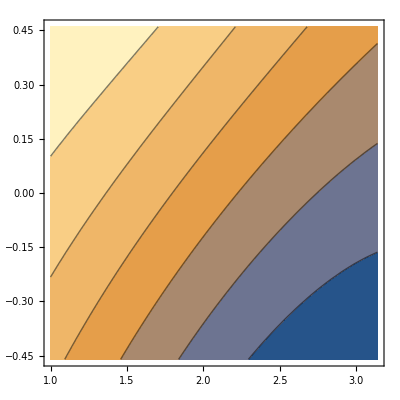

```mathematica
ContourPlot[
zbf[xi,beta,2.5,5,0.4,2,2,5,3.1],
{xi,1,Pi},{beta,-0.46,0.46}
]
```

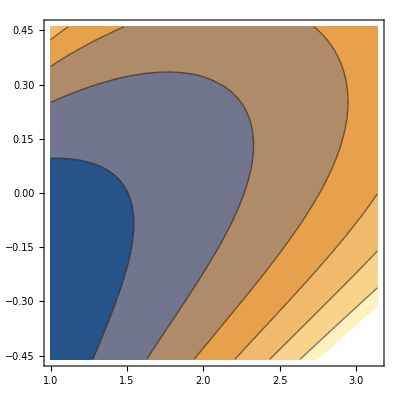

```mathematica
ContourPlot[
derivZBF[xi,beta,2.5,5,0.4,2,2,5,3.1],
{xi,1,Pi},{beta,-0.46,0.46}
]
```